```mathematica
GraphValues[tuple_, range_] := With[{values=DynamicVotedValues[tuple, range]},
Monitor[
Table[
N[{n,magicGraham2[tuple], Log[values[[n]]+1]}], {n,1,Length[values],IntegerPart[range/20]}
],
n]
]
```

```mathematica
Monitor[
ListPlot3D[
Flatten[
With[{range=16000},
Table[
GraphValues[tuple, range],
{tuple,Subsets[Prime[Range[2,10]], {2,7}]}]
]
,1
],
ViewPoint->{Back, Left, Top},
Mesh->8,
ImageSize->1000,
PlotStyle->Opacity[0.6],
AxesStyle->{{Thick,Red}, {Thick,Darker[Green]}, {Thick,Blue}},
PlotRange->Automatic
],
tuple
]
```

$Aborted

```mathematica
all=Monitor[
Flatten[
With[{range=16000},
Table[
GraphValues[tuple, range],
{tuple,Subsets[Prime[Range[2,10]], {2,7}]}]
]
,1
],
tuple
]
```

{{1.,0.156768,0.},{801.,0.156768,15.3934},{1601.,0.156768,17.7201},{2401.,0.156768,20.1025},{3201.,0.156768,20.9262},{4001.,0.156768,20.9807},{4801.,0.156768,21.1709},{5601.,0.156768,23.36},{6401.,0.156768,23.4471},{7201.,0.156768,23.4482},«9821»,{8801.,-0.0896349,3020.46},{9601.,-0.0896349,3286.83},{10401.,-0.0896349,3548.1},{11201.,-0.0896349,3816.34},{12001.,-0.0896349,4092.25},{12801.,-0.0896349,4356.06},{13601.,-0.0896349,4622.23},{14401.,-0.0896349,4884.23},{15201.,-0.0896349,5147.95}}

```mathematica
all={{1.,0.3135359480574428,0.},{801.,0.3135359480574428,15.393380607345016},{1601.,0.3135359480574428,17.720098632666094},{2401.,0.3135359480574428,20.102499131991152},{3201.,0.3135359480574428,20.92623244224393},{4001.,0.3135359480574428,20.980654796624147},{4801.,0.3135359480574428,21.170922802164498},{5601.,0.3135359480574428,23.359962141247962},{6401.,0.3135359480574428,23.44713407478282},{7201.,0.3135359480574428,23.448154926892535},{8001.,0.3135359480574428,24.182401000721406},{8801.,0.3135359480574428,24.22163539947913},{9601.,0.3135359480574428,24.222091962404257},{10401.,0.3135359480574428,24.48493876935616},{11201.,0.3135359480574428,24.54008732752398},{12001.,0.3135359480574428,24.540509400040182},{12801.,0.3135359480574428,24.545707702997515},{13601.,0.3135359480574428,24.54675726139106},{14401.,0.3135359480574428,24.546973643072448},{15201.,0.3135359480574428,26.47260966019397},{1.,0.3433441277875019,0.},{801.,0.3433441277875019,15.761035775800213},{1601.,0.3433441277875019,16.806207927635647},{2401.,0.3433441277875019,17.69962456527532},{3201.,0.3433441277875019,18.67793249252292},{4001.,0.3433441277875019,20.15231455082134},{4801.,0.3433441277875019,20.155367788584467},{5601.,0.3433441277875019,22.111605428905126},{6401.,0.3433441277875019,22.12149046507638},{7201.,0.3433441277875019,22.12271053338993},{8001.,0.3433441277875019,22.259984930091623},{8801.,0.3433441277875019,22.29633631605406},{9601.,0.3433441277875019,22.300736239412277},{10401.,0.3433441277875019,23.37119232950002},{11201.,0.3433441277875019,23.371316626534988},{12001.,0.3433441277875019,23.39494862656908},{12801.,0.3433441277875019,23.39788564673877},{13601.,0.3433441277875019,23.39932132774654},{14401.,0.3433441277875019,24.18775288719181},{15201.,0.3433441277875019,24.2058597683473},{1.,0.37815148988067165,0.},{801.,0.37815148988067165,13.183874194668851},{1601.,0.37815148988067165,14.569808339636348},{2401.,0.37815148988067165,15.518772637541684},{3201.,0.37815148988067165,16.795283760287944},{4001.,0.37815148988067165,16.880832604823876},{4801.,0.37815148988067165,17.614807029555827},{5601.,0.37815148988067165,17.68482416384335},{6401.,0.37815148988067165,17.893376456397476},{7201.,0.37815148988067165,17.95690006393149},{8001.,0.37815148988067165,17.974649999086488},{8801.,0.37815148988067165,19.880810295917396},{9601.,0.37815148988067165,19.882073873903373},{10401.,0.37815148988067165,19.885464584033443},{11201.,0.37815148988067165,19.89321094641184},{12001.,0.37815148988067165,19.9251081128146},{12801.,0.37815148988067165,19.928715075061255},{13601.,0.37815148988067165,20.091214323949313},{14401.,0.37815148988067165,20.099085026988938},{15201.,0.37815148988067165,20.87978711725011},{1.,0.38958416653075645,0.},{801.,0.38958416653075645,12.102582601670992},{1601.,0.38958416653075645,14.684325960894192},{2401.,0.38958416653075645,15.497389496826885},{3201.,0.38958416653075645,15.77741412770716},{4001.,0.38958416653075645,16.516049150777306},{4801.,0.38958416653075645,16.58952176798841},{5601.,0.38958416653075645,16.776577988609933},{6401.,0.38958416653075645,16.798606022311414},{7201.,0.38958416653075645,16.875150810155688},{8001.,0.38958416653075645,17.97465018653841},{8801.,0.38958416653075645,18.688703790346814},{9601.,0.38958416653075645,18.694733180978577},{10401.,0.38958416653075645,18.79405457808436},{11201.,0.38958416653075645,18.79706837682922},{12001.,0.38958416653075645,19.05360161773291},{12801.,0.38958416653075645,19.055604572650633},{13601.,0.38958416653075645,19.080853468812386},{14401.,0.38958416653075645,19.776900138190662},{15201.,0.38958416653075645,19.7892473554778},{1.,0.4064536236484377,0.},{801.,0.4064536236484377,12.489780581552482},{1601.,0.4064536236484377,14.298759825144156},{2401.,0.4064536236484377,14.435537432314028},{3201.,0.4064536236484377,15.668412318916142},{4001.,0.4064536236484377,17.697910830707368},{4801.,0.4064536236484377,17.727172958382248},{5601.,0.4064536236484377,17.865632697981695},{6401.,0.4064536236484377,18.677041268138314},{7201.,0.4064536236484377,18.68104099403142},{8001.,0.4064536236484377,18.689333158040494},{8801.,0.4064536236484377,18.792836697296938},{9601.,0.4064536236484377,18.79449786953416},{10401.,0.4064536236484377,18.830109506393864},{11201.,0.4064536236484377,18.994603655152396},{12001.,0.4064536236484377,18.99594130599141},{12801.,0.4064536236484377,19.004803075600474},{13601.,0.4064536236484377,19.080942575293484},{14401.,0.4064536236484377,19.89636875989171},{15201.,0.4064536236484377,19.916794196990534},{1.,0.41294123667099825,0.},{801.,0.41294123667099825,13.221529748898828},{1601.,0.41294123667099825,15.422704755150837},{2401.,0.41294123667099825,16.5313719058062},{3201.,0.41294123667099825,16.847031797572967},{4001.,0.41294123667099825,17.683301302183946},{4801.,0.41294123667099825,17.720861414026025},{5601.,0.41294123667099825,17.73155343287977},{6401.,0.41294123667099825,17.876093162215316},{7201.,0.41294123667099825,17.903172960871323},{8001.,0.41294123667099825,17.949469073318372},{8801.,0.41294123667099825,17.98040078102725},{9601.,0.41294123667099825,18.785650769376556},{10401.,0.41294123667099825,18.819371685785537},{11201.,0.41294123667099825,19.053736529567654},{12001.,0.41294123667099825,19.069462931813227},{12801.,0.41294123667099825,19.078975384583714},{13601.,0.41294123667099825,19.08182844378671},{14401.,0.41294123667099825,19.779134445577768},{15201.,0.41294123667099825,19.78054460648244},{1.,0.423438518908676,0.},{801.,0.423438518908676,13.321502719124442},{1601.,0.423438518908676,14.659468848189418},{2401.,0.423438518908676,15.773661058751028},{3201.,0.423438518908676,16.49348216642398},{4001.,0.423438518908676,16.52129138598619},{4801.,0.423438518908676,16.588842004316202},{5601.,0.423438518908676,16.794307179518054},{6401.,0.423438518908676,16.847370689799945},{7201.,0.423438518908676,16.87512050934699},{8001.,0.423438518908676,17.63123250883381},{8801.,0.423438518908676,17.87519041531439},{9601.,0.423438518908676,17.8959918678312},{10401.,0.423438518908676,17.981995160803855},{11201.,0.423438518908676,18.819371437442204},{12001.,0.423438518908676,18.827011250828306},{12801.,0.423438518908676,18.8305378199012},{13601.,0.423438518908676,18.976755515597358},{14401.,0.423438518908676,19.045439607745323},{15201.,0.423438518908676,19.048357331797618},{1.,0.43515080744693124,0.},{801.,0.43515080744693124,12.195087529471419},{1601.,0.43515080744693124,13.577731680826536},{2401.,0.43515080744693124,14.582414113160493},{3201.,0.43515080744693124,15.421047069822658},{4001.,0.43515080744693124,15.681879849588626},{4801.,0.43515080744693124,15.782337279474747},{5601.,0.43515080744693124,16.851067833206294},{6401.,0.43515080744693124,16.881901321758498},{7201.,0.43515080744693124,17.5834707495144},{8001.,0.43515080744693124,17.61858747167723},{8801.,0.43515080744693124,17.694273054480778},{9601.,0.43515080744693124,17.719720803106583},{10401.,0.43515080744693124,17.946786837381},{11201.,0.43515080744693124,17.957946087593758},{12001.,0.43515080744693124,17.97364866076983},{12801.,0.43515080744693124,17.981939490285477},{13601.,0.43515080744693124,18.680973479669593},{14401.,0.43515080744693124,18.690539721989296},{15201.,0.43515080744693124,18.783612790332686},{1.,0.3950205687020296,0.},{801.,0.3950205687020296,13.664179399548162},{1601.,0.3950205687020296,14.73356014215045},{2401.,0.3950205687020296,16.290591005028226},{3201.,0.3950205687020296,16.471455275293287},{4001.,0.3950205687020296,16.813180752535754},{4801.,0.3950205687020296,17.782850268995087},{5601.,0.3950205687020296,17.886202625652295},{6401.,0.3950205687020296,17.902131771766037},{7201.,0.3950205687020296,18.417551131821142},{8001.,0.3950205687020296,18.420899849946895},{8801.,0.3950205687020296,18.61291370344906},{9601.,0.3950205687020296,19.50288221203896},{10401.,0.3950205687020296,19.650010796534815},{11201.,0.3950205687020296,19.71074025964641},{12001.,0.3950205687020296,19.713071427929165},{12801.,0.3950205687020296,19.717353622901605},{13601.,0.3950205687020296,20.222804377534604},{14401.,0.3950205687020296,20.225536071867694},{15201.,0.3950205687020296,21.65679008033178},{1.,0.4298279307951994,0.},{801.,0.4298279307951994,12.094241238742036},{1601.,0.4298279307951994,13.617377861278992},{2401.,0.4298279307951994,14.571458344111033},{3201.,0.4298279307951994,15.187650719343337},{4001.,0.4298279307951994,15.300036056009334},{4801.,0.4298279307951994,16.797308903668075},{5601.,0.4298279307951994,16.828665815983484},{6401.,0.4298279307951994,16.902341382122813},{7201.,0.4298279307951994,16.976500414977515},{8001.,0.4298279307951994,17.892902770985515},{8801.,0.4298279307951994,17.92034580007421},{9601.,0.4298279307951994,17.9270135029133},{10401.,0.4298279307951994,17.951001238172942},{11201.,0.4298279307951994,18.397163181220424},{12001.,0.4298279307951994,18.40192020029837},{12801.,0.4298279307951994,18.417908665290156},{13601.,0.4298279307951994,18.437722219638246},{14401.,0.4298279307951994,19.360593396406326},{15201.,0.4298279307951994,19.496136350967383},{1.,0.44126060744528417,0.},{801.,0.44126060744528417,12.07254696717504},{1601.,0.44126060744528417,13.213371589728933},{2401.,0.44126060744528417,13.699878582118997},{3201.,0.44126060744528417,14.668713662312161},{4001.,0.44126060744528417,16.097580343766143},{4801.,0.44126060744528417,16.174611324951925},{5601.,0.44126060744528417,16.494266233900678},{6401.,0.44126060744528417,16.815484224082635},{7201.,0.44126060744528417,16.836308935327718},{8001.,0.44126060744528417,17.0027827681863},{8801.,0.44126060744528417,17.957414431929557},{9601.,0.44126060744528417,18.04143346518773},{10401.,0.44126060744528417,18.046546250992943},{11201.,0.44126060744528417,18.053008825763165},{12001.,0.44126060744528417,18.103827788408676},{12801.,0.44126060744528417,19.360212913044236},{13601.,0.44126060744528417,19.361688681285216},{14401.,0.44126060744528417,19.363273255451897},{15201.,0.44126060744528417,19.36933508654371},{1.,0.4581300645629654,0.},{801.,0.4581300645629654,11.361369748644284},{1601.,0.4581300645629654,12.954034662563334},{2401.,0.4581300645629654,14.52607467919448},{3201.,0.4581300645629654,14.890319446908375},{4001.,0.4581300645629654,15.364697491268815},{4801.,0.4581300645629654,15.394500396872301},{5601.,0.4581300645629654,16.11410088248501},{6401.,0.4581300645629654,16.179440389898758},{7201.,0.4581300645629654,16.285055146532695},{8001.,0.4581300645629654,17.003953443044004},{8801.,0.4581300645629654,17.0104126967525},{9601.,0.4581300645629654,17.72191138854424},{10401.,0.4581300645629654,17.751450519141226},{11201.,0.4581300645629654,17.760126612017928},{12001.,0.4581300645629654,17.78240105173199},{12801.,0.4581300645629654,17.789640135988922},{13601.,0.4581300645629654,17.888812366250924},{14401.,0.4581300645629654,18.1014863873885},{15201.,0.4581300645629654,18.103659908248687},{1.,0.46461767758552597,0.},{801.,0.46461767758552597,11.987929073460599},{1601.,0.46461767758552597,12.933104210951784},{2401.,0.46461767758552597,13.57043959860521},{3201.,0.46461767758552597,13.769101107645383},{4001.,0.46461767758552597,14.747010639067993},{4801.,0.46461767758552597,14.88345021431236},{5601.,0.46461767758552597,16.114050480276376},{6401.,0.46461767758552597,16.150745593030713},{7201.,0.46461767758552597,16.186472546104124},{8001.,0.46461767758552597,16.344337358027836},{8801.,0.46461767758552597,16.80924363445488},{9601.,0.46461767758552597,16.82770080305667},{10401.,0.46461767758552597,16.835486855703024},{11201.,0.46461767758552597,16.925895595203613},{12001.,0.46461767758552597,16.973454406287413},{12801.,0.46461767758552597,17.72360712501228},{13601.,0.46461767758552597,17.788158204032385},{14401.,0.46461767758552597,17.9010883037037},{15201.,0.46461767758552597,17.920746196518532},{1.,0.47511495982320373,0.},{801.,0.47511495982320373,11.525881176130444},{1601.,0.47511495982320373,13.279814889201047},{2401.,0.47511495982320373,13.75446247149934},{3201.,0.47511495982320373,14.502514406844977},{4001.,0.47511495982320373,14.675338445798415},{4801.,0.47511495982320373,14.745777959545133},{5601.,0.47511495982320373,14.883724462040194},{6401.,0.47511495982320373,16.439112567037107},{7201.,0.47511495982320373,16.460150632163725},{8001.,0.47511495982320373,16.497482867419986},{8801.,0.47511495982320373,16.79253777766792},{9601.,0.47511495982320373,16.807360354448544},{10401.,0.47511495982320373,16.832498520256213},{11201.,0.47511495982320373,16.88821248372843},{12001.,0.47511495982320373,16.901069047296097},{12801.,0.47511495982320373,16.92639547739739},{13601.,0.47511495982320373,17.78078994865559},{14401.,0.47511495982320373,17.78977173450246},{15201.,0.47511495982320373,17.795627799227276},{1.,0.48682724836145896,0.},{801.,0.48682724836145896,11.352510203563257},{1601.,0.48682724836145896,13.573453009405222},{2401.,0.48682724836145896,13.68696784402143},{3201.,0.48682724836145896,14.57142782189708},{4001.,0.48682724836145896,14.701603491482347},{4801.,0.48682724836145896,14.883755387515984},{5601.,0.48682724836145896,15.278662019633472},{6401.,0.48682724836145896,15.313516896437141},{7201.,0.48682724836145896,16.114093854441006},{8001.,0.48682724836145896,16.883041682559845},{8801.,0.48682724836145896,16.904488563634313},{9601.,0.48682724836145896,16.908882613872017},{10401.,0.48682724836145896,16.97131396510655},{11201.,0.48682724836145896,16.97716023964012},{12001.,0.48682724836145896,17.004092481271616},{12801.,0.48682724836145896,17.00974789277745},{13601.,0.48682724836145896,17.704533620927343},{14401.,0.48682724836145896,17.70742379053187},{15201.,0.48682724836145896,17.72038412696971},{1.,0.4596361105252585,0.},{801.,0.4596361105252585,12.371731141427588},{1601.,0.4596361105252585,13.642869988823172},{2401.,0.4596361105252585,14.412150692761497},{3201.,0.4596361105252585,14.728993351266201},{4001.,0.4596361105252585,14.781525113250487},{4801.,0.4596361105252585,15.608674706834451},{5601.,0.4596361105252585,15.629457879471765},{6401.,0.4596361105252585,15.821009094651789},{7201.,0.4596361105252585,15.870459207733235},{8001.,0.4596361105252585,16.813780858002502},{8801.,0.4596361105252585,17.534792899726988},{9601.,0.4596361105252585,17.540395755056462},{10401.,0.4596361105252585,17.573009997385086},{11201.,0.4596361105252585,17.580834646751324},{12001.,0.4596361105252585,17.647090632306845},{12801.,0.4596361105252585,17.65036908796494},{13601.,0.4596361105252585,17.686886303605164},{14401.,0.4596361105252585,17.689932625694297},{15201.,0.4596361105252585,17.88413415402167},{1.,0.4710687871753433,0.},{801.,0.4710687871753433,11.74310023919957},{1601.,0.4710687871753433,12.921140307189107},{2401.,0.4710687871753433,13.926123953062246},{3201.,0.4710687871753433,14.450638189307726},{4001.,0.4710687871753433,14.52806518970939},{4801.,0.4710687871753433,15.626892409487185},{5601.,0.4710687871753433,15.724642015417327},{6401.,0.4710687871753433,16.263968449180606},{7201.,0.4710687871753433,16.290672549080465},{8001.,0.4710687871753433,16.776236652725252},{8801.,0.4710687871753433,16.79984932128252},{9601.,0.4710687871753433,16.817996821889704},{10401.,0.4710687871753433,18.228180964339842},{11201.,0.4710687871753433,18.236558210372866},{12001.,0.4710687871753433,18.238119202364363},{12801.,0.4710687871753433,18.241191213184372},{13601.,0.4710687871753433,18.285195134517984},{14401.,0.4710687871753433,18.289041411680795},{15201.,0.4710687871753433,18.294454149067082},{1.,0.4879382442930245,0.},{801.,0.4879382442930245,10.62558655504584},{1601.,0.4879382442930245,12.512332330548002},{2401.,0.4879382442930245,12.823574518996207},{3201.,0.4879382442930245,14.384158575087017},{4001.,0.4879382442930245,14.511670695008839},{4801.,0.4879382442930245,14.86155470488443},{5601.,0.4879382442930245,15.570379703238295},{6401.,0.4879382442930245,15.59660788806375},{7201.,0.4879382442930245,15.626720795207671},{8001.,0.4879382442930245,15.826113010974833},{8801.,0.4879382442930245,15.854695309948843},{9601.,0.4879382442930245,15.868205194063044},{10401.,0.4879382442930245,15.968799153833128},{11201.,0.4879382442930245,16.261088975485688},{12001.,0.4879382442930245,16.282088593564808},{12801.,0.4879382442930245,16.291192288724314},{13601.,0.4879382442930245,17.700051898007704},{14401.,0.4879382442930245,17.704774980360604},{15201.,0.4879382442930245,17.70698185640609},{1.,0.4944258573155851,0.},{801.,0.4944258573155851,10.635903522016774},{1601.,0.4944258573155851,11.973919882870874},{2401.,0.4944258573155851,12.573693958764515},{3201.,0.4944258573155851,13.624404530438051},{4001.,0.4944258573155851,13.763738201476377},{4801.,0.4944258573155851,13.89071171808452},{5601.,0.4944258573155851,13.994610263498283},{6401.,0.4944258573155851,14.727753508614335},{7201.,0.4944258573155851,14.773936597585212},{8001.,0.4944258573155851,14.787806883881355},{8801.,0.4944258573155851,14.872205808326026},{9601.,0.4944258573155851,15.573224499635376},{10401.,0.4944258573155851,15.608105844466403},{11201.,0.4944258573155851,15.629568393747942},{12001.,0.4944258573155851,15.821252274956109},{12801.,0.4944258573155851,15.826452276231835},{13601.,0.4944258573155851,15.856423047238376},{14401.,0.4944258573155851,15.924595849733794},{15201.,0.4944258573155851,15.940848199092862},{1.,0.5049231395532628,0.},{801.,0.5049231395532628,10.642300975279205},{1601.,0.5049231395532628,12.562806087757847},{2401.,0.5049231395532628,12.877825082048432},{3201.,0.5049231395532628,13.669944755730898},{4001.,0.5049231395532628,13.78087873970885},{4801.,0.5049231395532628,14.012282207470912},{5601.,0.5049231395532628,14.383912208357854},{6401.,0.5049231395532628,14.407040209145228},{7201.,0.5049231395532628,14.525589582395378},{8001.,0.5049231395532628,14.773138991358968},{8801.,0.5049231395532628,14.854783585885361},{9601.,0.5049231395532628,15.72185580892718},{10401.,0.5049231395532628,15.737066829909018},{11201.,0.5049231395532628,15.839583935292005},{12001.,0.5049231395532628,15.852992218392899},{12801.,0.5049231395532628,15.945151865096777},{13601.,0.5049231395532628,15.958121950204273},{14401.,0.5049231395532628,16.397052721035276},{15201.,0.5049231395532628,16.41452512806728},{1.,0.5166354280915181,0.},{801.,0.5166354280915181,10.851722588592787},{1601.,0.5166354280915181,12.049208287005232},{2401.,0.5166354280915181,12.588084872263561},{3201.,0.5166354280915181,13.670211916318552},{4001.,0.5166354280915181,13.793628890962008},{4801.,0.5166354280915181,14.337604851113976},{5601.,0.5166354280915181,14.856452066261001},{6401.,0.5166354280915181,14.87409740977582},{7201.,0.5166354280915181,15.587600681013827},{8001.,0.5166354280915181,15.596960061678368},{8801.,0.5166354280915181,15.70197381105458},{9601.,0.5166354280915181,15.719689370601856},{10401.,0.5166354280915181,15.870450112633527},{11201.,0.5166354280915181,15.958154924448868},{12001.,0.5166354280915181,15.971787091169654},{12801.,0.5166354280915181,17.53388667646691},{13601.,0.5166354280915181,17.536392307140666},{14401.,0.5166354280915181,17.553278361903462},{15201.,0.5166354280915181,17.554511813035212},{1.,0.5058761492685131,0.},{801.,0.5058761492685131,11.032758362158031},{1601.,0.5058761492685131,12.85455190379482},{2401.,0.5058761492685131,13.154435523404066},{3201.,0.5058761492685131,13.605710090454032},{4001.,0.5058761492685131,13.67751894762622},{4801.,0.5058761492685131,14.513190450247711},{5601.,0.5058761492685131,14.6438261030788},{6401.,0.5058761492685131,15.487269158962448},{7201.,0.5058761492685131,15.54541412683015},{8001.,0.5058761492685131,15.55830157213002},{8801.,0.5058761492685131,15.608467643097361},{9601.,0.5058761492685131,15.77387398492254},{10401.,0.5058761492685131,15.782540253911227},{11201.,0.5058761492685131,16.08881749833099},{12001.,0.5058761492685131,16.79506659889741},{12801.,0.5058761492685131,16.80249311414021},{13601.,0.5058761492685131,16.81814719147489},{14401.,0.5058761492685131,16.821422838964043},{15201.,0.5058761492685131,16.873848830286782},{1.,0.5227456063861944,0.},{801.,0.5227456063861944,10.329931067029484},{1601.,0.5227456063861944,12.172309015377365},{2401.,0.5227456063861944,12.81884998157983},{3201.,0.5227456063861944,13.185689288627582},{4001.,0.5227456063861944,13.451366359897316},{4801.,0.5227456063861944,14.397996532329316},{5601.,0.5227456063861944,14.484797841629875},{6401.,0.5227456063861944,14.561703596275045},{7201.,0.5227456063861944,15.081782158365103},{8001.,0.5227456063861944,15.288678474076779},{8801.,0.5227456063861944,15.303300023657046},{9601.,0.5227456063861944,15.558451912632288},{10401.,0.5227456063861944,15.583279201625162},{11201.,0.5227456063861944,15.60088988396148},{12001.,0.5227456063861944,15.627384697301354},{12801.,0.5227456063861944,15.640107752093803},{13601.,0.5227456063861944,15.780666176330959},{14401.,0.5227456063861944,15.802930145196298},{15201.,0.5227456063861944,15.824442855831258},{1.,0.5292332194087549,0.},{801.,0.5292332194087549,10.334945240918547},{1601.,0.5292332194087549,11.98956949785322},{2401.,0.5292332194087549,12.684651898776217},{3201.,0.5292332194087549,13.203679735179577},{4001.,0.5292332194087549,13.409229617155093},{4801.,0.5292332194087549,13.470334956704265},{5601.,0.5292332194087549,13.63825176373278},{6401.,0.5292332194087549,14.776153430055817},{7201.,0.5292332194087549,14.790261877703877},{8001.,0.5292332194087549,15.089600201888285},{8801.,0.5292332194087549,15.49430754149273},{9601.,0.5292332194087549,15.500774423120882},{10401.,0.5292332194087549,15.522013836234834},{11201.,0.5292332194087549,15.54565044181377},{12001.,0.5292332194087549,15.586087758628656},{12801.,0.5292332194087549,15.612648371268737},{13601.,0.5292332194087549,15.632508832055954},{14401.,0.5292332194087549,15.82086439651574},{15201.,0.5292332194087549,15.826578099117015},{1.,0.5397305016464327,0.},{801.,0.5397305016464327,10.805090951658405},{1601.,0.5397305016464327,11.257633135320098},{2401.,0.5397305016464327,12.784829777736574},{3201.,0.5397305016464327,13.236543485862036},{4001.,0.5397305016464327,13.402293984724812},{4801.,0.5397305016464327,13.65749324567264},{5601.,0.5397305016464327,13.689274773269084},{6401.,0.5397305016464327,14.405600124706815},{7201.,0.5397305016464327,14.500307471885284},{8001.,0.5397305016464327,14.555255978372246},{8801.,0.5397305016464327,14.648513154791427},{9601.,0.5397305016464327,14.661123428123872},{10401.,0.5397305016464327,14.769895984655562},{11201.,0.5397305016464327,14.792592674219803},{12001.,0.5397305016464327,15.779902574541257},{12801.,0.5397305016464327,15.80226811835969},{13601.,0.5397305016464327,15.818729990430532},{14401.,0.5397305016464327,15.844382885152692},{15201.,0.5397305016464327,15.849332940021327},{1.,0.5514427901846879,0.},{801.,0.5514427901846879,10.428334417664374},{1601.,0.5514427901846879,11.260571925571742},{2401.,0.5514427901846879,12.194207532651399},{3201.,0.5514427901846879,12.68523730906797},{4001.,0.5514427901846879,13.470587715340178},{4801.,0.5514427901846879,13.634812083259655},{5601.,0.5514427901846879,13.686366100083417},{6401.,0.5514427901846879,14.57037023897429},{7201.,0.5514427901846879,14.592105565270822},{8001.,0.5514427901846879,14.648999078233711},{8801.,0.5514427901846879,14.69919751637385},{9601.,0.5514427901846879,14.718467184472155},{10401.,0.5514427901846879,15.086557914979645},{11201.,0.5514427901846879,15.102141201371037},{12001.,0.5514427901846879,15.133982612219047},{12801.,0.5514427901846879,15.146052222642744},{13601.,0.5514427901846879,15.261778976388213},{14401.,0.5514427901846879,15.289733604384518},{15201.,0.5514427901846879,15.302309538940275},{1.,0.5341782830362791,0.},{801.,0.5341782830362791,10.48776807810896},{1601.,0.5341782830362791,11.650580842268289},{2401.,0.5341782830362791,12.11849201563776},{3201.,0.5341782830362791,13.033143016951687},{4001.,0.5341782830362791,14.230588646299909},{4801.,0.5341782830362791,14.287164075395653},{5601.,0.5341782830362791,14.4380292444213},{6401.,0.5341782830362791,14.482102755297735},{7201.,0.5341782830362791,14.525808814347101},{8001.,0.5341782830362791,15.398422959074926},{8801.,0.5341782830362791,15.55354905152768},{9601.,0.5341782830362791,15.597452492521358},{10401.,0.5341782830362791,15.612169007568017},{11201.,0.5341782830362791,15.626643477437892},{12001.,0.5341782830362791,15.667690079066151},{12801.,0.5341782830362791,15.778567850854072},{13601.,0.5341782830362791,15.790822908927817},{14401.,0.5341782830362791,16.12388824146477},{15201.,0.5341782830362791,16.132165504715275},{1.,0.5406658960588396,0.},{801.,0.5406658960588396,10.33539983065914},{1601.,0.5406658960588396,11.886163480781764},{2401.,0.5406658960588396,12.105754949015306},{3201.,0.5406658960588396,12.98001609591821},{4001.,0.5406658960588396,13.206140028304029},{4801.,0.5406658960588396,13.597773614569364},{5601.,0.5406658960588396,13.725812301818307},{6401.,0.5406658960588396,13.981446941308896},{7201.,0.5406658960588396,14.023083920564423},{8001.,0.5406658960588396,15.419956631878103},{8801.,0.5406658960588396,15.469428215186397},{9601.,0.5406658960588396,15.476180222892262},{10401.,0.5406658960588396,15.496751602734003},{11201.,0.5406658960588396,15.543160747250907},{12001.,0.5406658960588396,15.550049729084648},{12801.,0.5406658960588396,15.607674945201966},{13601.,0.5406658960588396,15.613617340312192},{14401.,0.5406658960588396,16.123903651820417},{15201.,0.5406658960588396,16.134764451375887},{1.,0.5511631782965174,0.},{801.,0.5511631782965174,10.589685644007867},{1601.,0.5511631782965174,11.385728254703228},{2401.,0.5511631782965174,11.743497357712894},{3201.,0.5511631782965174,12.91246423047138},{4001.,0.5511631782965174,13.672387021758434},{4801.,0.5511631782965174,13.73036108292258},{5601.,0.5511631782965174,13.951386699515261},{6401.,0.5511631782965174,13.983577667805665},{7201.,0.5511631782965174,14.026366930120941},{8001.,0.5511631782965174,14.220157998540103},{8801.,0.5511631782965174,14.49553957036858},{9601.,0.5511631782965174,14.515131736899704},{10401.,0.5511631782965174,14.629502305130677},{11201.,0.5511631782965174,14.654258255377036},{12001.,0.5511631782965174,14.670574186566485},{12801.,0.5511631782965174,15.678065029421335},{13601.,0.5511631782965174,15.685848586600649},{14401.,0.5511631782965174,15.724063832981406},{15201.,0.5511631782965174,15.729907188421361},{1.,0.5628754668347726,0.},{801.,0.5628754668347726,9.398063978059133},{1601.,0.5628754668347726,11.489482820843678},{2401.,0.5628754668347726,11.934696899352703},{3201.,0.5628754668347726,12.10190031259249},{4001.,0.5628754668347726,13.57312429757042},{4801.,0.5628754668347726,13.632622040478477},{5601.,0.5628754668347726,13.667322565928885},{6401.,0.5628754668347726,14.212899810625354},{7201.,0.5628754668347726,14.230332421454603},{8001.,0.5628754668347726,14.251762839770349},{8801.,0.5628754668347726,14.30988418679079},{9601.,0.5628754668347726,14.327204804368368},{10401.,0.5628754668347726,14.647091843191216},{11201.,0.5628754668347726,14.667462428767461},{12001.,0.5628754668347726,14.679806696966994},{12801.,0.5628754668347726,15.420189363794096},{13601.,0.5628754668347726,15.425943175515165},{14401.,0.5628754668347726,15.4648220473128},{15201.,0.5628754668347726,15.481955450550599},{1.,0.5575353531765209,0.},{801.,0.5575353531765209,9.970912528850917},{1601.,0.5575353531765209,12.031540671011049},{2401.,0.5575353531765209,12.169330857302064},{3201.,0.5575353531765209,12.531574209497952},{4001.,0.5575353531765209,12.977698233961377},{4801.,0.5575353531765209,13.024922529337639},{5601.,0.5575353531765209,13.200122248337754},{6401.,0.5575353531765209,13.429625993670049},{7201.,0.5575353531765209,13.470737363526045},{8001.,0.5575353531765209,14.888597153793672},{8801.,0.5575353531765209,14.920150642910668},{9601.,0.5575353531765209,14.929672980830688},{10401.,0.5575353531765209,14.97561799139453},{11201.,0.5575353531765209,15.002977385066975},{12001.,0.5575353531765209,15.047955360581996},{12801.,0.5575353531765209,15.054249939723208},{13601.,0.5575353531765209,15.080381923052533},{14401.,0.5575353531765209,15.418636793607028},{15201.,0.5575353531765209,15.570479478795251},{1.,0.5680326354141987,0.},{801.,0.5680326354141987,10.122422259076282},{1601.,0.5680326354141987,11.391412983568337},{2401.,0.5680326354141987,11.646538104294148},{3201.,0.5680326354141987,12.58462893708112},{4001.,0.5680326354141987,12.790403345458902},{4801.,0.5680326354141987,13.281322478223892},{5601.,0.5680326354141987,13.323748726531615},{6401.,0.5680326354141987,13.421798115922979},{7201.,0.5680326354141987,14.169529377525738},{8001.,0.5680326354141987,14.187237549316405},{8801.,0.5680326354141987,14.236596358641824},{9601.,0.5680326354141987,14.3351516114009},{10401.,0.5680326354141987,14.35034465791366},{11201.,0.5680326354141987,14.391660331680688},{12001.,0.5680326354141987,14.48952078961501},{12801.,0.5680326354141987,14.525791120277564},{13601.,0.5680326354141987,14.556595634854666},{14401.,0.5680326354141987,14.866867354251557},{15201.,0.5680326354141987,14.891853720026113},{1.,0.5797449239524539,0.},{801.,0.5797449239524539,10.11188288150143},{1601.,0.5797449239524539,11.339809407255666},{2401.,0.5797449239524539,11.604309766772047},{3201.,0.5797449239524539,12.096575809303278},{4001.,0.5797449239524539,12.241946417766378},{4801.,0.5797449239524539,12.528590832817413},{5601.,0.5797449239524539,13.470709129733297},{6401.,0.5797449239524539,14.180279358097742},{7201.,0.5797449239524539,14.23035817898183},{8001.,0.5797449239524539,14.247351414240612},{8801.,0.5797449239524539,14.281699420230002},{9601.,0.5797449239524539,14.337616123308706},{10401.,0.5797449239524539,14.37855930369414},{11201.,0.5797449239524539,14.568755633409083},{12001.,0.5797449239524539,14.866214343685447},{12801.,0.5797449239524539,14.890300671767822},{13601.,0.5797449239524539,14.899995862359544},{14401.,0.5797449239524539,14.923377556059105},{15201.,0.5797449239524539,14.948575157723361},{1.,0.5745202484367592,0.},{801.,0.5745202484367592,10.222631954177766},{1601.,0.5745202484367592,10.825084183200465},{2401.,0.5745202484367592,11.847717719783347},{3201.,0.5745202484367592,12.627345483843852},{4001.,0.5745202484367592,12.882350841453277},{4801.,0.5745202484367592,13.240107301184741},{5601.,0.5745202484367592,13.279710656944145},{6401.,0.5745202484367592,13.422663506291727},{7201.,0.5745202484367592,13.646475148135728},{8001.,0.5745202484367592,13.741818806870855},{8801.,0.5745202484367592,13.776565966685839},{9601.,0.5745202484367592,13.981213961637648},{10401.,0.5745202484367592,14.004714212040035},{11201.,0.5745202484367592,14.023087170773655},{12001.,0.5745202484367592,14.773503153160577},{12801.,0.5745202484367592,14.782054003009089},{13601.,0.5745202484367592,14.792436829242325},{14401.,0.5745202484367592,14.871870315493473},{15201.,0.5745202484367592,14.883184830378974},{1.,0.5862325369750144,0.},{801.,0.5862325369750144,10.23756406455664},{1601.,0.5862325369750144,10.91328684226798},{2401.,0.5862325369750144,11.895667685971125},{3201.,0.5862325369750144,12.063379411113266},{4001.,0.5862325369750144,12.509253981428879},{4801.,0.5862325369750144,12.619287645498398},{5601.,0.5862325369750144,12.691715836763588},{6401.,0.5862325369750144,13.570936505085246},{7201.,0.5862325369750144,13.60578532697116},{8001.,0.5862325369750144,13.638410545151391},{8801.,0.5862325369750144,13.742239620015045},{9601.,0.5862325369750144,13.776155195746215},{10401.,0.5862325369750144,13.870421002569175},{11201.,0.5862325369750144,14.87636732622644},{12001.,0.5862325369750144,14.890280872146812},{12801.,0.5862325369750144,14.91783893342116},{13601.,0.5862325369750144,14.930258956539635},{14401.,0.5862325369750144,14.956432693750813},{15201.,0.5862325369750144,14.969460733948727},{1.,0.5967298192126922,0.},{801.,0.5967298192126922,10.152220874849334},{1601.,0.5967298192126922,10.866261026623258},{2401.,0.5967298192126922,11.26952818462875},{3201.,0.5967298192126922,11.714191437765122},{4001.,0.5967298192126922,12.59068517533646},{4801.,0.5967298192126922,12.67808675241067},{5601.,0.5967298192126922,12.755961277707014},{6401.,0.5967298192126922,13.661480204230875},{7201.,0.5967298192126922,13.69822140033006},{8001.,0.5967298192126922,13.73967756034775},{8801.,0.5967298192126922,13.767642968092272},{9601.,0.5967298192126922,14.162337569806907},{10401.,0.5967298192126922,14.180638970442292},{11201.,0.5967298192126922,14.202717325751083},{12001.,0.5967298192126922,14.220204702289555},{12801.,0.5967298192126922,14.245213541139032},{13601.,0.5967298192126922,14.342967904665775},{14401.,0.5967298192126922,14.36515392908835},{15201.,0.5967298192126922,14.383535461401861},{1.,0.025950322273487147,0.},{801.,0.025950322273487147,41.0510175558016},{1601.,0.025950322273487147,61.56408454398171},{2401.,0.025950322273487147,65.11925748387196},{3201.,0.025950322273487147,69.25424054621406},{4001.,0.025950322273487147,74.84436277813663},{4801.,0.025950322273487147,100.01595321651062},{5601.,0.025950322273487147,100.01595323987718},{6401.,0.025950322273487147,100.01595329833003},{7201.,0.025950322273487147,100.01595329833003},{8001.,0.025950322273487147,100.01600373838077},{8801.,0.025950322273487147,102.30929046702879},{9601.,0.025950322273487147,111.27593687983962},{10401.,0.025950322273487147,111.27593687983962},{11201.,0.025950322273487147,119.89052859218445},{12001.,0.025950322273487147,119.89052859218445},{12801.,0.025950322273487147,119.89052863629651},{13601.,0.025950322273487147,129.63813380470646},{14401.,0.025950322273487147,129.63813380499047},{15201.,0.025950322273487147,129.63813380499047},{1.,0.06075768436665685,0.},{801.,0.06075768436665685,36.291203246937975},{1601.,0.06075768436665685,41.02531263253609},{2401.,0.06075768436665685,50.68559681766413},{3201.,0.06075768436665685,50.689923933273576},{4001.,0.06075768436665685,53.12952950048194},{4801.,0.06075768436665685,53.12952951438414},{5601.,0.06075768436665685,53.129618514834924},{6401.,0.06075768436665685,53.12966625638954},{7201.,0.06075768436665685,56.347804541022725},{8001.,0.06075768436665685,56.348468556832074},{8801.,0.06075768436665685,61.55866376962338},{9601.,0.06075768436665685,61.558663772231725},{10401.,0.06075768436665685,65.11914727721997},{11201.,0.06075768436665685,65.11914774170097},{12001.,0.06075768436665685,72.64789294216216},{12801.,0.06075768436665685,82.7753270103559},{13601.,0.06075768436665685,82.77532701035916},{14401.,0.06075768436665685,82.77532701035925},{15201.,0.06075768436665685,82.77532701035925},{1.,0.0721903610167417,0.},{801.,0.0721903610167417,30.80344398965693},{1601.,0.0721903610167417,37.39321353903466},{2401.,0.0721903610167417,37.75426545052328},{3201.,0.0721903610167417,41.05140430237045},{4001.,0.0721903610167417,44.347091785002654},{4801.,0.0721903610167417,45.08392538333537},{5601.,0.0721903610167417,45.41463698147768},{6401.,0.0721903610167417,47.39088218704078},{7201.,0.0721903610167417,50.58979360141614},{8001.,0.0721903610167417,50.59007197979004},{8801.,0.0721903610167417,53.129526983133566},{9601.,0.0721903610167417,53.129667740978874},{10401.,0.0721903610167417,53.130474782874835},{11201.,0.0721903610167417,53.130475290757275},{12001.,0.0721903610167417,57.24566774324322},{12801.,0.0721903610167417,60.42566305019365},{13601.,0.0721903610167417,60.42566353766652},{14401.,0.0721903610167417,61.89867907484567},{15201.,0.0721903610167417,61.89897825977629},{1.,0.08905981813442287,0.},{801.,0.08905981813442287,29.78063654380229},{1601.,0.08905981813442287,34.164049594013576},{2401.,0.08905981813442287,35.45672600421153},{3201.,0.08905981813442287,44.33789268923476},{4001.,0.08905981813442287,48.377720015508956},{4801.,0.08905981813442287,48.48067378750539},{5601.,0.08905981813442287,48.48067545454896},{6401.,0.08905981813442287,51.75164192753597},{7201.,0.08905981813442287,51.75661572240571},{8001.,0.08905981813442287,51.756664958335804},{8801.,0.08905981813442287,53.129217974576456},{9601.,0.08905981813442287,53.129218199888975},{10401.,0.08905981813442287,53.12955211956491},{11201.,0.08905981813442287,53.129552149394314},{12001.,0.08905981813442287,53.12965256263418},{12801.,0.08905981813442287,53.13047237721487},{13601.,0.08905981813442287,53.1305444947152},{14401.,0.08905981813442287,53.844896874679854},{15201.,0.08905981813442287,53.844896882429005},{1.,0.0955474311569835,0.},{801.,0.0955474311569835,29.801927171770846},{1601.,0.0955474311569835,35.44686808305218},{2401.,0.0955474311569835,42.04418310630697},{3201.,0.0955474311569835,42.06335446084118},{4001.,0.0955474311569835,44.269989734459806},{4801.,0.0955474311569835,44.270011487482755},{5601.,0.0955474311569835,45.412110276963645},{6401.,0.0955474311569835,45.41214535857091},{7201.,0.0955474311569835,47.38917404032628},{8001.,0.0955474311569835,51.75545169118724},{8801.,0.0955474311569835,51.75661732602008},{9601.,0.0955474311569835,51.756617329070416},{10401.,0.0955474311569835,53.113384752412856},{11201.,0.0955474311569835,53.113398091355464},{12001.,0.0955474311569835,53.11352890494799},{12801.,0.0955474311569835,53.84474300494539},{13601.,0.0955474311569835,53.845695656283176},{14401.,0.0955474311569835,53.84569566171398},{15201.,0.0955474311569835,53.84849757850614},{1.,0.10604471339466126,0.},{801.,0.10604471339466126,26.484330638595935},{1601.,0.10604471339466126,32.23169490925391},{2401.,0.10604471339466126,37.754198274380705},{3201.,0.10604471339466126,37.75427397347202},{4001.,0.10604471339466126,38.82246915229323},{4801.,0.10604471339466126,41.02877114387559},{5601.,0.10604471339466126,41.041697268829665},{6401.,0.10604471339466126,44.268706383621705},{7201.,0.10604471339466126,44.27001126960529},{8001.,0.10604471339466126,44.270015972559335},{8801.,0.10604471339466126,45.08085882172172},{9601.,0.10604471339466126,45.08359661020573},{10401.,0.10604471339466126,45.14892377524441},{11201.,0.10604471339466126,45.14892381617908},{12001.,0.10604471339466126,45.14901976196148},{12801.,0.10604471339466126,54.948894976692216},{13601.,0.10604471339466126,54.982736420936384},{14401.,0.10604471339466126,54.98273642106797},{15201.,0.10604471339466126,57.14071743690607},{1.,0.1177570019329165,0.},{801.,0.1177570019329165,27.76542310861296},{1601.,0.1177570019329165,37.36650037806949},{2401.,0.1177570019329165,37.754265429185274},{3201.,0.1177570019329165,38.84451206674364},{4001.,0.1177570019329165,38.8448212794375},{4801.,0.1177570019329165,38.85597973512381},{5601.,0.1177570019329165,41.90141272767828},{6401.,0.1177570019329165,45.41220131844934},{7201.,0.1177570019329165,45.413690957848694},{8001.,0.1177570019329165,47.3907656618306},{8801.,0.1177570019329165,47.39076577212066},{9601.,0.1177570019329165,47.39447685986461},{10401.,0.1177570019329165,48.33956898659865},{11201.,0.1177570019329165,48.62700803167189},{12001.,0.1177570019329165,48.62700844401069},{12801.,0.1177570019329165,48.62700846729685},{13601.,0.1177570019329165,48.62780523946786},{14401.,0.1177570019329165,48.62780525466304},{15201.,0.1177570019329165,48.62780817378992},{1.,0.09056586409671596,0.},{801.,0.09056586409671596,27.617736294362395},{1601.,0.09056586409671596,37.35755592634622},{2401.,0.09056586409671596,43.17338915442142},{3201.,0.09056586409671596,43.96281639323663},{4001.,0.09056586409671596,44.06109867900636},{4801.,0.09056586409671596,48.7076511467961},{5601.,0.09056586409671596,48.708037794184115},{6401.,0.09056586409671596,48.71550549263319},{7201.,0.09056586409671596,48.715505654888084},{8001.,0.09056586409671596,48.715505975583916},{8801.,0.09056586409671596,48.716238697078495},{9601.,0.09056586409671596,52.84423832093767},{10401.,0.09056586409671596,52.84428858837833},{11201.,0.09056586409671596,52.84428885756281},{12001.,0.09056586409671596,55.24906770849155},{12801.,0.09056586409671596,55.24906826791},{13601.,0.09056586409671596,55.24906826792831},{14401.,0.09056586409671596,55.24906826800275},{15201.,0.09056586409671596,55.24906833557478},{1.,0.10199854074680081,0.},{801.,0.10199854074680081,26.487302922614276},{1601.,0.10199854074680081,33.35268372164214},{2401.,0.10199854074680081,37.75463559141537},{3201.,0.10199854074680081,41.05103264901677},{4001.,0.10199854074680081,41.05275887653898},{4801.,0.10199854074680081,41.05276404521756},{5601.,0.10199854074680081,47.555524969857565},{6401.,0.10199854074680081,47.5589063135082},{7201.,0.10199854074680081,47.61762262617158},{8001.,0.10199854074680081,49.54702256432018},{8801.,0.10199854074680081,49.54720973065197},{9601.,0.10199854074680081,49.54721947963011},{10401.,0.10199854074680081,55.25774780039581},{11201.,0.10199854074680081,55.25774780039592},{12001.,0.10199854074680081,55.259113811404816},{12801.,0.10199854074680081,55.332912052303534},{13601.,0.10199854074680081,56.43183073107931},{14401.,0.10199854074680081,56.43183074472089},{15201.,0.10199854074680081,56.43183074719438},{1.,0.11886799786448199,0.},{801.,0.11886799786448199,24.496494829486476},{1601.,0.11886799786448199,29.95395115346995},{2401.,0.11886799786448199,31.898103552349962},{3201.,0.11886799786448199,31.970181752910946},{4001.,0.11886799786448199,35.16106779605499},{4801.,0.11886799786448199,39.68991779119791},{5601.,0.11886799786448199,39.69298155085007},{6401.,0.11886799786448199,39.69309792828307},{7201.,0.11886799786448199,41.75183673192834},{8001.,0.11886799786448199,41.75279144028302},{8801.,0.11886799786448199,41.761342326295164},{9601.,0.11886799786448199,41.76136715368241},{10401.,0.11886799786448199,42.85136869682759},{11201.,0.11886799786448199,42.85136872794906},{12001.,0.11886799786448199,42.85141016698918},{12801.,0.11886799786448199,42.85141869736311},{13601.,0.11886799786448199,42.85880402866305},{14401.,0.11886799786448199,42.85882042496495},{15201.,0.11886799786448199,49.55533922711531},{1.,0.1253556108870426,0.},{801.,0.1253556108870426,26.528975619014716},{1601.,0.1253556108870426,33.120477868554026},{2401.,0.1253556108870426,39.703670187229875},{3201.,0.1253556108870426,43.21455780937444},{4001.,0.1253556108870426,43.21487524319371},{4801.,0.1253556108870426,43.2148752485488},{5601.,0.1253556108870426,51.74014338280874},{6401.,0.1253556108870426,51.740144881108186},{7201.,0.1253556108870426,51.74068832906766},{8001.,0.1253556108870426,51.74069417546345},{8801.,0.1253556108870426,55.2490681590305},{9601.,0.1253556108870426,55.249068159054595},{10401.,0.1253556108870426,55.24906817531608},{11201.,0.1253556108870426,55.24906833368128},{12001.,0.1253556108870426,57.127906827100944},{12801.,0.1253556108870426,57.12790682712101},{13601.,0.1253556108870426,57.12790682713206},{14401.,0.1253556108870426,57.127906827136215},{15201.,0.1253556108870426,57.12790685032315},{1.,0.13585289312472038,0.},{801.,0.13585289312472038,22.261011170675534},{1601.,0.13585289312472038,25.320843842753387},{2401.,0.13585289312472038,30.03310720525366},{3201.,0.13585289312472038,33.35524638041261},{4001.,0.13585289312472038,33.36368691691662},{4801.,0.13585289312472038,35.293877052419205},{5601.,0.13585289312472038,37.679955229563916},{6401.,0.13585289312472038,42.8596540287312},{7201.,0.13585289312472038,42.963933651651814},{8001.,0.13585289312472038,42.96411773610555},{8801.,0.13585289312472038,42.984034723267975},{9601.,0.13585289312472038,42.984035079699034},{10401.,0.13585289312472038,42.98443348891187},{11201.,0.13585289312472038,42.98461133209593},{12001.,0.13585289312472038,42.99826491208044},{12801.,0.13585289312472038,42.998266946472704},{13601.,0.13585289312472038,42.99866218607059},{14401.,0.13585289312472038,43.95743306610824},{15201.,0.13585289312472038,43.95813244912178},{1.,0.1475651816629756,0.},{801.,0.1475651816629756,25.67229188103729},{1601.,0.1475651816629756,31.97018699583539},{2401.,0.1475651816629756,32.2565110298181},{3201.,0.1475651816629756,35.159922033393066},{4001.,0.1475651816629756,36.25892553227425},{4801.,0.1475651816629756,36.25974572952781},{5601.,0.1475651816629756,36.27209925583304},{6401.,0.1475651816629756,39.69182942953855},{7201.,0.1475651816629756,39.69182953033058},{8001.,0.1475651816629756,39.699414010288486},{8801.,0.1475651816629756,39.70365581653516},{9601.,0.1475651816629756,39.70367027804179},{10401.,0.1475651816629756,42.06647259958311},{11201.,0.1475651816629756,42.07231022789447},{12001.,0.1475651816629756,42.99609569001195},{12801.,0.1475651816629756,42.99609577552011},{13601.,0.1475651816629756,42.99648986778004},{14401.,0.1475651816629756,44.04991472105818},{15201.,0.1475651816629756,44.04991886313444},{1.,0.13680590283997063,0.},{801.,0.13680590283997063,22.366368007837718},{1601.,0.13680590283997063,25.662371065592378},{2401.,0.13680590283997063,27.48230035376317},{3201.,0.13680590283997063,29.676364774169244},{4001.,0.13680590283997063,32.000865506969426},{4801.,0.13680590283997063,32.009794027606056},{5601.,0.13680590283997063,37.357385508963226},{6401.,0.13680590283997063,37.357402554200355},{7201.,0.13680590283997063,37.35889853337633},{8001.,0.13680590283997063,38.49322721746155},{8801.,0.13680590283997063,38.493288386781764},{9601.,0.13680590283997063,38.49329385355794},{10401.,0.13680590283997063,38.74323182097282},{11201.,0.13680590283997063,38.74323212844596},{12001.,0.13680590283997063,38.74333467063136},{12801.,0.13680590283997063,38.74369249666635},{13601.,0.13680590283997063,38.748783408822035},{14401.,0.13680590283997063,38.74883413254757},{15201.,0.13680590283997063,38.75255043985746},{1.,0.1536753599576518,0.},{801.,0.1536753599576518,24.169492942064057},{1601.,0.1536753599576518,26.40360251952998},{2401.,0.1536753599576518,27.479084299852506},{3201.,0.1536753599576518,29.025280621122356},{4001.,0.1536753599576518,31.997921530355875},{4801.,0.1536753599576518,34.358342127322615},{5601.,0.1536753599576518,37.668246219015764},{6401.,0.1536753599576518,37.66835605596272},{7201.,0.1536753599576518,37.67123430803295},{8001.,0.1536753599576518,37.671234590398925},{8801.,0.1536753599576518,37.67123562789272},{9601.,0.1536753599576518,37.67139470206428},{10401.,0.1536753599576518,38.469311104732824},{11201.,0.1536753599576518,38.46932744303879},{12001.,0.1536753599576518,38.49196965099702},{12801.,0.1536753599576518,39.84811658588351},{13601.,0.1536753599576518,40.76647345735009},{14401.,0.1536753599576518,40.790916718867194},{15201.,0.1536753599576518,40.79093199837413},{1.,0.16016297298021237,0.},{801.,0.16016297298021237,19.893103375779962},{1601.,0.16016297298021237,25.373921185550486},{2401.,0.16016297298021237,25.662410204025758},{3201.,0.16016297298021237,29.680426274218263},{4001.,0.16016297298021237,37.470630755614366},{4801.,0.16016297298021237,37.4706364123387},{5601.,0.16016297298021237,37.47064989209599},{6401.,0.16016297298021237,38.46913027217751},{7201.,0.16016297298021237,38.55692778500554},{8001.,0.16016297298021237,38.55726488676749},{8801.,0.16016297298021237,38.557270047175},{9601.,0.16016297298021237,38.56107953642547},{10401.,0.16016297298021237,38.561086364379214},{11201.,0.16016297298021237,38.561096669562765},{12001.,0.16016297298021237,38.56919796018311},{12801.,0.16016297298021237,38.56920289761917},{13601.,0.16016297298021237,38.569218156586714},{14401.,0.16016297298021237,38.56921820577803},{15201.,0.16016297298021237,38.569608358987665},{1.,0.17066025521789008,0.},{801.,0.17066025521789008,22.28736864001921},{1601.,0.17066025521789008,24.175570993930187},{2401.,0.17066025521789008,25.388710620130055},{3201.,0.17066025521789008,26.69384281918108},{4001.,0.17066025521789008,27.482252837930634},{4801.,0.17066025521789008,28.95700781794731},{5601.,0.17066025521789008,28.965272847002456},{6401.,0.17066025521789008,35.20510253761448},{7201.,0.17066025521789008,35.205252696857585},{8001.,0.17066025521789008,35.20526365357532},{8801.,0.17066025521789008,35.20526887522433},{9601.,0.17066025521789008,36.29079116077689},{10401.,0.17066025521789008,36.30371954589681},{11201.,0.17066025521789008,36.303730156874266},{12001.,0.17066025521789008,36.30376975039782},{12801.,0.17066025521789008,36.30414985852727},{13601.,0.17066025521789008,36.30434956049452},{14401.,0.17066025521789008,36.30436401699491},{15201.,0.17066025521789008,36.361232973910916},{1.,0.18237254375614537,0.},{801.,0.18237254375614537,17.883879215361976},{1601.,0.18237254375614537,25.388154496732213},{2401.,0.18237254375614537,27.76357697708444},{3201.,0.18237254375614537,27.836829287352188},{4001.,0.18237254375614537,31.965528543292585},{4801.,0.18237254375614537,31.96928950556122},{5601.,0.18237254375614537,32.001677476759625},{6401.,0.18237254375614537,32.00194221924454},{7201.,0.18237254375614537,34.43457954742233},{8001.,0.18237254375614537,37.36561444259938},{8801.,0.18237254375614537,38.45555375385962},{9601.,0.18237254375614537,38.4555538443834},{10401.,0.18237254375614537,38.45558778184774},{11201.,0.18237254375614537,38.45559501025561},{12001.,0.18237254375614537,38.45560527985002},{12801.,0.18237254375614537,38.456151390628726},{13601.,0.18237254375614537,38.45616164701848},{14401.,0.18237254375614537,38.45621221888515},{15201.,0.18237254375614537,38.456213805499125},{1.,0.16510803660773665,0.},{801.,0.16510803660773665,21.251241208114735},{1601.,0.16510803660773665,24.311219739671646},{2401.,0.16510803660773665,25.662375947995248},{3201.,0.16510803660773665,27.4707855250855},{4001.,0.16510803660773665,28.565957242453205},{4801.,0.16510803660773665,30.03152654497337},{5601.,0.16510803660773665,30.0334643300131},{6401.,0.16510803660773665,31.976362732549166},{7201.,0.16510803660773665,31.98105942016168},{8001.,0.16510803660773665,32.264260108063304},{8801.,0.16510803660773665,34.162494686176494},{9601.,0.16510803660773665,34.16254475547822},{10401.,0.16510803660773665,35.1919634015231},{11201.,0.16510803660773665,38.48794733674901},{12001.,0.16510803660773665,38.48801573691462},{12801.,0.16510803660773665,38.48801815663497},{13601.,0.16510803660773665,38.491977016698414},{14401.,0.16510803660773665,39.69349362629658},{15201.,0.16510803660773665,39.69349578322399},{1.,0.17159564963029716,0.},{801.,0.17159564963029716,19.079091909251474},{1601.,0.17159564963029716,25.664037416474784},{2401.,0.17159564963029716,28.602121738199287},{3201.,0.17159564963029716,29.68067494206141},{4001.,0.17159564963029716,30.871583211829094},{4801.,0.17159564963029716,30.882846698844233},{5601.,0.17159564963029716,30.882848797942206},{6401.,0.17159564963029716,31.05839978449843},{7201.,0.17159564963029716,34.0935120846796},{8001.,0.17159564963029716,38.48784922693238},{8801.,0.17159564963029716,38.48801089441599},{9601.,0.17159564963029716,38.56063959455977},{10401.,0.17159564963029716,38.56063991552925},{11201.,0.17159564963029716,38.56066977514087},{12001.,0.17159564963029716,38.56107954079926},{12801.,0.17159564963029716,38.56107954416753},{13601.,0.17159564963029716,38.56108655174037},{14401.,0.17159564963029716,38.57149732374869},{15201.,0.17159564963029716,39.69349375277927},{1.,0.18209293186797493,0.},{801.,0.18209293186797493,16.77951338463128},{1601.,0.18209293186797493,20.915785389466613},{2401.,0.18209293186797493,23.119567579567903},{3201.,0.18209293186797493,26.76067868144296},{4001.,0.18209293186797493,27.482091344611643},{4801.,0.18209293186797493,28.61796504015564},{5601.,0.18209293186797493,28.956979046493053},{6401.,0.18209293186797493,29.662735646090283},{7201.,0.18209293186797493,29.680875181602136},{8001.,0.18209293186797493,30.03345368709653},{8801.,0.18209293186797493,32.17498631992521},{9601.,0.18209293186797493,32.22758797509251},{10401.,0.18209293186797493,32.227916598554685},{11201.,0.18209293186797493,32.26426884513964},{12001.,0.18209293186797493,33.36246234173982},{12801.,0.18209293186797493,33.36249687885294},{13601.,0.18209293186797493,33.36290610773425},{14401.,0.18209293186797493,33.36342178226312},{15201.,0.18209293186797493,33.363728180226936},{1.,0.19380522040623016,0.},{801.,0.19380522040623016,17.973767038799583},{1601.,0.19380522040623016,20.91578945363319},{2401.,0.19380522040623016,25.673434368177936},{3201.,0.19380522040623016,31.04990711715519},{4001.,0.19380522040623016,31.05327440885807},{4801.,0.19380522040623016,31.130169420540877},{5601.,0.19380522040623016,31.131762363405905},{6401.,0.19380522040623016,31.131835050047986},{7201.,0.19380522040623016,31.16354445288455},{8001.,0.19380522040623016,31.977434014798977},{8801.,0.19380522040623016,31.97784412580456},{9601.,0.19380522040623016,32.002807143237405},{10401.,0.19380522040623016,32.002813726372636},{11201.,0.19380522040623016,32.17487454323236},{12001.,0.19380522040623016,32.26154501917155},{12801.,0.19380522040623016,32.262055108385134},{13601.,0.19380522040623016,34.45098894224117},{14401.,0.19380522040623016,34.45283717156545},{15201.,0.19380522040623016,34.45322297804735},{1.,0.1884651067479784,0.},{801.,0.1884651067479784,21.012334338111586},{1601.,0.1884651067479784,25.556113255614648},{2401.,0.1884651067479784,25.560383173115415},{3201.,0.1884651067479784,26.654838911988612},{4001.,0.1884651067479784,26.73453752371049},{4801.,0.1884651067479784,27.61782593842711},{5601.,0.1884651067479784,28.60077720615298},{6401.,0.1884651067479784,29.768351737489056},{7201.,0.1884651067479784,29.805510160917738},{8001.,0.1884651067479784,33.11199600767221},{8801.,0.1884651067479784,33.11237193769783},{9601.,0.1884651067479784,33.276786755312756},{10401.,0.1884651067479784,33.276819293043324},{11201.,0.1884651067479784,33.28256994925779},{12001.,0.1884651067479784,33.28257130718314},{12801.,0.1884651067479784,33.28342417080278},{13601.,0.1884651067479784,33.28352436507879},{14401.,0.1884651067479784,34.06266148171959},{15201.,0.1884651067479784,34.06267275887756},{1.,0.1989623889856561,0.},{801.,0.1989623889856561,19.08063706678557},{1601.,0.1989623889856561,21.25395271687811},{2401.,0.1989623889856561,23.39799082494761},{3201.,0.1989623889856561,24.290948059144572},{4001.,0.1989623889856561,27.48185879150238},{4801.,0.1989623889856561,27.503149776066056},{5601.,0.1989623889856561,27.513704974055923},{6401.,0.1989623889856561,30.03346433068015},{7201.,0.1989623889856561,30.034094784371142},{8001.,0.1989623889856561,32.264170884396215},{8801.,0.1989623889856561,32.26511603208135},{9601.,0.1989623889856561,32.9765600439182},{10401.,0.1989623889856561,33.0000694093096},{11201.,0.1989623889856561,33.00008097679165},{12001.,0.1989623889856561,33.00020915040088},{12801.,0.1989623889856561,35.19218061792568},{13601.,0.1989623889856561,37.64096142468922},{14401.,0.1989623889856561,37.64152817271207},{15201.,0.1989623889856561,37.64153262057755},{1.,0.2106746775239114,0.},{801.,0.2106746775239114,18.69050323427248},{1601.,0.2106746775239114,24.289587137905595},{2401.,0.2106746775239114,24.45868872889594},{3201.,0.2106746775239114,24.46958716037161},{4001.,0.2106746775239114,25.55685000689452},{4801.,0.2106746775239114,25.56037887855263},{5601.,0.2106746775239114,25.665141557903826},{6401.,0.2106746775239114,28.604248384681355},{7201.,0.2106746775239114,31.970181458888437},{8001.,0.2106746775239114,31.97019716716161},{8801.,0.2106746775239114,31.970469339566147},{9601.,0.2106746775239114,32.00188690972376},{10401.,0.2106746775239114,32.00189787035984},{11201.,0.2106746775239114,32.001903293522396},{12001.,0.2106746775239114,32.00320988329948},{12801.,0.2106746775239114,32.00321954451016},{13601.,0.2106746775239114,32.96026430044061},{14401.,0.2106746775239114,32.97656790453814},{15201.,0.2106746775239114,34.06932356266559},{1.,0.20545000200821673,0.},{801.,0.20545000200821673,18.818724945115797},{1601.,0.20545000200821673,21.01191732111678},{2401.,0.20545000200821673,24.27867984166152},{3201.,0.20545000200821673,25.385863803334242},{4001.,0.20545000200821673,25.41856359401069},{4801.,0.20545000200821673,26.506217725774047},{5601.,0.20545000200821673,26.738632053612264},{6401.,0.20545000200821673,28.580469341926833},{7201.,0.20545000200821673,28.612171816774257},{8001.,0.20545000200821673,29.67907528033401},{8801.,0.20545000200821673,36.570620554687046},{9601.,0.20545000200821673,36.570622382421185},{10401.,0.20545000200821673,36.57066210430026},{11201.,0.20545000200821673,36.581679250932595},{12001.,0.20545000200821673,36.5817171618466},{12801.,0.20545000200821673,36.58171718042996},{13601.,0.20545000200821673,36.582599622445436},{14401.,0.20545000200821673,36.58267278932392},{15201.,0.20545000200821673,38.46912495393813},{1.,0.21716229054647196,0.},{801.,0.21716229054647196,17.98234173698692},{1601.,0.21716229054647196,20.98079279510545},{2401.,0.21716229054647196,24.28602145663503},{3201.,0.21716229054647196,24.47045705706308},{4001.,0.21716229054647196,25.375103202547063},{4801.,0.21716229054647196,25.555820272117572},{5601.,0.21716229054647196,28.581819301720596},{6401.,0.21716229054647196,28.60181205656714},{7201.,0.21716229054647196,31.086570246848073},{8001.,0.21716229054647196,31.088167000025734},{8801.,0.21716229054647196,31.088202822945462},{9601.,0.21716229054647196,31.08827704234112},{10401.,0.21716229054647196,31.08828096168754},{11201.,0.21716229054647196,31.088316620005372},{12001.,0.21716229054647196,31.12923400959198},{12801.,0.21716229054647196,34.07105798303462},{13601.,0.21716229054647196,34.07105819088773},{14401.,0.21716229054647196,34.0735098120143},{15201.,0.21716229054647196,34.07351536439406},{1.,0.22765957278414972,0.},{801.,0.22765957278414972,17.980073029896392},{1601.,0.22765957278414972,19.078683402392965},{2401.,0.22765957278414972,22.288701760700782},{3201.,0.22765957278414972,24.28728671137557},{4001.,0.22765957278414972,25.42099306326234},{4801.,0.22765957278414972,28.581795487502195},{5601.,0.22765957278414972,28.58224647164296},{6401.,0.22765957278414972,28.943324050022493},{7201.,0.22765957278414972,32.15987350245412},{8001.,0.22765957278414972,32.1600604648645},{8801.,0.22765957278414972,32.160103668007935},{9601.,0.22765957278414972,32.160841261214124},{10401.,0.22765957278414972,32.16084287269001},{11201.,0.22765957278414972,32.174880000635234},{12001.,0.22765957278414972,32.17594904282607},{12801.,0.22765957278414972,32.17598743355352},{13601.,0.22765957278414972,32.17599174576811},{14401.,0.22765957278414972,32.17599983007847},{15201.,0.22765957278414972,32.252804626059145},{1.,0.14224230501124369,0.},{801.,0.14224230501124369,26.46412235434847},{1601.,0.14224230501124369,28.0736141639316},{2401.,0.14224230501124369,31.276810686142788},{3201.,0.14224230501124369,31.491624890253785},{4001.,0.14224230501124369,32.2807925726308},{4801.,0.14224230501124369,33.84553755780666},{5601.,0.14224230501124369,36.21868264624253},{6401.,0.14224230501124369,36.2186849606895},{7201.,0.14224230501124369,37.110920744097236},{8001.,0.14224230501124369,37.35924304397774},{8801.,0.14224230501124369,37.359260446002},{9601.,0.14224230501124369,37.36151656880634},{10401.,0.14224230501124369,41.03344774228944},{11201.,0.14224230501124369,41.15143191907406},{12001.,0.14224230501124369,41.151438017647415},{12801.,0.14224230501124369,43.50325972965439},{13601.,0.14224230501124369,43.50490322832233},{14401.,0.14224230501124369,43.50490806270558},{15201.,0.14224230501124369,45.870940186135975},{1.,0.15367498166132854,0.},{801.,0.15367498166132854,23.415897874078233},{1601.,0.15367498166132854,26.00061537574591},{2401.,0.15367498166132854,29.340351046316542},{3201.,0.15367498166132854,29.34280304055334},{4001.,0.15367498166132854,29.374877951548903},{4801.,0.15367498166132854,32.24689089737506},{5601.,0.15367498166132854,32.281948269581775},{6401.,0.15367498166132854,34.19590825656496},{7201.,0.15367498166132854,36.14083491454266},{8001.,0.15367498166132854,36.14157734521582},{8801.,0.15367498166132854,36.141855022582},{9601.,0.15367498166132854,36.235482206911485},{10401.,0.15367498166132854,37.03530173661144},{11201.,0.15367498166132854,37.111715370909266},{12001.,0.15367498166132854,37.75488501657138},{12801.,0.15367498166132854,37.75488628885061},{13601.,0.15367498166132854,39.32364942950168},{14401.,0.15367498166132854,41.05096651553257},{15201.,0.15367498166132854,41.05098940250836},{1.,0.1705444387790097,0.},{801.,0.1705444387790097,20.22285993220356},{1601.,0.1705444387790097,24.51748350180442},{2401.,0.1705444387790097,29.192819609813398},{3201.,0.1705444387790097,31.276812648141934},{4001.,0.1705444387790097,31.39078649368485},{4801.,0.1705444387790097,32.38039354281747},{5601.,0.1705444387790097,35.41720354239251},{6401.,0.1705444387790097,35.41720455523146},{7201.,0.1705444387790097,35.80075736355737},{8001.,0.1705444387790097,35.80206449974578},{8801.,0.1705444387790097,35.80207249215501},{9601.,0.1705444387790097,35.810446770224054},{10401.,0.1705444387790097,35.81044998345861},{11201.,0.1705444387790097,37.01875352361257},{12001.,0.1705444387790097,37.01876397245878},{12801.,0.1705444387790097,37.01880207862116},{13601.,0.1705444387790097,37.018811497436616},{14401.,0.1705444387790097,37.01881383667978},{15201.,0.1705444387790097,37.10880330810236},{1.,0.17703205180157033,0.},{801.,0.17703205180157033,18.420724762983514},{1601.,0.17703205180157033,27.414945058353847},{2401.,0.17703205180157033,31.273312022493908},{3201.,0.17703205180157033,31.27427121193567},{4001.,0.17703205180157033,31.39082500851893},{4801.,0.17703205180157033,31.393090779712566},{5601.,0.17703205180157033,33.08481510107267},{6401.,0.17703205180157033,33.80663479300847},{7201.,0.17703205180157033,33.806800296962905},{8001.,0.17703205180157033,33.852708822806754},{8801.,0.17703205180157033,33.85637452807559},{9601.,0.17703205180157033,34.19262429539691},{10401.,0.17703205180157033,34.20125796077964},{11201.,0.17703205180157033,36.21774023788136},{12001.,0.17703205180157033,36.21801919847222},{12801.,0.17703205180157033,37.01868420835344},{13601.,0.17703205180157033,37.01868982987255},{14401.,0.17703205180157033,37.03492459504593},{15201.,0.17703205180157033,37.03498794200676},{1.,0.1875293340392481,0.},{801.,0.1875293340392481,17.90001950875268},{1601.,0.1875293340392481,23.35734545909192},{2401.,0.1875293340392481,23.411594126898805},{3201.,0.1875293340392481,26.492789052147245},{4001.,0.1875293340392481,26.548501098848117},{4801.,0.1875293340392481,27.400099568055133},{5601.,0.1875293340392481,27.41675169482995},{6401.,0.1875293340392481,29.375113540875546},{7201.,0.1875293340392481,29.882042937403867},{8001.,0.1875293340392481,31.404899884985706},{8801.,0.1875293340392481,31.40839827942133},{9601.,0.1875293340392481,31.491582527110697},{10401.,0.1875293340392481,31.49414866544999},{11201.,0.1875293340392481,32.24669765467707},{12001.,0.1875293340392481,36.126127711771474},{12801.,0.1875293340392481,36.126128223746136},{13601.,0.1875293340392481,36.12638532309497},{14401.,0.1875293340392481,36.126386545887016},{15201.,0.1875293340392481,36.12641155319222},{1.,0.19924162257750333,0.},{801.,0.19924162257750333,21.659060234569452},{1601.,0.19924162257750333,26.00046139793551},{2401.,0.19924162257750333,26.08752536810563},{3201.,0.19924162257750333,26.14412926956175},{4001.,0.19924162257750333,26.1499438773728},{4801.,0.19924162257750333,28.073629480391322},{5601.,0.19924162257750333,28.097450567380157},{6401.,0.19924162257750333,28.150420521361827},{7201.,0.19924162257750333,28.156478876727675},{8001.,0.19924162257750333,29.340306922836238},{8801.,0.19924162257750333,29.34061399087281},{9601.,0.19924162257750333,29.342550162600286},{10401.,0.19924162257750333,29.345664160574273},{11201.,0.19924162257750333,29.36220546910507},{12001.,0.19924162257750333,31.407174295090382},{12801.,0.19924162257750333,31.408683411729605},{13601.,0.19924162257750333,31.49224932448084},{14401.,0.19924162257750333,31.494196849922908},{15201.,0.19924162257750333,31.495608730096198},{1.,0.18848234375449835,0.},{801.,0.18848234375449835,23.23013781757299},{1601.,0.18848234375449835,24.233236379742138},{2401.,0.18848234375449835,26.48909506379211},{3201.,0.18848234375449835,26.56534457431565},{4001.,0.18848234375449835,29.024737131810657},{4801.,0.18848234375449835,29.683183665426},{5601.,0.18848234375449835,29.88484100913072},{6401.,0.18848234375449835,31.4910877983649},{7201.,0.18848234375449835,32.27675214524625},{8001.,0.18848234375449835,32.276769008066985},{8801.,0.18848234375449835,32.280507839844624},{9601.,0.18848234375449835,32.4194899372165},{10401.,0.18848234375449835,36.14573934773932},{11201.,0.18848234375449835,36.14574115633713},{12001.,0.18848234375449835,36.23545321533366},{12801.,0.18848234375449835,36.23603916707053},{13601.,0.18848234375449835,36.29070085507473},{14401.,0.18848234375449835,37.06732140958768},{15201.,0.18848234375449835,37.06739417118648},{1.,0.20535180087217952,0.},{801.,0.20535180087217952,20.015408861893825},{1601.,0.20535180087217952,21.837576127049218},{2401.,0.20535180087217952,22.749875518621817},{3201.,0.20535180087217952,27.61658383969078},{4001.,0.20535180087217952,29.16704015079609},{4801.,0.20535180087217952,29.167355808045595},{5601.,0.20535180087217952,31.276812674291065},{6401.,0.20535180087217952,31.27748785903094},{7201.,0.20535180087217952,31.27809318843668},{8001.,0.20535180087217952,31.29231659748139},{8801.,0.20535180087217952,31.292505299637828},{9601.,0.20535180087217952,31.293094901039662},{10401.,0.20535180087217952,32.41797610039106},{11201.,0.20535180087217952,32.55895229464429},{12001.,0.20535180087217952,32.582357707745146},{12801.,0.20535180087217952,32.58344375798849},{13601.,0.20535180087217952,32.58349860267919},{14401.,0.20535180087217952,32.587499645612056},{15201.,0.20535180087217952,32.58753465519071},{1.,0.2118394138947401,0.},{801.,0.2118394138947401,19.360494409487178},{1601.,0.2118394138947401,21.83126873252473},{2401.,0.2118394138947401,24.372272969884662},{3201.,0.2118394138947401,26.564741786503607},{4001.,0.2118394138947401,26.565592350355885},{4801.,0.2118394138947401,27.619839697088256},{5601.,0.2118394138947401,29.68287891541493},{6401.,0.2118394138947401,29.686786651063944},{7201.,0.2118394138947401,29.68768978661384},{8001.,0.2118394138947401,31.282214443421946},{8801.,0.2118394138947401,31.282379761820906},{9601.,0.2118394138947401,31.282385836607},{10401.,0.2118394138947401,32.413478004826175},{11201.,0.2118394138947401,32.41347999180722},{12001.,0.2118394138947401,32.58219181808832},{12801.,0.2118394138947401,32.582410110371065},{13601.,0.2118394138947401,32.587482807209106},{14401.,0.2118394138947401,32.58749967640216},{15201.,0.2118394138947401,32.58769730424639},{1.,0.2223366961324178,0.},{801.,0.2223366961324178,17.919307274164765},{1601.,0.2223366961324178,20.051344390193893},{2401.,0.2223366961324178,24.16134257201965},{3201.,0.2223366961324178,24.359517330507288},{4001.,0.2223366961324178,26.47277337087659},{4801.,0.2223366961324178,26.544139006167686},{5601.,0.2223366961324178,26.558482070009546},{6401.,0.2223366961324178,26.56494869503856},{7201.,0.2223366961324178,26.5655144419527},{8001.,0.2223366961324178,28.978625608487853},{8801.,0.2223366961324178,28.97951589692115},{9601.,0.2223366961324178,29.01678315762309},{10401.,0.2223366961324178,29.018382525895024},{11201.,0.2223366961324178,29.683178876881},{12001.,0.2223366961324178,29.68365422006241},{12801.,0.2223366961324178,29.683976609410742},{13601.,0.2223366961324178,29.691021051324494},{14401.,0.2223366961324178,29.881682588381878},{15201.,0.2223366961324178,29.882680038337167},{1.,0.2340489846706731,0.},{801.,0.2340489846706731,17.950997239461234},{1601.,0.2340489846706731,21.616834364110936},{2401.,0.2340489846706731,22.72280564593194},{3201.,0.2340489846706731,24.364967779810673},{4001.,0.2340489846706731,27.76543592110627},{4801.,0.2340489846706731,27.765601601407297},{5601.,0.2340489846706731,28.05359169194031},{6401.,0.2340489846706731,28.063191872971924},{7201.,0.2340489846706731,28.063349349279314},{8001.,0.2340489846706731,28.073627707859934},{8801.,0.2340489846706731,28.075127655663845},{9601.,0.2340489846706731,29.018440529099227},{10401.,0.2340489846706731,29.01890673148929},{11201.,0.2340489846706731,29.019024172646546},{12001.,0.2340489846706731,29.048693982619568},{12801.,0.2340489846706731,29.15225962064142},{13601.,0.2340489846706731,29.152268874195528},{14401.,0.2340489846706731,29.15524408315311},{15201.,0.2340489846706731,29.15526074105052},{1.,0.21678447752226437,0.},{801.,0.21678447752226437,18.098325249595916},{1601.,0.21678447752226437,21.64368688052754},{2401.,0.21678447752226437,23.427695199316723},{3201.,0.21678447752226437,24.33377497586485},{4001.,0.21678447752226437,24.490601308167452},{4801.,0.21678447752226437,24.5341389698371},{5601.,0.21678447752226437,25.809189903890104},{6401.,0.21678447752226437,27.446549488696018},{7201.,0.21678447752226437,27.4553421705612},{8001.,0.21678447752226437,29.02742363924212},{8801.,0.21678447752226437,29.05428778632906},{9601.,0.21678447752226437,29.061575519363814},{10401.,0.21678447752226437,29.061692214735977},{11201.,0.21678447752226437,31.4727675611302},{12001.,0.21678447752226437,31.472791492786108},{12801.,0.21678447752226437,31.47603911262012},{13601.,0.21678447752226437,31.47619297157023},{14401.,0.21678447752226437,31.47870066454326},{15201.,0.21678447752226437,31.47877270872342},{1.,0.22327209054482489,0.},{801.,0.22327209054482489,19.36074903964353},{1601.,0.22327209054482489,21.716578300707567},{2401.,0.22327209054482489,25.798527889330977},{3201.,0.22327209054482489,26.557495367799298},{4001.,0.22327209054482489,26.562682865846856},{4801.,0.22327209054482489,26.56463511873462},{5601.,0.22327209054482489,29.68319162172147},{6401.,0.22327209054482489,29.845356549935875},{7201.,0.22327209054482489,29.845357820633577},{8001.,0.22327209054482489,29.846152422154443},{8801.,0.22327209054482489,30.922899440460263},{9601.,0.22327209054482489,30.924069798858547},{10401.,0.22327209054482489,30.94446515853441},{11201.,0.22327209054482489,30.94447013388907},{12001.,0.22327209054482489,30.94447363410321},{12801.,0.22327209054482489,30.944499220274643},{13601.,0.22327209054482489,30.944506238909565},{14401.,0.22327209054482489,30.94512227341536},{15201.,0.22327209054482489,30.945184407307785},{1.,0.23376937278250265,0.},{801.,0.23376937278250265,16.886543096180134},{1601.,0.23376937278250265,20.92501281591671},{2401.,0.23376937278250265,23.42823964620409},{3201.,0.23376937278250265,24.189093051452097},{4001.,0.23376937278250265,25.799733291855},{4801.,0.23376937278250265,25.809130079150393},{5601.,0.23376937278250265,25.946578035146715},{6401.,0.23376937278250265,25.975635906459228},{7201.,0.23376937278250265,25.97951214571416},{8001.,0.23376937278250265,25.98084343281247},{8801.,0.23376937278250265,26.491844470545587},{9601.,0.23376937278250265,26.55765503275193},{10401.,0.23376937278250265,26.564635218202913},{11201.,0.23376937278250265,28.24006508942752},{12001.,0.23376937278250265,28.240606313748284},{12801.,0.23376937278250265,28.98576141722772},{13601.,0.23376937278250265,29.016827117196424},{14401.,0.23376937278250265,29.016891211632846},{15201.,0.23376937278250265,29.02014409386298},{1.,0.24548166132075788,0.},{801.,0.24548166132075788,17.002895757020774},{1601.,0.24548166132075788,21.327891599523937},{2401.,0.24548166132075788,24.332180584107174},{3201.,0.24548166132075788,24.333766201294342},{4001.,0.24548166132075788,25.798504204821672},{4801.,0.24548166132075788,25.799429027143628},{5601.,0.24548166132075788,25.97567687752924},{6401.,0.24548166132075788,25.979306332998952},{7201.,0.24548166132075788,26.00036850469951},{8001.,0.24548166132075788,26.000924500410335},{8801.,0.24548166132075788,29.019939695929388},{9601.,0.24548166132075788,29.027783451011686},{10401.,0.24548166132075788,29.028027178798084},{11201.,0.24548166132075788,29.056051308765714},{12001.,0.24548166132075788,29.06190087398},{12801.,0.24548166132075788,29.06447038379533},{13601.,0.24548166132075788,29.064598039965123},{14401.,0.24548166132075788,29.34029950600129},{15201.,0.24548166132075788,29.34030691539282},{1.,0.24014154766250612,0.},{801.,0.24014154766250612,17.723229373643374},{1601.,0.24014154766250612,20.939222356912268},{2401.,0.24014154766250612,21.01027580933954},{3201.,0.24014154766250612,21.81487577729773},{4001.,0.24014154766250612,22.72961668287139},{4801.,0.24014154766250612,22.749834307574705},{5601.,0.24014154766250612,25.75961558522545},{6401.,0.24014154766250612,26.659317856436587},{7201.,0.24014154766250612,26.663443358162986},{8001.,0.24014154766250612,26.66383532491329},{8801.,0.24014154766250612,27.370650277730224},{9601.,0.24014154766250612,27.616264413913907},{10401.,0.24014154766250612,27.622489594653647},{11201.,0.24014154766250612,29.762729893425},{12001.,0.24014154766250612,29.766668075434676},{12801.,0.24014154766250612,29.776418194541684},{13601.,0.24014154766250612,29.77654692267642},{14401.,0.24014154766250612,29.77657088656398},{15201.,0.24014154766250612,29.79580935944719},{1.,0.2506388299001838,0.},{801.,0.2506388299001838,17.789927217195732},{1601.,0.2506388299001838,20.22538489806173},{2401.,0.2506388299001838,21.01026431304944},{3201.,0.2506388299001838,22.729595316427996},{4001.,0.2506388299001838,22.75019294434551},{4801.,0.2506388299001838,23.428186147647843},{5601.,0.2506388299001838,24.15159796873582},{6401.,0.2506388299001838,24.365948477680455},{7201.,0.2506388299001838,25.801382295119083},{8001.,0.2506388299001838,25.807070409970297},{8801.,0.2506388299001838,25.809188358164228},{9601.,0.2506388299001838,25.844261342173493},{10401.,0.2506388299001838,29.05428780381352},{11201.,0.2506388299001838,29.05436713747141},{12001.,0.2506388299001838,29.05457752759405},{12801.,0.2506388299001838,29.056069436346537},{13601.,0.2506388299001838,29.057747427706357},{14401.,0.2506388299001838,29.057770806423406},{15201.,0.2506388299001838,29.061679014439786},{1.,0.2623511184384391,0.},{801.,0.2623511184384391,17.009895145964652},{1601.,0.2623511184384391,20.933972494518763},{2401.,0.2623511184384391,21.635971661110656},{3201.,0.2623511184384391,21.814984907885453},{4001.,0.2623511184384391,21.835618717808714},{4801.,0.2623511184384391,22.729391402222614},{5601.,0.2623511184384391,22.877074023196375},{6401.,0.2623511184384391,24.337188118491845},{7201.,0.2623511184384391,24.365929708273928},{8001.,0.2623511184384391,24.369770288721433},{8801.,0.2623511184384391,25.770040930963297},{9601.,0.2623511184384391,29.02742295480784},{10401.,0.2623511184384391,29.027459212108948},{11201.,0.2623511184384391,29.027728000012246},{12001.,0.2623511184384391,29.027764221887818},{12801.,0.2623511184384391,29.05607008249208},{13601.,0.2623511184384391,29.056342501888377},{14401.,0.2623511184384391,29.05636819703517},{15201.,0.2623511184384391,29.05775242100248},{1.,0.25712644292274445,0.},{801.,0.25712644292274445,14.883926834749223},{1601.,0.25712644292274445,19.528543326425666},{2401.,0.25712644292274445,19.652256999289335},{3201.,0.25712644292274445,20.931427767725758},{4001.,0.25712644292274445,21.01584690519813},{4801.,0.25712644292274445,22.730351473072435},{5601.,0.25712644292274445,22.750153197813297},{6401.,0.25712644292274445,25.80551005568291},{7201.,0.25712644292274445,26.557633358879723},{8001.,0.25712644292274445,26.564611601407297},{8801.,0.25712644292274445,26.564914773924727},{9601.,0.25712644292274445,26.5751955809859},{10401.,0.25712644292274445,26.57532849066407},{11201.,0.25712644292274445,27.409542340667883},{12001.,0.25712644292274445,29.683192876468713},{12801.,0.25712644292274445,29.683215480010944},{13601.,0.25712644292274445,29.691436876641774},{14401.,0.25712644292274445,29.691468722564625},{15201.,0.25712644292274445,29.691804815157987},{1.,0.2688387314609997,0.},{801.,0.2688387314609997,16.135143408652056},{1601.,0.2688387314609997,18.49329207956127},{2401.,0.2688387314609997,19.495656057398865},{3201.,0.2688387314609997,20.931009623834978},{4001.,0.2688387314609997,20.980282212297002},{4801.,0.2688387314609997,21.014653045396578},{5601.,0.2688387314609997,21.317112243913677},{6401.,0.2688387314609997,22.609213273503546},{7201.,0.2688387314609997,22.618540464106587},{8001.,0.2688387314609997,22.72300329034386},{8801.,0.2688387314609997,24.33112902249683},{9601.,0.2688387314609997,24.397659002288677},{10401.,0.2688387314609997,24.9693083170616},{11201.,0.2688387314609997,25.017970553831496},{12001.,0.2688387314609997,25.018030425770394},{12801.,0.2688387314609997,25.033750315533798},{13601.,0.2688387314609997,25.03439209079273},{14401.,0.2688387314609997,25.056392989920294},{15201.,0.2688387314609997,25.057699159716112},{1.,0.27933601369867744,0.},{801.,0.27933601369867744,14.884626062467678},{1601.,0.27933601369867744,20.212570459697975},{2401.,0.27933601369867744,21.119913855847134},{3201.,0.27933601369867744,22.72940413985697},{4001.,0.27933601369867744,22.788311377542694},{4801.,0.27933601369867744,24.36592852474549},{5601.,0.27933601369867744,24.36981061739266},{6401.,0.27933601369867744,25.798647370692755},{7201.,0.27933601369867744,25.79978713213372},{8001.,0.27933601369867744,25.8073149003948},{8801.,0.27933601369867744,25.975440455839326},{9601.,0.27933601369867744,25.97567239583231},{10401.,0.27933601369867744,25.97951182928787},{11201.,0.27933601369867744,25.981752371407257},{12001.,0.27933601369867744,25.981854243061395},{12801.,0.27933601369867744,25.997967584482108},{13601.,0.27933601369867744,29.018414724282508},{14401.,0.27933601369867744,29.01859751602291},{15201.,0.27933601369867744,29.018602349766443},{1.,0.21829052348455746,0.},{801.,0.21829052348455746,18.285443920764635},{1601.,0.21829052348455746,21.76200065236307},{2401.,0.21829052348455746,24.241144674177963},{3201.,0.21829052348455746,26.395611981590168},{4001.,0.21829052348455746,26.48658282996624},{4801.,0.21829052348455746,26.48909506260165},{5601.,0.21829052348455746,26.493796253100587},{6401.,0.21829052348455746,26.494642250696216},{7201.,0.21829052348455746,27.291626953587674},{8001.,0.21829052348455746,27.517203654620896},{8801.,0.21829052348455746,29.884926721764522},{9601.,0.21829052348455746,29.90349630257514},{10401.,0.21829052348455746,29.903721470436185},{11201.,0.21829052348455746,29.912188859851767},{12001.,0.21829052348455746,29.912455539494303},{12801.,0.21829052348455746,29.916602871434762},{13601.,0.21829052348455746,30.0242757222799},{14401.,0.21829052348455746,30.02484787658903},{15201.,0.21829052348455746,31.174977513211406},{1.,0.23515998060223864,0.},{801.,0.23515998060223864,15.870104053099507},{1601.,0.23515998060223864,18.419692786082667},{2401.,0.23515998060223864,21.676634454296078},{3201.,0.23515998060223864,24.067620310438528},{4001.,0.23515998060223864,26.403628450809027},{4801.,0.23515998060223864,26.405295981501563},{5601.,0.23515998060223864,26.410369539595255},{6401.,0.23515998060223864,26.4110495103845},{7201.,0.23515998060223864,27.292444617899598},{8001.,0.23515998060223864,27.600341770294598},{8801.,0.23515998060223864,27.60234704510071},{9601.,0.23515998060223864,27.616600851535424},{10401.,0.23515998060223864,29.47406027517355},{11201.,0.23515998060223864,29.476238552403597},{12001.,0.23515998060223864,29.478124936719958},{12801.,0.23515998060223864,29.559847922502453},{13601.,0.23515998060223864,29.56049948675364},{14401.,0.23515998060223864,29.563542107526484},{15201.,0.23515998060223864,29.563612354537213},{1.,0.2416475936247992,0.},{801.,0.2416475936247992,15.629459672573718},{1601.,0.2416475936247992,19.502306650779722},{2401.,0.2416475936247992,21.764641279404717},{3201.,0.2416475936247992,25.365268028116326},{4001.,0.2416475936247992,25.36571321483676},{4801.,0.2416475936247992,25.682055597202485},{5601.,0.2416475936247992,27.251568915109704},{6401.,0.2416475936247992,27.25228570918994},{7201.,0.2416475936247992,27.600416362596885},{8001.,0.2416475936247992,27.600424155862573},{8801.,0.2416475936247992,27.619638425576774},{9601.,0.2416475936247992,29.55981935341523},{10401.,0.2416475936247992,29.560181322957533},{11201.,0.2416475936247992,29.560461796359245},{12001.,0.2416475936247992,29.560499641932946},{12801.,0.2416475936247992,31.270761458600138},{13601.,0.2416475936247992,31.27080600724758},{14401.,0.2416475936247992,31.270807232178228},{15201.,0.2416475936247992,31.291528922349716},{1.,0.2521448758624769,0.},{801.,0.2521448758624769,14.77410762218403},{1601.,0.2521448758624769,17.650066515856643},{2401.,0.2521448758624769,17.914714892341227},{3201.,0.2521448758624769,20.314876959788077},{4001.,0.2521448758624769,20.662304848002396},{4801.,0.2521448758624769,22.32012859835693},{5601.,0.2521448758624769,24.067603097274983},{6401.,0.2521448758624769,24.0770553018299},{7201.,0.2521448758624769,24.18056824805245},{8001.,0.2521448758624769,25.454205061978747},{8801.,0.2521448758624769,25.48296800577938},{9601.,0.2521448758624769,26.494647764318163},{10401.,0.2521448758624769,27.282747812753342},{11201.,0.2521448758624769,27.286082306663978},{12001.,0.2521448758624769,27.286472634228975},{12801.,0.2521448758624769,27.291933306679386},{13601.,0.2521448758624769,27.292099078027906},{14401.,0.2521448758624769,27.514319400822195},{15201.,0.2521448758624769,27.514364860625555},{1.,0.2638571644007322,0.},{801.,0.2638571644007322,17.580895000163878},{1601.,0.2638571644007322,19.499968619761542},{2401.,0.2638571644007322,20.371374153526844},{3201.,0.2638571644007322,20.579975903121625},{4001.,0.2638571644007322,21.676633513820978},{4801.,0.2638571644007322,21.70730424959257},{5601.,0.2638571644007322,25.36526929945645},{6401.,0.2638571644007322,25.431272471012168},{7201.,0.2638571644007322,25.43163663468036},{8001.,0.2638571644007322,25.435833062683702},{8801.,0.2638571644007322,25.660280626114925},{9601.,0.2638571644007322,25.660604978344086},{10401.,0.2638571644007322,25.68173089838344},{11201.,0.2638571644007322,27.28635949000929},{12001.,0.2638571644007322,27.286476477450243},{12801.,0.2638571644007322,27.28913937569021},{13601.,0.2638571644007322,27.289195878362904},{14401.,0.2638571644007322,27.291523002193145},{15201.,0.2638571644007322,27.29242023364884},{1.,0.2465926572523235,0.},{801.,0.2465926572523235,18.66587711055839},{1601.,0.2465926572523235,20.61714064121751},{2401.,0.2465926572523235,21.672123032636275},{3201.,0.2465926572523235,21.692382031258948},{4001.,0.2465926572523235,23.371195273129146},{4801.,0.2465926572523235,23.419508773571565},{5601.,0.2465926572523235,24.47089198634661},{6401.,0.2465926572523235,24.49889866798749},{7201.,0.2465926572523235,24.517443881303336},{8001.,0.2465926572523235,25.668025949213867},{8801.,0.2465926572523235,25.673852024769555},{9601.,0.2465926572523235,25.685773971605016},{10401.,0.2465926572523235,27.29191265092819},{11201.,0.2465926572523235,27.31082963151511},{12001.,0.2465926572523235,27.31092994681584},{12801.,0.2465926572523235,27.311335917921074},{13601.,0.2465926572523235,27.494079491137523},{14401.,0.2465926572523235,27.49416889600647},{15201.,0.2465926572523235,27.49508075623595},{1.,0.253080270274884,0.},{801.,0.253080270274884,18.360081706183657},{1601.,0.253080270274884,19.63065282557324},{2401.,0.253080270274884,19.761258484724166},{3201.,0.253080270274884,20.663219590151392},{4001.,0.253080270274884,21.764731246060993},{4801.,0.253080270274884,22.311752455002825},{5601.,0.253080270274884,24.257453767307542},{6401.,0.253080270274884,25.655896769607544},{7201.,0.253080270274884,25.667711653258742},{8001.,0.253080270274884,25.66810325711804},{8801.,0.253080270274884,25.674404216263063},{9601.,0.253080270274884,25.686286010944468},{10401.,0.253080270274884,28.362671258751952},{11201.,0.253080270274884,28.363485484864814},{12001.,0.253080270274884,28.363598986323975},{12801.,0.253080270274884,28.446676210686732},{13601.,0.253080270274884,28.446699494543342},{14401.,0.253080270274884,28.482768747027553},{15201.,0.253080270274884,28.482771155483682},{1.,0.26357755251256176,0.},{801.,0.26357755251256176,16.776221739598103},{1601.,0.26357755251256176,19.612959635218733},{2401.,0.26357755251256176,20.606412431425003},{3201.,0.26357755251256176,20.66316030862763},{4001.,0.26357755251256176,22.18091978703333},{4801.,0.26357755251256176,22.31252169205386},{5601.,0.26357755251256176,23.3577071652728},{6401.,0.26357755251256176,23.380067588480088},{7201.,0.26357755251256176,23.381014659970443},{8001.,0.26357755251256176,23.41171617904956},{8801.,0.26357755251256176,24.18906995854418},{9601.,0.26357755251256176,24.257329589984636},{10401.,0.26357755251256176,25.993167820924405},{11201.,0.26357755251256176,26.000234258042845},{12001.,0.26357755251256176,26.494630364167957},{12801.,0.26357755251256176,27.29163538151329},{13601.,0.26357755251256176,27.291708203231586},{14401.,0.26357755251256176,27.292079280734743},{15201.,0.26357755251256176,27.292088389020822},{1.,0.275289841050817,0.},{801.,0.275289841050817,15.608514752200639},{1601.,0.275289841050817,20.607342363606804},{2401.,0.275289841050817,21.43474377389651},{3201.,0.275289841050817,21.67471333763483},{4001.,0.275289841050817,22.18113294304928},{4801.,0.275289841050817,22.317579311309096},{5601.,0.275289841050817,24.26668370414329},{6401.,0.275289841050817,24.266824157129168},{7201.,0.275289841050817,24.470883328347725},{8001.,0.275289841050817,24.471007840420906},{8801.,0.275289841050817,24.472923254295857},{9601.,0.275289841050817,25.6558513291592},{10401.,0.275289841050817,25.65589674243521},{11201.,0.275289841050817,25.656507523864136},{12001.,0.275289841050817,25.68458935668729},{12801.,0.275289841050817,25.68577243591934},{13601.,0.275289841050817,25.991865537814075},{14401.,0.275289841050817,26.0006039359872},{15201.,0.275289841050817,27.26378020090907},{1.,0.26994972739256523,0.},{801.,0.26994972739256523,15.573225016951097},{1601.,0.26994972739256523,17.780269968993906},{2401.,0.26994972739256523,18.420728282822374},{3201.,0.26994972739256523,20.663214163900978},{4001.,0.26994972739256523,21.78050760602912},{4801.,0.26994972739256523,24.47015162183655},{5601.,0.26994972739256523,25.569122828360907},{6401.,0.26994972739256523,25.66802608297475},{7201.,0.26994972739256523,25.668366780585405},{8001.,0.26994972739256523,25.67370971528727},{8801.,0.26994972739256523,25.674002221679903},{9601.,0.26994972739256523,25.67433496902913},{10401.,0.26994972739256523,25.674405880525484},{11201.,0.26994972739256523,25.68204818101746},{12001.,0.26994972739256523,27.302181585693614},{12801.,0.26994972739256523,27.303360825436716},{13601.,0.26994972739256523,27.60158305265116},{14401.,0.26994972739256523,27.602454051111295},{15201.,0.26994972739256523,27.603622409518675},{1.,0.28044700963024294,0.},{801.,0.28044700963024294,14.521143466401659},{1601.,0.28044700963024294,17.816325747137377},{2401.,0.28044700963024294,20.224019567938505},{3201.,0.28044700963024294,20.612068673372047},{4001.,0.28044700963024294,20.649741201080527},{4801.,0.28044700963024294,23.359700307515045},{5601.,0.28044700963024294,23.36099667744958},{6401.,0.28044700963024294,23.391337084527756},{7201.,0.28044700963024294,23.39192352709361},{8001.,0.28044700963024294,23.400229082643573},{8801.,0.28044700963024294,24.055676094561303},{9601.,0.28044700963024294,24.056382634039903},{10401.,0.28044700963024294,24.06757387836507},{11201.,0.28044700963024294,26.200813018672914},{12001.,0.28044700963024294,26.203213247957187},{12801.,0.28044700963024294,27.291294389428177},{13601.,0.28044700963024294,27.291934824333786},{14401.,0.28044700963024294,27.292079432940156},{15201.,0.28044700963024294,27.292477943077834},{1.,0.2921592981684982,0.},{801.,0.2921592981684982,15.571573244363409},{1601.,0.2921592981684982,18.22664123129624},{2401.,0.2921592981684982,18.791039540470216},{3201.,0.2921592981684982,21.445605365233007},{4001.,0.2921592981684982,21.65732050921001},{4801.,0.2921592981684982,21.674442148075595},{5601.,0.2921592981684982,21.690727489120714},{6401.,0.2921592981684982,24.45771222739806},{7201.,0.2921592981684982,24.458660991525704},{8001.,0.2921592981684982,24.45924502511468},{8801.,0.2921592981684982,24.45936887113459},{9601.,0.2921592981684982,24.471783834225697},{10401.,0.2921592981684982,24.47195614350334},{11201.,0.2921592981684982,25.56626211157546},{12001.,0.2921592981684982,25.566854134891347},{12801.,0.2921592981684982,25.567177635666415},{13601.,0.2921592981684982,25.567216653574224},{14401.,0.2921592981684982,25.57945031833115},{15201.,0.2921592981684982,25.57985678908356},{1.,0.28693462265280356,0.},{801.,0.28693462265280356,13.792454804987964},{1601.,0.28693462265280356,15.841118344174129},{2401.,0.28693462265280356,16.513954432370433},{3201.,0.28693462265280356,17.770144503994004},{4001.,0.28693462265280356,17.918333080505125},{4801.,0.28693462265280356,19.616105111282586},{5601.,0.28693462265280356,19.652219486473097},{6401.,0.28693462265280356,20.663198906528716},{7201.,0.28693462265280356,22.112674535977686},{8001.,0.28693462265280356,22.292692405985495},{8801.,0.28693462265280356,22.312576851230222},{9601.,0.28693462265280356,23.609491439741696},{10401.,0.28693462265280356,23.62030513012252},{11201.,0.28693462265280356,23.621007056476916},{12001.,0.28693462265280356,23.749967594786256},{12801.,0.28693462265280356,24.25614425560133},{13601.,0.28693462265280356,24.257453133172802},{14401.,0.28693462265280356,25.357457396690137},{15201.,0.28693462265280356,25.357570856702463},{1.,0.2986469111910588,0.},{801.,0.2986469111910588,13.791103104712114},{1601.,0.2986469111910588,17.689290490593034},{2401.,0.2986469111910588,19.50237219258379},{3201.,0.2986469111910588,21.405847060864513},{4001.,0.2986469111910588,21.434155389128655},{4801.,0.2986469111910588,22.292836703126984},{5601.,0.2986469111910588,22.293888733696882},{6401.,0.2986469111910588,22.30207460622044},{7201.,0.2986469111910588,22.313101965146014},{8001.,0.2986469111910588,22.608714098148756},{8801.,0.2986469111910588,23.607519827574464},{9601.,0.2986469111910588,23.607834383067974},{10401.,0.2986469111910588,23.610000661544507},{11201.,0.2986469111910588,23.61800639948068},{12001.,0.2986469111910588,23.620993376954637},{12801.,0.2986469111910588,23.707906238244203},{13601.,0.2986469111910588,23.709683991905788},{14401.,0.2986469111910588,23.709940197285132},{15201.,0.2986469111910588,23.714039268491277},{1.,0.30914419342873656,0.},{801.,0.30914419342873656,14.383545660933022},{1601.,0.30914419342873656,17.65010174105621},{2401.,0.30914419342873656,20.244758718499153},{3201.,0.30914419342873656,20.30374289641365},{4001.,0.30914419342873656,20.315284544399585},{4801.,0.30914419342873656,22.180678931340335},{5601.,0.30914419342873656,22.292395571583832},{6401.,0.30914419342873656,22.292858280612077},{7201.,0.30914419342873656,22.309495754175177},{8001.,0.30914419342873656,22.317599055895943},{8801.,0.30914419342873656,22.645674500983592},{9601.,0.30914419342873656,23.60999677765944},{10401.,0.30914419342873656,23.620319049352403},{11201.,0.30914419342873656,23.651333902877134},{12001.,0.30914419342873656,23.740332836964406},{12801.,0.30914419342873656,23.740581218270673},{13601.,0.30914419342873656,24.264466860641576},{14401.,0.30914419342873656,24.26553782708946},{15201.,0.30914419342873656,25.36568974580132},{1.,0.2814000193454933,0.},{801.,0.2814000193454933,15.778556616516319},{1601.,0.2814000193454933,18.245654880746237},{2401.,0.2814000193454933,20.596378943521163},{3201.,0.2814000193454933,20.66473697093631},{4001.,0.2814000193454933,21.70146774225091},{4801.,0.2814000193454933,21.96254217285476},{5601.,0.2814000193454933,21.969286250276237},{6401.,0.2814000193454933,24.290260681578953},{7201.,0.2814000193454933,24.30392404558077},{8001.,0.2814000193454933,24.309833001697733},{8801.,0.2814000193454933,24.313208589595774},{9601.,0.2814000193454933,24.314786461520438},{10401.,0.2814000193454933,24.76836970640131},{11201.,0.2814000193454933,24.77047586209685},{12001.,0.2814000193454933,25.66182649245007},{12801.,0.2814000193454933,25.67916639967709},{13601.,0.2814000193454933,26.380821998070495},{14401.,0.2814000193454933,26.386718171046805},{15201.,0.2814000193454933,26.386802024213146},{1.,0.2878876323680538,0.},{801.,0.2878876323680538,15.491824382707607},{1601.,0.2878876323680538,17.984348907189688},{2401.,0.2878876323680538,19.458612149221388},{3201.,0.2878876323680538,20.679140274984555},{4001.,0.2878876323680538,20.81577338850916},{4801.,0.2878876323680538,20.85358438616247},{5601.,0.2878876323680538,21.74812787931543},{6401.,0.2878876323680538,21.765378448524576},{7201.,0.2878876323680538,24.30783458185729},{8001.,0.2878876323680538,24.694101830875052},{8801.,0.2878876323680538,24.724818374821076},{9601.,0.2878876323680538,24.725625601929046},{10401.,0.2878876323680538,24.729065654844568},{11201.,0.2878876323680538,24.75947058816881},{12001.,0.2878876323680538,24.759615734568342},{12801.,0.2878876323680538,24.77190748947352},{13601.,0.2878876323680538,25.64949981011315},{14401.,0.2878876323680538,25.66229658957698},{15201.,0.2878876323680538,25.66368144082126},{1.,0.2983849146057316,0.},{801.,0.2983849146057316,14.654254797359103},{1601.,0.2983849146057316,16.889372448862435},{2401.,0.2983849146057316,19.570193818653365},{3201.,0.2983849146057316,20.66270116108318},{4001.,0.2983849146057316,20.683538544063282},{4801.,0.2983849146057316,20.801458713506097},{5601.,0.2983849146057316,21.962029041604996},{6401.,0.2983849146057316,21.967608793279148},{7201.,0.2983849146057316,22.324100562265617},{8001.,0.2983849146057316,22.339736793245354},{8801.,0.2983849146057316,24.183675375255763},{9601.,0.2983849146057316,24.28988315657591},{10401.,0.2983849146057316,26.48633900100824},{11201.,0.2983849146057316,26.486396126418775},{12001.,0.2983849146057316,26.486416229901785},{12801.,0.2983849146057316,26.494653552425966},{13601.,0.2983849146057316,26.496411670334687},{14401.,0.2983849146057316,26.496533835696336},{15201.,0.2983849146057316,26.553634646579418},{1.,0.3100972031439868,0.},{801.,0.3100972031439868,13.694197925603632},{1601.,0.3100972031439868,15.782914200913561},{2401.,0.3100972031439868,17.973730937409204},{3201.,0.3100972031439868,18.241926018445906},{4001.,0.3100972031439868,19.183175813639707},{4801.,0.3100972031439868,19.438459974090858},{5601.,0.3100972031439868,21.668222705959028},{6401.,0.3100972031439868,21.676436024522143},{7201.,0.3100972031439868,21.698238196292497},{8001.,0.3100972031439868,22.32702943486487},{8801.,0.3100972031439868,22.33874775432902},{9601.,0.3100972031439868,24.289722752171265},{10401.,0.3100972031439868,24.30407649969349},{11201.,0.3100972031439868,24.31478662853974},{12001.,0.3100972031439868,24.694094847462548},{12801.,0.3100972031439868,24.6944685854115},{13601.,0.3100972031439868,24.71659759857802},{14401.,0.3100972031439868,24.72563443238972},{15201.,0.3100972031439868,24.72906145878843},{1.,0.30475708948573504,0.},{801.,0.30475708948573504,13.442173279416355},{1601.,0.30475708948573504,15.826356158298537},{2401.,0.30475708948573504,18.420821094102823},{3201.,0.30475708948573504,18.488348196125745},{4001.,0.30475708948573504,19.894290628512998},{4801.,0.30475708948573504,20.620436457481198},{5601.,0.30475708948573504,21.82997678873318},{6401.,0.30475708948573504,21.844481542720867},{7201.,0.30475708948573504,22.690882814701315},{8001.,0.30475708948573504,22.693666522845156},{8801.,0.30475708948573504,22.723638078007056},{9601.,0.30475708948573504,22.749422266491372},{10401.,0.30475708948573504,22.82841393346681},{11201.,0.30475708948573504,24.30189815937417},{12001.,0.30475708948573504,24.304045546471517},{12801.,0.30475708948573504,24.355199990742452},{13601.,0.30475708948573504,24.35638859658498},{14401.,0.30475708948573504,24.67261946046147},{15201.,0.30475708948573504,24.677151669146546},{1.,0.31525437172341275,0.},{801.,0.31525437172341275,14.513815912242924},{1601.,0.31525437172341275,16.01720170088391},{2401.,0.31525437172341275,17.88438471936381},{3201.,0.31525437172341275,20.046951694500258},{4001.,0.31525437172341275,20.061322132594483},{4801.,0.31525437172341275,20.62019906863764},{5601.,0.31525437172341275,20.641953775233805},{6401.,0.31525437172341275,20.64369598554206},{7201.,0.31525437172341275,21.95643219079782},{8001.,0.31525437172341275,21.958443772230957},{8801.,0.31525437172341275,21.962537572068896},{9601.,0.31525437172341275,21.969605188979966},{10401.,0.31525437172341275,22.68794750345544},{11201.,0.31525437172341275,22.69093086062408},{12001.,0.31525437172341275,22.69409515675861},{12801.,0.31525437172341275,22.746512417648855},{13601.,0.31525437172341275,22.749126985953755},{14401.,0.31525437172341275,22.801952415338167},{15201.,0.31525437172341275,22.802310660819142},{1.,0.32696666026166804,0.},{801.,0.32696666026166804,15.285435337067678},{1601.,0.32696666026166804,15.802454473400314},{2401.,0.32696666026166804,17.114034994398803},{3201.,0.32696666026166804,17.694257857213895},{4001.,0.32696666026166804,18.448540064056928},{4801.,0.32696666026166804,21.62548971654338},{5601.,0.32696666026166804,21.683185938397227},{6401.,0.32696666026166804,21.69078704557513},{7201.,0.32696666026166804,21.822918328748937},{8001.,0.32696666026166804,21.829564272364056},{8801.,0.32696666026166804,21.836990799047438},{9601.,0.32696666026166804,22.69443344502934},{10401.,0.32696666026166804,22.69465435071395},{11201.,0.32696666026166804,22.723069633111134},{12001.,0.32696666026166804,22.723854024880424},{12801.,0.32696666026166804,22.77747930225698},{13601.,0.32696666026166804,22.77768705267184},{14401.,0.32696666026166804,22.78038946683508},{15201.,0.32696666026166804,24.289663526989735},{1.,0.3217419847459734,0.},{801.,0.3217419847459734,14.77394311699628},{1601.,0.3217419847459734,16.821685170028683},{2401.,0.3217419847459734,17.98467394557644},{3201.,0.3217419847459734,19.511980742875043},{4001.,0.3217419847459734,20.61982141219117},{4801.,0.3217419847459734,20.636157000298653},{5601.,0.3217419847459734,20.683207458089157},{6401.,0.3217419847459734,20.814368136938146},{7201.,0.3217419847459734,22.28285443216647},{8001.,0.3217419847459734,22.284367061395212},{8801.,0.3217419847459734,22.69068462543857},{9601.,0.3217419847459734,22.693358594555175},{10401.,0.3217419847459734,22.710099505562425},{11201.,0.3217419847459734,22.712796426063836},{12001.,0.3217419847459734,22.74912471101727},{12801.,0.3217419847459734,22.750014967510143},{13601.,0.3217419847459734,22.750124286096042},{14401.,0.3217419847459734,22.821445558103708},{15201.,0.3217419847459734,22.82581857143125},{1.,0.3334542732842286,0.},{801.,0.3334542732842286,15.081799352935622},{1601.,0.3334542732842286,17.691469129544945},{2401.,0.3334542732842286,18.02788089674917},{3201.,0.3334542732842286,18.489712150696825},{4001.,0.3334542732842286,19.350968735518343},{4801.,0.3334542732842286,19.49342317484884},{5601.,0.3334542732842286,19.49613757225605},{6401.,0.3334542732842286,21.82885433716606},{7201.,0.3334542732842286,21.842738540968018},{8001.,0.3334542732842286,21.84850073926953},{8801.,0.3334542732842286,21.85658498619748},{9601.,0.3334542732842286,22.284471855279342},{10401.,0.3334542732842286,22.29224423103283},{11201.,0.3334542732842286,22.405768603747422},{12001.,0.3334542732842286,22.406697535901017},{12801.,0.3334542732842286,22.41301565029522},{13601.,0.3334542732842286,22.413996001709396},{14401.,0.3334542732842286,22.420393099744246},{15201.,0.3334542732842286,22.421186753695274},{1.,0.34395155552190637,0.},{801.,0.34395155552190637,13.671103091833336},{1601.,0.34395155552190637,15.80698308244525},{2401.,0.34395155552190637,16.87509902617406},{3201.,0.34395155552190637,17.11949194491001},{4001.,0.34395155552190637,17.53576582759939},{4801.,0.34395155552190637,17.690254846543066},{5601.,0.34395155552190637,18.00342003547796},{6401.,0.34395155552190637,18.028295406472903},{7201.,0.34395155552190637,19.187254885544874},{8001.,0.34395155552190637,20.283098501534955},{8801.,0.34395155552190637,20.312386915561305},{9601.,0.34395155552190637,20.422916385620585},{10401.,0.34395155552190637,20.425938254432218},{11201.,0.34395155552190637,22.283257523059362},{12001.,0.34395155552190637,22.28443578710993},{12801.,0.34395155552190637,22.28846257215321},{13601.,0.34395155552190637,22.31872259372523},{14401.,0.34395155552190637,22.31918245023268},{15201.,0.34395155552190637,22.323036484792308},{1.,0.3161897661358198,0.},{801.,0.3161897661358198,16.121569410463387},{1601.,0.3161897661358198,18.803722885873054},{2401.,0.3161897661358198,18.833984119092833},{3201.,0.3161897661358198,19.07923652115056},{4001.,0.3161897661358198,19.129762443057558},{4801.,0.3161897661358198,20.616752378015956},{5601.,0.3161897661358198,20.623316220379557},{6401.,0.3161897661358198,20.667907090850218},{7201.,0.3161897661358198,21.304302115839768},{8001.,0.3161897661358198,21.333108407233265},{8801.,0.3161897661358198,21.33575531276088},{9601.,0.3161897661358198,23.789717093659085},{10401.,0.3161897661358198,23.830293663161076},{11201.,0.3161897661358198,24.28685254193449},{12001.,0.3161897661358198,24.287020988270385},{12801.,0.3161897661358198,24.30411794270206},{13601.,0.3161897661358198,24.326419313191188},{14401.,0.3161897661358198,24.333616483130843},{15201.,0.3161897661358198,24.333736854531697},{1.,0.3266870483734975,0.},{801.,0.3266870483734975,17.07666783023308},{1601.,0.3266870483734975,18.118449598490113},{2401.,0.3266870483734975,18.832286247850938},{3201.,0.3266870483734975,18.86837745102147},{4001.,0.3266870483734975,19.079361358073434},{4801.,0.3266870483734975,20.61229882756614},{5601.,0.3266870483734975,20.662878668873105},{6401.,0.3266870483734975,20.664468871884907},{7201.,0.3266870483734975,20.670357480099966},{8001.,0.3266870483734975,21.218944526510473},{8801.,0.3266870483734975,21.250502022040454},{9601.,0.3266870483734975,21.25448824205234},{10401.,0.3266870483734975,21.948556810730587},{11201.,0.3266870483734975,21.96220216621475},{12001.,0.3266870483734975,21.96541888130192},{12801.,0.3266870483734975,21.969629265138042},{13601.,0.3266870483734975,23.35919732470441},{14401.,0.3266870483734975,23.367782553807782},{15201.,0.3266870483734975,23.371431788114272},{1.,0.3383993369117528,0.},{801.,0.3383993369117528,14.250550649412842},{1601.,0.3383993369117528,15.790269270971244},{2401.,0.3383993369117528,17.0039715867327},{3201.,0.3383993369117528,17.186469773002486},{4001.,0.3383993369117528,18.249757467246752},{4801.,0.3383993369117528,18.65740096971332},{5601.,0.3383993369117528,18.793551452585596},{6401.,0.3383993369117528,18.83118739543019},{7201.,0.3383993369117528,19.08659057281813},{8001.,0.3383993369117528,20.527979725114445},{8801.,0.3383993369117528,20.534267944136385},{9601.,0.3383993369117528,20.55543103378367},{10401.,0.3383993369117528,21.30363458198417},{11201.,0.3383993369117528,21.33028786152504},{12001.,0.3383993369117528,21.624321118921674},{12801.,0.3383993369117528,21.626091636934472},{13601.,0.3383993369117528,21.64367491238999},{14401.,0.3383993369117528,21.644469994550274},{15201.,0.3383993369117528,21.673855933904665},{1.,0.3331746613960581,0.},{801.,0.3331746613960581,13.983024690635279},{1601.,0.3331746613960581,16.568383762863693},{2401.,0.3331746613960581,17.980298579062534},{3201.,0.3331746613960581,18.82468599365226},{4001.,0.3331746613960581,18.865438562621936},{4801.,0.3331746613960581,19.055740862553318},{5601.,0.3331746613960581,19.083015855810334},{6401.,0.3331746613960581,19.154504970928098},{7201.,0.3331746613960581,19.61311218624601},{8001.,0.3331746613960581,19.628791122699486},{8801.,0.3331746613960581,19.65679783536857},{9601.,0.3331746613960581,20.62784436494934},{10401.,0.3331746613960581,20.663242131606},{11201.,0.3331746613960581,20.66832911860643},{12001.,0.3331746613960581,20.683538421281092},{12801.,0.3331746613960581,20.802852866045004},{13601.,0.3331746613960581,20.900474825138765},{14401.,0.3331746613960581,20.904734098954563},{15201.,0.3331746613960581,21.998250213251684},{1.,0.34488694993431335,0.},{801.,0.34488694993431335,13.571083358183248},{1601.,0.34488694993431335,15.46935972780106},{2401.,0.34488694993431335,16.126524131314934},{3201.,0.34488694993431335,17.984360386027554},{4001.,0.34488694993431335,18.058391569674164},{4801.,0.34488694993431335,18.836614108173194},{5601.,0.34488694993431335,19.057233630938367},{6401.,0.34488694993431335,19.082464235942933},{7201.,0.34488694993431335,19.156316920812706},{8001.,0.34488694993431335,19.34741642888841},{8801.,0.34488694993431335,20.900484013620293},{9601.,0.34488694993431335,21.30446307026307},{10401.,0.34488694993431335,21.330712071526836},{11201.,0.34488694993431335,21.33862738272632},{12001.,0.34488694993431335,21.35869507074529},{12801.,0.34488694993431335,21.362166219502033},{13601.,0.34488694993431335,21.404303493788102},{14401.,0.34488694993431335,21.433116258919387},{15201.,0.34488694993431335,21.998328654379797},{1.,0.3553842321719911,0.},{801.,0.3553842321719911,14.214592671369328},{1601.,0.3553842321719911,15.685430040631843},{2401.,0.3553842321719911,16.851909662001205},{3201.,0.3553842321719911,17.089610887875693},{4001.,0.3553842321719911,18.82695382556201},{4801.,0.3553842321719911,19.057221942759536},{5601.,0.3553842321719911,19.06176647727615},{6401.,0.3553842321719911,19.083326453247903},{7201.,0.3553842321719911,19.174056058326},{8001.,0.3553842321719911,19.18102038489809},{8801.,0.3553842321719911,20.60512281875409},{9601.,0.3553842321719911,20.606059448497064},{10401.,0.3553842321719911,20.9004847272527},{11201.,0.3553842321719911,20.904683897377087},{12001.,0.3553842321719911,20.916453915323657},{12801.,0.3553842321719911,20.919509945330436},{13601.,0.3553842321719911,21.998321582680656},{14401.,0.3553842321719911,22.002081152407676},{15201.,0.3553842321719911,22.00370222480807},{1.,0.3500441185137394,0.},{801.,0.3500441185137394,14.888400170375208},{1601.,0.3500441185137394,17.779227925341623},{2401.,0.3500441185137394,17.905321107065785},{3201.,0.3500441185137394,18.82125804617573},{4001.,0.3500441185137394,18.834069318329572},{4801.,0.3500441185137394,18.870392956588887},{5601.,0.3500441185137394,19.083006868063006},{6401.,0.3500441185137394,19.12275495474422},{7201.,0.3500441185137394,19.916034522600103},{8001.,0.3500441185137394,20.612095815407372},{8801.,0.3500441185137394,20.614162938412345},{9601.,0.3500441185137394,20.620073511287156},{10401.,0.3500441185137394,20.66322976402609},{11201.,0.3500441185137394,20.670382623517686},{12001.,0.3500441185137394,20.931119426276936},{12801.,0.3500441185137394,20.93505728668979},{13601.,0.3500441185137394,21.01019360923534},{14401.,0.3500441185137394,21.012337226100644},{15201.,0.3500441185137394,22.690879941042763},{1.,0.36175640705199463,0.},{801.,0.36175640705199463,14.873592476252343},{1601.,0.36175640705199463,15.570680037316826},{2401.,0.36175640705199463,16.123282078162926},{3201.,0.36175640705199463,17.72360722540569},{4001.,0.36175640705199463,18.4478210609078},{4801.,0.36175640705199463,18.46253208051828},{5601.,0.36175640705199463,18.802782010762435},{6401.,0.36175640705199463,18.82302806347155},{7201.,0.36175640705199463,18.850408212756236},{8001.,0.36175640705199463,19.079791584442738},{8801.,0.36175640705199463,20.931660590284366},{9601.,0.36175640705199463,20.93378056166232},{10401.,0.36175640705199463,20.935117795093173},{11201.,0.36175640705199463,20.970877547956007},{12001.,0.36175640705199463,21.010964395512296},{12801.,0.36175640705199463,21.01408781971632},{13601.,0.36175640705199463,21.015614175425192},{14401.,0.36175640705199463,21.304530769284682},{15201.,0.36175640705199463,21.306117619767626},{1.,0.3722536892896724,0.},{801.,0.3722536892896724,14.179813335866786},{1601.,0.3722536892896724,14.867929158699194},{2401.,0.3722536892896724,15.800396747385781},{3201.,0.3722536892896724,15.980799007235674},{4001.,0.3722536892896724,17.116736506373325},{4801.,0.3722536892896724,18.813384092776833},{5601.,0.3722536892896724,18.822894097499304},{6401.,0.3722536892896724,18.83243982340246},{7201.,0.3722536892896724,18.954177805451728},{8001.,0.3722536892896724,19.08608043390496},{8801.,0.3722536892896724,19.087519359223382},{9601.,0.3722536892896724,20.931605274928714},{10401.,0.3722536892896724,20.935057779451924},{11201.,0.3722536892896724,20.937289991070436},{12001.,0.3722536892896724,20.95186616493725},{12801.,0.3722536892896724,20.952998953309105},{13601.,0.3722536892896724,21.01195406030856},{14401.,0.3722536892896724,21.01527313461128},{15201.,0.3722536892896724,21.02686256035903},{1.,0.3787413023122329,0.},{801.,0.3787413023122329,13.739762780526},{1601.,0.3787413023122329,14.965032667503364},{2401.,0.3787413023122329,15.95483244455519},{3201.,0.3787413023122329,17.67811188485976},{4001.,0.3787413023122329,17.692294849147697},{4801.,0.3787413023122329,17.993235221790957},{5601.,0.3787413023122329,18.024625860470216},{6401.,0.3787413023122329,18.821076276784815},{7201.,0.3787413023122329,18.9161222811576},{8001.,0.3787413023122329,19.057088278271088},{8801.,0.3787413023122329,19.080336893733808},{9601.,0.3787413023122329,19.143818090014026},{10401.,0.3787413023122329,19.15328600852936},{11201.,0.3787413023122329,19.51018042194842},{12001.,0.3787413023122329,20.898402263236},{12801.,0.3787413023122329,20.90048512762371},{13601.,0.3787413023122329,20.93089212707668},{14401.,0.3787413023122329,20.931564925996234},{15201.,0.3787413023122329,20.935045521011443},{1.,-0.22682794141729878,0.},{801.,-0.22682794141729878,196.65159967159164},{1601.,-0.22682794141729878,385.29020951295206},{2401.,-0.22682794141729878,587.8160959844286},{3201.,-0.22682794141729878,761.7422393895175},{4001.,-0.22682794141729878,956.7602138465498},{4801.,-0.22682794141729878,1120.980453546872},{5601.,-0.22682794141729878,1311.743072669723},{6401.,-0.22682794141729878,1474.3376913926031},{7201.,-0.22682794141729878,1658.9045558888456},{8001.,-0.22682794141729878,1854.0724751240837},{8801.,-0.22682794141729878,2032.7204161084546},{9601.,-0.22682794141729878,2205.202545429348},{10401.,-0.22682794141729878,2361.0454175408254},{11201.,-0.22682794141729878,2538.1715961826544},{12001.,-0.22682794141729878,2748.003663705569},{12801.,-0.22682794141729878,2910.2808051419966},{13601.,-0.22682794141729878,3087.100531157388},{14401.,-0.22682794141729878,3272.1154464580973},{15201.,-0.22682794141729878,3450.8904562772445},{1.,-0.21539526476721393,0.},{801.,-0.21539526476721393,183.7559342800261},{1601.,-0.21539526476721393,384.65566107175},{2401.,-0.21539526476721393,559.3100652839122},{3201.,-0.21539526476721393,721.0864774711614},{4001.,-0.21539526476721393,913.3399573466753},{4801.,-0.21539526476721393,1120.884251190474},{5601.,-0.21539526476721393,1290.9876630774106},{6401.,-0.21539526476721393,1437.2836199055173},{7201.,-0.21539526476721393,1623.6129432731527},{8001.,-0.21539526476721393,1805.0553685759803},{8801.,-0.21539526476721393,1963.6004673691848},{9601.,-0.21539526476721393,2135.7620458023466},{10401.,-0.21539526476721393,2324.028345554841},{11201.,-0.21539526476721393,2484.1126911550764},{12001.,-0.21539526476721393,2641.8978381853826},{12801.,-0.21539526476721393,2823.51562627926},{13601.,-0.21539526476721393,3007.31848348546},{14401.,-0.21539526476721393,3140.6989805752755},{15201.,-0.21539526476721393,3325.8117591638115},{1.,-0.19852580764953276,0.},{801.,-0.19852580764953276,171.39714122116465},{1601.,-0.19852580764953276,321.9624777891276},{2401.,-0.19852580764953276,484.78491803019307},{3201.,-0.19852580764953276,660.5626912785411},{4001.,-0.19852580764953276,819.6011349905807},{4801.,-0.19852580764953276,984.3566106466263},{5601.,-0.19852580764953276,1135.3468754466007},{6401.,-0.19852580764953276,1320.5362494070725},{7201.,-0.19852580764953276,1483.175239522385},{8001.,-0.19852580764953276,1674.4290863372237},{8801.,-0.19852580764953276,1812.227089400797},{9601.,-0.19852580764953276,1992.4841355934163},{10401.,-0.19852580764953276,2152.2236339812894},{11201.,-0.19852580764953276,2339.236326313395},{12001.,-0.19852580764953276,2487.2582215446005},{12801.,-0.19852580764953276,2682.8112089275237},{13601.,-0.19852580764953276,2839.142933199606},{14401.,-0.19852580764953276,3003.6379722810166},{15201.,-0.19852580764953276,3167.3738116703094},{1.,-0.19203819462697214,0.},{801.,-0.19203819462697214,168.1930406818786},{1601.,-0.19203819462697214,341.89398461658925},{2401.,-0.19203819462697214,507.88442159161855},{3201.,-0.19203819462697214,680.7922369596245},{4001.,-0.19203819462697214,857.028484740383},{4801.,-0.19203819462697214,1022.0063271888987},{5601.,-0.19203819462697214,1170.3983597173153},{6401.,-0.19203819462697214,1329.4590196268935},{7201.,-0.19203819462697214,1463.386172645721},{8001.,-0.19203819462697214,1627.1843445757797},{8801.,-0.19203819462697214,1790.2373371308881},{9601.,-0.19203819462697214,1923.8172656843537},{10401.,-0.19203819462697214,2110.6662503816656},{11201.,-0.19203819462697214,2253.4040261515},{12001.,-0.19203819462697214,2421.4743654768567},{12801.,-0.19203819462697214,2600.4152872774157},{13601.,-0.19203819462697214,2756.967143999614},{14401.,-0.19203819462697214,2917.1130784844263},{15201.,-0.19203819462697214,3068.700305060229},{1.,-0.18154091238929437,0.},{801.,-0.18154091238929437,171.39756548859307},{1601.,-0.18154091238929437,333.1536478738588},{2401.,-0.18154091238929437,491.09601992793245},{3201.,-0.18154091238929437,645.3846028860743},{4001.,-0.18154091238929437,792.2413205559204},{4801.,-0.18154091238929437,941.888326051421},{5601.,-0.18154091238929437,1076.9290747980301},{6401.,-0.18154091238929437,1231.2200030120869},{7201.,-0.18154091238929437,1384.371555949214},{8001.,-0.18154091238929437,1563.4698199389027},{8801.,-0.18154091238929437,1716.3618685319896},{9601.,-0.18154091238929437,1889.6655090436793},{10401.,-0.18154091238929437,2052.2242320897303},{11201.,-0.18154091238929437,2194.0003468843},{12001.,-0.18154091238929437,2356.5652110876526},{12801.,-0.18154091238929437,2508.4379323577386},{13601.,-0.18154091238929437,2654.299589840453},{14401.,-0.18154091238929437,2810.3001373798866},{15201.,-0.18154091238929437,2939.1029532338334},{1.,-0.16982862385103914,0.},{801.,-0.16982862385103914,166.09550985026158},{1601.,-0.16982862385103914,321.89340057975613},{2401.,-0.16982862385103914,428.8265173606881},{3201.,-0.16982862385103914,602.7459535675788},{4001.,-0.16982862385103914,730.8754308460246},{4801.,-0.16982862385103914,890.3795504069462},{5601.,-0.16982862385103914,1051.6993520848823},{6401.,-0.16982862385103914,1185.4471968498685},{7201.,-0.16982862385103914,1343.9101465294589},{8001.,-0.16982862385103914,1461.4420260010377},{8801.,-0.16982862385103914,1640.7103799509082},{9601.,-0.16982862385103914,1768.0465421831886},{10401.,-0.16982862385103914,1912.829676521373},{11201.,-0.16982862385103914,2045.9343420463774},{12001.,-0.16982862385103914,2189.5524246175537},{12801.,-0.16982862385103914,2344.438624017746},{13601.,-0.16982862385103914,2499.457078010158},{14401.,-0.16982862385103914,2678.4695516014654},{15201.,-0.16982862385103914,2822.334969588374},{1.,-0.18058790267404412,0.},{801.,-0.18058790267404412,159.43693219535672},{1601.,-0.18058790267404412,329.9853380023343},{2401.,-0.18058790267404412,480.49533260362386},{3201.,-0.18058790267404412,628.248561473173},{4001.,-0.18058790267404412,782.4996316041459},{4801.,-0.18058790267404412,957.6155578982897},{5601.,-0.18058790267404412,1114.098221225121},{6401.,-0.18058790267404412,1266.0887040375396},{7201.,-0.18058790267404412,1409.962420405442},{8001.,-0.18058790267404412,1579.0532927512793},{8801.,-0.18058790267404412,1719.6159138380435},{9601.,-0.18058790267404412,1879.0253043392336},{10401.,-0.18058790267404412,2038.2438750289796},{11201.,-0.18058790267404412,2190.7382641198687},{12001.,-0.18058790267404412,2367.4482569369984},{12801.,-0.18058790267404412,2518.05708955957},{13601.,-0.18058790267404412,2649.8892079116513},{14401.,-0.18058790267404412,2818.1257846721096},{15201.,-0.18058790267404412,2968.5943477243827},{1.,-0.16371844555636295,0.},{801.,-0.16371844555636295,151.9803109493654},{1601.,-0.16371844555636295,296.6253179403896},{2401.,-0.16371844555636295,445.0884621019474},{3201.,-0.16371844555636295,595.8421644016263},{4001.,-0.16371844555636295,725.3026160783913},{4801.,-0.16371844555636295,871.5345963144766},{5601.,-0.16371844555636295,1014.3116384413552},{6401.,-0.16371844555636295,1167.283897751161},{7201.,-0.16371844555636295,1320.5455640618293},{8001.,-0.16371844555636295,1457.2344579334208},{8801.,-0.16371844555636295,1605.4416655518405},{9601.,-0.16371844555636295,1767.9922316291556},{10401.,-0.16371844555636295,1904.0305928408875},{11201.,-0.16371844555636295,2045.653771021449},{12001.,-0.16371844555636295,2207.26093356183},{12801.,-0.16371844555636295,2340.371355755938},{13601.,-0.16371844555636295,2485.079703884335},{14401.,-0.16371844555636295,2638.0842277905217},{15201.,-0.16371844555636295,2787.179376350994},{1.,-0.15723083253380238,0.},{801.,-0.15723083253380238,169.68412798614048},{1601.,-0.15723083253380238,307.6277677203581},{2401.,-0.15723083253380238,435.0504663125714},{3201.,-0.15723083253380238,592.5450661802207},{4001.,-0.15723083253380238,729.4785596756249},{4801.,-0.15723083253380238,857.8304073273755},{5601.,-0.15723083253380238,1020.7514287382501},{6401.,-0.15723083253380238,1139.693401759786},{7201.,-0.15723083253380238,1286.7731849942638},{8001.,-0.15723083253380238,1423.0803620212516},{8801.,-0.15723083253380238,1566.7264841563822},{9601.,-0.15723083253380238,1682.1185086536314},{10401.,-0.15723083253380238,1832.485297498407},{11201.,-0.15723083253380238,1986.2910179119424},{12001.,-0.15723083253380238,2121.4373844480147},{12801.,-0.15723083253380238,2271.9302129656508},{13601.,-0.15723083253380238,2403.800661705102},{14401.,-0.15723083253380238,2556.849507983623},{15201.,-0.15723083253380238,2706.261160659759},{1.,-0.14673355029612467,0.},{801.,-0.14673355029612467,145.03451695725568},{1601.,-0.14673355029612467,276.06811130011647},{2401.,-0.14673355029612467,408.83787037723425},{3201.,-0.14673355029612467,530.6297354266969},{4001.,-0.14673355029612467,616.6366120628734},{4801.,-0.14673355029612467,750.6912143748507},{5601.,-0.14673355029612467,917.3954834365935},{6401.,-0.14673355029612467,1038.5417326531085},{7201.,-0.14673355029612467,1178.1085519017615},{8001.,-0.14673355029612467,1298.8707804963526},{8801.,-0.14673355029612467,1422.8206804831702},{9601.,-0.14673355029612467,1550.5818568545985},{10401.,-0.14673355029612467,1682.1187721747262},{11201.,-0.14673355029612467,1848.1535516122124},{12001.,-0.14673355029612467,1994.3495023380417},{12801.,-0.14673355029612467,2133.505064593469},{13601.,-0.14673355029612467,2271.9302129656508},{14401.,-0.14673355029612467,2400.468511617042},{15201.,-0.14673355029612467,2494.9685364989964},{1.,-0.13502126175786938,0.},{801.,-0.13502126175786938,122.32538156941325},{1601.,-0.13502126175786938,240.70186317195538},{2401.,-0.13502126175786938,369.4581479424006},{3201.,-0.13502126175786938,477.19094662796886},{4001.,-0.13502126175786938,607.5825608825861},{4801.,-0.13502126175786938,745.9942899999182},{5601.,-0.13502126175786938,824.1092920484526},{6401.,-0.13502126175786938,924.0876216205786},{7201.,-0.13502126175786938,1046.3169646389592},{8001.,-0.13502126175786938,1165.77750435588},{8801.,-0.13502126175786938,1287.94459414898},{9601.,-0.13502126175786938,1413.1062864840771},{10401.,-0.13502126175786938,1509.8855645026092},{11201.,-0.13502126175786938,1654.5510886312622},{12001.,-0.13502126175786938,1772.3857815614856},{12801.,-0.13502126175786938,1897.6057969260269},{13601.,-0.13502126175786938,2012.6959895951356},{14401.,-0.13502126175786938,2106.0538492326505},{15201.,-0.13502126175786938,2222.492659975586},{1.,-0.1522857689062781,0.},{801.,-0.1522857689062781,136.80222255689853},{1601.,-0.1522857689062781,274.44958124838445},{2401.,-0.1522857689062781,423.2907738589757},{3201.,-0.1522857689062781,549.7106488724656},{4001.,-0.1522857689062781,667.1453412939944},{4801.,-0.1522857689062781,812.0321766041405},{5601.,-0.1522857689062781,956.9035735225153},{6401.,-0.1522857689062781,1110.7027844863683},{7201.,-0.1522857689062781,1211.9080140243284},{8001.,-0.1522857689062781,1335.1366322310378},{8801.,-0.1522857689062781,1452.4708061348988},{9601.,-0.1522857689062781,1586.3961448367504},{10401.,-0.1522857689062781,1750.1947363639565},{11201.,-0.1522857689062781,1891.9771143615867},{12001.,-0.1522857689062781,2006.171399623626},{12801.,-0.1522857689062781,2152.6856580907893},{13601.,-0.1522857689062781,2328.0782243647495},{14401.,-0.1522857689062781,2460.117185570268},{15201.,-0.1522857689062781,2589.5856011064675},{1.,-0.14579815588371758,0.},{801.,-0.14579815588371758,127.14559508229392},{1601.,-0.14579815588371758,255.03161358847714},{2401.,-0.14579815588371758,421.9040485570641},{3201.,-0.14579815588371758,546.4148111584234},{4001.,-0.14579815588371758,679.1827990471903},{4801.,-0.14579815588371758,848.2250474315351},{5601.,-0.14579815588371758,998.1648139374233},{6401.,-0.14579815588371758,1120.98053471393},{7201.,-0.14579815588371758,1259.407730275505},{8001.,-0.14579815588371758,1381.041366602975},{8801.,-0.14579815588371758,1508.736471131312},{9601.,-0.14579815588371758,1652.312882156837},{10401.,-0.14579815588371758,1778.6917408150748},{11201.,-0.14579815588371758,1899.9251940326028},{12001.,-0.14579815588371758,2039.16628288941},{12801.,-0.14579815588371758,2189.548586118876},{13601.,-0.14579815588371758,2316.163800057453},{14401.,-0.14579815588371758,2445.547822955923},{15201.,-0.14579815588371758,2547.831945690831},{1.,-0.13530087364603982,0.},{801.,-0.13530087364603982,98.9920801630317},{1601.,-0.13530087364603982,211.2349921132981},{2401.,-0.13530087364603982,342.76703406445023},{3201.,-0.13530087364603982,483.70753607828215},{4001.,-0.13530087364603982,577.7882105638421},{4801.,-0.13530087364603982,687.7312927062367},{5601.,-0.13530087364603982,806.5200184147429},{6401.,-0.13530087364603982,913.3401805154095},{7201.,-0.13530087364603982,1067.8638118096756},{8001.,-0.13530087364603982,1193.471449858274},{8801.,-0.13530087364603982,1265.6013565456624},{9601.,-0.13530087364603982,1368.909766996227},{10401.,-0.13530087364603982,1506.5651725441037},{11201.,-0.13530087364603982,1637.4915041260401},{12001.,-0.13530087364603982,1753.5029110593603},{12801.,-0.13530087364603982,1883.4180504976719},{13601.,-0.13530087364603982,1983.0453204703076},{14401.,-0.13530087364603982,2120.505199413064},{15201.,-0.13530087364603982,2259.996290356205},{1.,-0.12358858510778459,0.},{801.,-0.12358858510778459,126.45088268396519},{1601.,-0.12358858510778459,243.94056582108303},{2401.,-0.12358858510778459,358.18721459967537},{3201.,-0.12358858510778459,482.2104792027689},{4001.,-0.12358858510778459,576.7714515507575},{4801.,-0.12358858510778459,676.0427205616155},{5601.,-0.12358858510778459,818.5027180766999},{6401.,-0.12358858510778459,945.0942503270261},{7201.,-0.12358858510778459,1075.5414306060793},{8001.,-0.12358858510778459,1160.4596742598874},{8801.,-0.12358858510778459,1226.4555206701352},{9601.,-0.12358858510778459,1345.8547379084957},{10401.,-0.12358858510778459,1463.7193094769184},{11201.,-0.12358858510778459,1561.1727552212021},{12001.,-0.12358858510778459,1678.7221772358514},{12801.,-0.12358858510778459,1792.1287731438379},{13601.,-0.12358858510778459,1850.0690790014164},{14401.,-0.12358858510778459,1928.1066498241723},{15201.,-0.12358858510778459,2043.9861487913074},{1.,-0.12892869876603635,0.},{801.,-0.12892869876603635,109.44177804551883},{1601.,-0.12892869876603635,206.83925356129242},{2401.,-0.12892869876603635,338.61048260414066},{3201.,-0.12892869876603635,446.04787350963994},{4001.,-0.12892869876603635,584.4758710288139},{4801.,-0.12892869876603635,692.16210950508},{5601.,-0.12892869876603635,822.8606042124142},{6401.,-0.12892869876603635,940.7012229213148},{7201.,-0.12892869876603635,1014.3475355859653},{8001.,-0.12892869876603635,1086.5857022726348},{8801.,-0.12892869876603635,1239.6150854840846},{9601.,-0.12892869876603635,1379.8570345671458},{10401.,-0.12892869876603635,1500.8716031259355},{11201.,-0.12892869876603635,1622.7054578213492},{12001.,-0.12892869876603635,1761.128161989685},{12801.,-0.12892869876603635,1868.5574163359906},{13601.,-0.12892869876603635,1991.784079355283},{14401.,-0.12892869876603635,2128.0821675355064},{15201.,-0.12892869876603635,2258.7468655016337},{1.,-0.11843141652835865,0.},{801.,-0.11843141652835865,150.55998863697076},{1601.,-0.11843141652835865,238.6830680812821},{2401.,-0.11843141652835865,356.102605869222},{3201.,-0.11843141652835865,497.316314942137},{4001.,-0.11843141652835865,604.2383097496851},{4801.,-0.11843141652835865,697.7748554534993},{5601.,-0.11843141652835865,840.8197374711604},{6401.,-0.11843141652835865,948.1549550553326},{7201.,-0.11843141652835865,1073.787857397306},{8001.,-0.11843141652835865,1193.4897874393303},{8801.,-0.11843141652835865,1257.333180587589},{9601.,-0.11843141652835865,1355.975411392375},{10401.,-0.11843141652835865,1443.7164701489899},{11201.,-0.11843141652835865,1530.5754547248296},{12001.,-0.11843141652835865,1645.0784106885542},{12801.,-0.11843141652835865,1769.1374076984935},{13601.,-0.11843141652835865,1883.0423575478974},{14401.,-0.11843141652835865,1975.6726198053866},{15201.,-0.11843141652835865,2108.3636652886717},{1.,-0.10671912799010336,0.},{801.,-0.10671912799010336,113.45816482490159},{1601.,-0.10671912799010336,195.55350766885206},{2401.,-0.10671912799010336,307.66490622600486},{3201.,-0.10671912799010336,414.50517655878605},{4001.,-0.10671912799010336,506.46026507599856},{4801.,-0.10671912799010336,616.473891986473},{5601.,-0.10671912799010336,673.4670084647099},{6401.,-0.10671912799010336,746.7791913694226},{7201.,-0.10671912799010336,874.7091515109944},{8001.,-0.10671912799010336,995.3427335333074},{8801.,-0.10671912799010336,1109.6396943271952},{9601.,-0.10671912799010336,1178.849806311409},{10401.,-0.10671912799010336,1284.383125968678},{11201.,-0.10671912799010336,1389.7588275441053},{12001.,-0.10671912799010336,1473.348639685058},{12801.,-0.10671912799010336,1569.9228871253983},{13601.,-0.10671912799010336,1695.4312689736676},{14401.,-0.10671912799010336,1823.7864855643622},{15201.,-0.10671912799010336,1933.6809671793244},{1.,-0.11194380350579802,0.},{801.,-0.11194380350579802,104.73589220359574},{1601.,-0.11194380350579802,193.49719260567994},{2401.,-0.11194380350579802,329.9832187547422},{3201.,-0.11194380350579802,425.16295571455845},{4001.,-0.11194380350579802,535.1407312350887},{4801.,-0.11194380350579802,635.0152163200567},{5601.,-0.11194380350579802,740.7523646347577},{6401.,-0.11194380350579802,833.2762311041026},{7201.,-0.11194380350579802,940.7872095988686},{8001.,-0.11194380350579802,1059.0683981424452},{8801.,-0.11194380350579802,1199.8387586353033},{9601.,-0.11194380350579802,1308.7355918853345},{10401.,-0.11194380350579802,1411.8221514541788},{11201.,-0.11194380350579802,1508.4310399854855},{12001.,-0.11194380350579802,1597.387987102368},{12801.,-0.11194380350579802,1692.305198618873},{13601.,-0.11194380350579802,1821.8953153954644},{14401.,-0.11194380350579802,1909.6895501257857},{15201.,-0.11194380350579802,2000.7163098298001},{1.,-0.10023151496754279,0.},{801.,-0.10023151496754279,90.12852309630962},{1601.,-0.10023151496754279,165.89045558888455},{2401.,-0.10023151496754279,273.8547437481866},{3201.,-0.10023151496754279,396.63546917227814},{4001.,-0.10023151496754279,468.4024347084385},{4801.,-0.10023151496754279,568.3797481477787},{5601.,-0.10023151496754279,658.4454610414169},{6401.,-0.10023151496754279,778.0516588862304},{7201.,-0.10023151496754279,836.0439516764314},{8001.,-0.10023151496754279,917.3815890832585},{8801.,-0.10023151496754279,1004.2892573588787},{9601.,-0.10023151496754279,1100.0789894022853},{10401.,-0.10023151496754279,1208.8706623292087},{11201.,-0.10023151496754279,1331.698300763561},{12001.,-0.10023151496754279,1426.3270901355754},{12801.,-0.10023151496754279,1501.9559128035219},{13601.,-0.10023151496754279,1590.8178046654511},{14401.,-0.10023151496754279,1675.4919376523328},{15201.,-0.10023151496754279,1765.8898621768294},{1.,-0.08973423272986503,0.},{801.,-0.08973423272986503,108.01466168987868},{1601.,-0.08973423272986503,217.5252331562857},{2401.,-0.08973423272986503,315.678276141488},{3201.,-0.08973423272986503,443.28857309993754},{4001.,-0.08973423272986503,540.7711385778578},{4801.,-0.08973423272986503,616.6091760152614},{5601.,-0.08973423272986503,722.9992028899038},{6401.,-0.08973423272986503,812.99076912556},{7201.,-0.08973423272986503,908.5523627285268},{8001.,-0.08973423272986503,968.1651083890564},{8801.,-0.08973423272986503,1071.1517140414683},{9601.,-0.08973423272986503,1157.2327579798637},{10401.,-0.08973423272986503,1241.757075879467},{11201.,-0.08973423272986503,1328.520893374066},{12001.,-0.08973423272986503,1416.4104764770404},{12801.,-0.08973423272986503,1522.7176048972276},{13601.,-0.08973423272986503,1591.9313565304756},{14401.,-0.08973423272986503,1663.4480403893228},{15201.,-0.08973423272986503,1715.115336113245},{1.,-0.150779722943985,0.},{801.,-0.150779722943985,131.14210402975945},{1601.,-0.150779722943985,274.79122250550824},{2401.,-0.150779722943985,424.4601981391231},{3201.,-0.150779722943985,550.7327789397749},{4001.,-0.150779722943985,660.2659854895339},{4801.,-0.150779722943985,784.8745033832303},{5601.,-0.150779722943985,934.9190576565613},{6401.,-0.150779722943985,1071.8591869408717},{7201.,-0.150779722943985,1214.4336203246437},{8001.,-0.150779722943985,1335.9125430204215},{8801.,-0.150779722943985,1487.5210388566206},{9601.,-0.150779722943985,1639.2102787827002},{10401.,-0.150779722943985,1760.3027648053264},{11201.,-0.150779722943985,1891.4246648817646},{12001.,-0.150779722943985,2024.0158474581021},{12801.,-0.150779722943985,2191.8803615204765},{13601.,-0.150779722943985,2320.41228297037},{14401.,-0.150779722943985,2444.5538952702077},{15201.,-0.150779722943985,2555.372183442023},{1.,-0.13391026582630383,0.},{801.,-0.13391026582630383,134.40535127049165},{1601.,-0.13391026582630383,269.16001072368687},{2401.,-0.13391026582630383,374.77563606342295},{3201.,-0.13391026582630383,513.1495883788513},{4001.,-0.13391026582630383,640.4923939838255},{4801.,-0.13391026582630383,769.0286020676767},{5601.,-0.13391026582630383,883.9625633455394},{6401.,-0.13391026582630383,996.5596172207742},{7201.,-0.13391026582630383,1115.1455217093542},{8001.,-0.13391026582630383,1236.346091830684},{8801.,-0.13391026582630383,1327.1762006952954},{9601.,-0.13391026582630383,1473.747130015432},{10401.,-0.13391026582630383,1589.8337098625834},{11201.,-0.13391026582630383,1693.1105744978174},{12001.,-0.13391026582630383,1804.026738508694},{12801.,-0.13391026582630383,1938.2802587295675},{13601.,-0.13391026582630383,2057.717260600483},{14401.,-0.13391026582630383,2153.3221770968307},{15201.,-0.13391026582630383,2290.7275844655746},{1.,-0.12742265280374326,0.},{801.,-0.12742265280374326,152.03230605459535},{1601.,-0.12742265280374326,278.2669885826679},{2401.,-0.12742265280374326,388.45903419333604},{3201.,-0.12742265280374326,524.3575202491971},{4001.,-0.12742265280374326,645.2018342155136},{4801.,-0.12742265280374326,765.8418225792116},{5601.,-0.12742265280374326,895.5178608921069},{6401.,-0.12742265280374326,969.1254211359626},{7201.,-0.12742265280374326,1076.9651324147721},{8001.,-0.12742265280374326,1179.9315283014614},{8801.,-0.12742265280374326,1291.968051473697},{9601.,-0.12742265280374326,1395.2376066084994},{10401.,-0.12742265280374326,1554.9382178455824},{11201.,-0.12742265280374326,1653.411494445505},{12001.,-0.12742265280374326,1750.490717239223},{12801.,-0.12742265280374326,1880.0407069577757},{13601.,-0.12742265280374326,1991.8625143350816},{14401.,-0.12742265280374326,2115.207243233333},{15201.,-0.12742265280374326,2213.257336792896},{1.,-0.11692537056606556,0.},{801.,-0.11692537056606556,142.95954514617608},{1601.,-0.11692537056606556,223.024342859972},{2401.,-0.11692537056606556,319.8359197689837},{3201.,-0.11692537056606556,422.262502345003},{4001.,-0.11692537056606556,536.2320609459642},{4801.,-0.11692537056606556,648.4689323866365},{5601.,-0.11692537056606556,747.3815571438005},{6401.,-0.11692537056606556,863.5092588931342},{7201.,-0.11692537056606556,979.0344184822951},{8001.,-0.11692537056606556,1099.8454728540878},{8801.,-0.11692537056606556,1229.3471510196148},{9601.,-0.11692537056606556,1342.829600577754},{10401.,-0.11692537056606556,1461.5334002747209},{11201.,-0.11692537056606556,1589.8408273303523},{12001.,-0.11692537056606556,1677.6305272508375},{12801.,-0.11692537056606556,1798.74476855738},{13601.,-0.11692537056606556,1903.9472122629732},{14401.,-0.11692537056606556,1995.394997267927},{15201.,-0.11692537056606556,2092.151263683363},{1.,-0.10521308202781027,0.},{801.,-0.10521308202781027,135.1293115061775},{1601.,-0.10521308202781027,226.4187244709763},{2401.,-0.10521308202781027,330.9699809615528},{3201.,-0.10521308202781027,442.7407523332482},{4001.,-0.10521308202781027,527.6489796073325},{4801.,-0.10521308202781027,650.7056085804761},{5601.,-0.10521308202781027,749.3699912234953},{6401.,-0.10521308202781027,841.8339118473287},{7201.,-0.10521308202781027,958.1465082076697},{8001.,-0.10521308202781027,1051.6970041368065},{8801.,-0.10521308202781027,1155.8782780173321},{9601.,-0.10521308202781027,1267.0388214632899},{10401.,-0.10521308202781027,1364.85342343319},{11201.,-0.10521308202781027,1458.267710178781},{12001.,-0.10521308202781027,1584.240616098887},{12801.,-0.10521308202781027,1662.5711550882286},{13601.,-0.10521308202781027,1761.4531777133477},{14401.,-0.10521308202781027,1864.3507096614433},{15201.,-0.10521308202781027,1957.8689593870924},{1.,-0.12247758917621898,0.},{801.,-0.12247758917621898,131.13989678068208},{1601.,-0.12247758917621898,244.01368250476153},{2401.,-0.12247758917621898,365.8381463940995},{3201.,-0.12247758917621898,483.4521923350777},{4001.,-0.12247758917621898,580.0718504684697},{4801.,-0.12247758917621898,687.7435627988285},{5601.,-0.12247758917621898,773.7584728562521},{6401.,-0.12247758917621898,895.5071656029902},{7201.,-0.12247758917621898,1041.7721317298199},{8001.,-0.12247758917621898,1155.0637411799353},{8801.,-0.12247758917621898,1253.5289645612615},{9601.,-0.12247758917621898,1363.4687656715998},{10401.,-0.12247758917621898,1462.2911373844079},{11201.,-0.12247758917621898,1598.8002893491657},{12001.,-0.12247758917621898,1717.147533991584},{12801.,-0.12247758917621898,1804.026738508694},{13601.,-0.12247758917621898,1922.6080258222712},{14401.,-0.12247758917621898,2024.0368783147676},{15201.,-0.12247758917621898,2131.6853515875787},{1.,-0.11598997615365847,0.},{801.,-0.11598997615365847,111.0766584249283},{1601.,-0.11598997615365847,229.90691739708475},{2401.,-0.11598997615365847,360.72111395538275},{3201.,-0.11598997615365847,465.91752528999183},{4001.,-0.11598997615365847,557.367494259774},{4801.,-0.11598997615365847,652.72579121803},{5601.,-0.11598997615365847,725.1257552222241},{6401.,-0.11598997615365847,826.2982285764967},{7201.,-0.11598997615365847,929.4259962132209},{8001.,-0.11598997615365847,1052.7857817489564},{8801.,-0.11598997615365847,1129.4545650252662},{9601.,-0.11598997615365847,1231.9159984618261},{10401.,-0.11598997615365847,1333.855482609703},{11201.,-0.11598997615365847,1468.0429309608908},{12001.,-0.11598997615365847,1598.4808800120995},{12801.,-0.11598997615365847,1708.3421088789105},{13601.,-0.11598997615365847,1818.5797261139542},{14401.,-0.11598997615365847,1891.828103795739},{15201.,-0.11598997615365847,2004.9674268193003},{1.,-0.1054926939159807,0.},{801.,-0.1054926939159807,101.19361543409619},{1601.,-0.1054926939159807,195.84175281485386},{2401.,-0.1054926939159807,304.3559320064534},{3201.,-0.1054926939159807,414.61239314140624},{4001.,-0.1054926939159807,508.6742662880285},{4801.,-0.1054926939159807,602.0483761101387},{5601.,-0.1054926939159807,687.8366532218945},{6401.,-0.1054926939159807,767.9299897790087},{7201.,-0.1054926939159807,891.2268482673335},{8001.,-0.1054926939159807,1011.9763412009654},{8801.,-0.1054926939159807,1135.1587640798075},{9601.,-0.1054926939159807,1226.1904566900964},{10401.,-0.1054926939159807,1302.5070368985646},{11201.,-0.1054926939159807,1397.4348311858355},{12001.,-0.1054926939159807,1516.2377848092624},{12801.,-0.1054926939159807,1591.9413764698118},{13601.,-0.1054926939159807,1691.977292534867},{14401.,-0.1054926939159807,1763.2782143079633},{15201.,-0.1054926939159807,1863.357160803752},{1.,-0.09378040537772547,0.},{801.,-0.09378040537772547,105.87210549928315},{1601.,-0.09378040537772547,192.6538130843678},{2401.,-0.09378040537772547,287.83641963104475},{3201.,-0.09378040537772547,391.50179263257246},{4001.,-0.09378040537772547,483.4692138371211},{4801.,-0.09378040537772547,559.2478315748764},{5601.,-0.09378040537772547,619.6552255888744},{6401.,-0.09378040537772547,687.7312927062367},{7201.,-0.09378040537772547,758.9049581315722},{8001.,-0.09378040537772547,847.1640620196213},{8801.,-0.09378040537772547,950.4485308892768},{9601.,-0.09378040537772547,1047.3045539159357},{10401.,-0.09378040537772547,1139.5497059722832},{11201.,-0.09378040537772547,1234.0703277382202},{12001.,-0.09378040537772547,1296.7669339270956},{12801.,-0.09378040537772547,1422.8311785383646},{13601.,-0.09378040537772547,1462.2911367262923},{14401.,-0.09378040537772547,1548.0975510226433},{15201.,-0.09378040537772547,1643.2403650333993},{1.,-0.09912051903597724,0.},{801.,-0.09912051903597724,83.86273165012832},{1601.,-0.09912051903597724,211.1346090624971},{2401.,-0.09912051903597724,316.4420075787264},{3201.,-0.09912051903597724,397.7510877453894},{4001.,-0.09912051903597724,507.89549418046255},{4801.,-0.09912051903597724,605.4758908001182},{5601.,-0.09912051903597724,718.0408450014106},{6401.,-0.09912051903597724,774.6320922523396},{7201.,-0.09912051903597724,842.9520955954363},{8001.,-0.09912051903597724,953.9982292499267},{8801.,-0.09912051903597724,1066.7525322967344},{9601.,-0.09912051903597724,1149.2538144625005},{10401.,-0.09912051903597724,1239.6143351050034},{11201.,-0.09912051903597724,1355.1350775971225},{12001.,-0.09912051903597724,1437.2836199055173},{12801.,-0.09912051903597724,1546.9989849053927},{13601.,-0.09912051903597724,1632.68676498128},{14401.,-0.09912051903597724,1718.5979598079991},{15201.,-0.09912051903597724,1803.921377993036},{1.,-0.08862323679829953,0.},{801.,-0.08862323679829953,107.95168636192653},{1601.,-0.08862323679829953,187.86270136224675},{2401.,-0.08862323679829953,257.1279929815537},{3201.,-0.08862323679829953,350.4575317400422},{4001.,-0.08862323679829953,424.3903314391033},{4801.,-0.08862323679829953,498.8766190447422},{5601.,-0.08862323679829953,596.6532244429231},{6401.,-0.08862323679829953,681.3574969346117},{7201.,-0.08862323679829953,753.9545308794071},{8001.,-0.08862323679829953,839.4868159506976},{8801.,-0.08862323679829953,925.0737926440555},{9601.,-0.08862323679829953,1029.6915033364232},{10401.,-0.08862323679829953,1130.6150217451764},{11201.,-0.08862323679829953,1217.3159829832466},{12001.,-0.08862323679829953,1304.4544801057011},{12801.,-0.08862323679829953,1355.2266484619527},{13601.,-0.08862323679829953,1430.9371067362151},{14401.,-0.08862323679829953,1498.7698590057382},{15201.,-0.08862323679829953,1589.8183484963492},{1.,-0.07691094826004424,0.},{801.,-0.07691094826004424,85.81310292155591},{1601.,-0.07691094826004424,150.56262890546614},{2401.,-0.07691094826004424,193.7575467020619},{3201.,-0.07691094826004424,263.80635930609947},{4001.,-0.07691094826004424,350.6205017738951},{4801.,-0.07691094826004424,417.5892377460403},{5601.,-0.07691094826004424,469.2719612385037},{6401.,-0.07691094826004424,534.0364907248269},{7201.,-0.07691094826004424,604.3904683132502},{8001.,-0.07691094826004424,681.3574969346117},{8801.,-0.07691094826004424,766.9737190640136},{9601.,-0.07691094826004424,819.9449068399252},{10401.,-0.07691094826004424,873.7758263306666},{11201.,-0.07691094826004424,960.4874697328491},{12001.,-0.07691094826004424,1004.1499255305134},{12801.,-0.07691094826004424,1088.031480203978},{13601.,-0.07691094826004424,1130.6150125368615},{14401.,-0.07691094826004424,1224.0066677778618},{15201.,-0.07691094826004424,1279.1561151099008},{1.,-0.08213562377573891,0.},{801.,-0.08213562377573891,107.81801941635824},{1601.,-0.08213562377573891,191.53858504894194},{2401.,-0.08213562377573891,286.748356325224},{3201.,-0.08213562377573891,360.72118433274704},{4001.,-0.08213562377573891,436.4701160971931},{4801.,-0.08213562377573891,508.67521517003513},{5601.,-0.08213562377573891,562.6399287372784},{6401.,-0.08213562377573891,662.5053660325098},{7201.,-0.08213562377573891,753.9357120987751},{8001.,-0.08213562377573891,826.3057249811318},{8801.,-0.08213562377573891,895.4782392961476},{9601.,-0.08213562377573891,966.073244327378},{10401.,-0.08213562377573891,1037.0900005026956},{11201.,-0.08213562377573891,1113.1942136543043},{12001.,-0.08213562377573891,1155.04571351563},{12801.,-0.08213562377573891,1251.0621921557308},{13601.,-0.08213562377573891,1334.9344259172283},{14401.,-0.08213562377573891,1378.9089951364622},{15201.,-0.08213562377573891,1446.9248956583142},{1.,-0.07042333523748368,0.},{801.,-0.07042333523748368,103.55723720725409},{1601.,-0.07042333523748368,150.50988354753102},{2401.,-0.07042333523748368,237.66843871670892},{3201.,-0.07042333523748368,347.5246176691668},{4001.,-0.07042333523748368,415.32095076486667},{4801.,-0.07042333523748368,492.4690690623023},{5601.,-0.07042333523748368,560.5813200953215},{6401.,-0.07042333523748368,611.1529597622482},{7201.,-0.07042333523748368,663.6039229732002},{8001.,-0.07042333523748368,737.5493081469007},{8801.,-0.07042333523748368,796.6440725295042},{9601.,-0.07042333523748368,866.8187201642174},{10401.,-0.07042333523748368,899.9065732474696},{11201.,-0.07042333523748368,951.8024477255655},{12001.,-0.07042333523748368,1008.8270997353201},{12801.,-0.07042333523748368,1095.6090191016058},{13601.,-0.07042333523748368,1129.5163894072746},{14401.,-0.07042333523748368,1205.616994553907},{15201.,-0.07042333523748368,1267.947559887614},{1.,-0.05992605299980591,0.},{801.,-0.05992605299980591,101.21424234997545},{1601.,-0.05992605299980591,163.84736697332477},{2401.,-0.05992605299980591,224.48508926940178},{3201.,-0.05992605299980591,254.1717417845072},{4001.,-0.05992605299980591,324.14281108897694},{4801.,-0.05992605299980591,418.6432952069909},{5601.,-0.05992605299980591,469.155701565531},{6401.,-0.05992605299980591,506.7853084009249},{7201.,-0.05992605299980591,520.7962682786381},{8001.,-0.05992605299980591,559.3635159738758},{8801.,-0.05992605299980591,617.7093131802935},{9601.,-0.05992605299980591,663.578617517466},{10401.,-0.05992605299980591,716.3462492806362},{11201.,-0.05992605299980591,775.6258172479875},{12001.,-0.05992605299980591,832.0509473736348},{12801.,-0.05992605299980591,873.7739853457776},{13601.,-0.05992605299980591,928.3410835432983},{14401.,-0.05992605299980591,954.6940788525873},{15201.,-0.05992605299980591,1011.8741946025777},{1.,-0.08767022708304922,0.},{801.,-0.08767022708304922,96.71491617872333},{1601.,-0.08767022708304922,195.84988611048024},{2401.,-0.08767022708304922,292.6331750634724},{3201.,-0.08767022708304922,380.5142766848693},{4001.,-0.08767022708304922,457.2541328087135},{4801.,-0.08767022708304922,552.4766020909622},{5601.,-0.08767022708304922,619.7622330606645},{6401.,-0.08767022708304922,700.9310170447984},{7201.,-0.08767022708304922,789.0954296866317},{8001.,-0.08767022708304922,867.0972696938428},{8801.,-0.08767022708304922,945.104167041142},{9601.,-0.08767022708304922,1021.7615444624811},{10401.,-0.08767022708304922,1114.2929121007396},{11201.,-0.08767022708304922,1214.071939493919},{12001.,-0.08767022708304922,1278.0916772461421},{12801.,-0.08767022708304922,1346.9350335512734},{13601.,-0.08767022708304922,1453.4658852268278},{14401.,-0.08767022708304922,1538.0572041353535},{15201.,-0.08767022708304922,1602.170876367345},{1.,-0.08118261406048871,0.},{801.,-0.08118261406048871,70.68029087506305},{1601.,-0.08118261406048871,157.56052309382184},{2401.,-0.08118261406048871,250.60506621509268},{3201.,-0.08118261406048871,316.7188669340511},{4001.,-0.08118261406048871,393.59536724681175},{4801.,-0.08118261406048871,489.1746158541687},{5601.,-0.08118261406048871,541.9428798003898},{6401.,-0.08118261406048871,588.8561867261068},{7201.,-0.08118261406048871,676.7451698195556},{8001.,-0.08118261406048871,744.1035776504403},{8801.,-0.08118261406048871,826.3106595428093},{9601.,-0.08118261406048871,935.3330665448169},{10401.,-0.08118261406048871,1033.8494795742586},{11201.,-0.08118261406048871,1090.2538917628942},{12001.,-0.08118261406048871,1152.4836559685302},{12801.,-0.08118261406048871,1195.6332807783376},{13601.,-0.08118261406048871,1276.5969079355962},{14401.,-0.08118261406048871,1340.5130025073563},{15201.,-0.08118261406048871,1424.9001384025382},{1.,-0.07068533182281095,0.},{801.,-0.07068533182281095,61.57638034096726},{1601.,-0.07068533182281095,131.97295868305267},{2401.,-0.07068533182281095,219.82781824927977},{3201.,-0.07068533182281095,312.0446135279972},{4001.,-0.07068533182281095,384.8338349347761},{4801.,-0.07068533182281095,427.6514679560855},{5601.,-0.07068533182281095,508.671338515466},{6401.,-0.07068533182281095,552.7078063018895},{7201.,-0.07068533182281095,591.0823505071143},{8001.,-0.07068533182281095,644.1626086265956},{8801.,-0.07068533182281095,713.3961533211154},{9601.,-0.07068533182281095,774.6323595615983},{10401.,-0.07068533182281095,816.6706871125659},{11201.,-0.07068533182281095,869.5178321794609},{12001.,-0.07068533182281095,972.0032069380364},{12801.,-0.07068533182281095,1060.198965676557},{13601.,-0.07068533182281095,1165.6276382768644},{14401.,-0.07068533182281095,1233.2113173989223},{15201.,-0.07068533182281095,1297.2613425839186},{1.,-0.058973043284555715,0.},{801.,-0.058973043284555715,62.738804142380324},{1601.,-0.058973043284555715,106.61424122281889},{2401.,-0.058973043284555715,128.53763777416884},{3201.,-0.058973043284555715,197.85557247591757},{4001.,-0.058973043284555715,262.8666000821093},{4801.,-0.058973043284555715,314.3134104930099},{5601.,-0.058973043284555715,381.2653483749409},{6401.,-0.058973043284555715,431.79144544490174},{7201.,-0.058973043284555715,473.82030996394275},{8001.,-0.058973043284555715,537.2214091587057},{8801.,-0.058973043284555715,562.5274405759067},{9601.,-0.058973043284555715,583.3996401153406},{10401.,-0.058973043284555715,607.9129385826839},{11201.,-0.058973043284555715,628.4440678463592},{12001.,-0.058973043284555715,662.573544588591},{12801.,-0.058973043284555715,732.051205384063},{13601.,-0.058973043284555715,774.6386182458555},{14401.,-0.058973043284555715,847.3178714364116},{15201.,-0.058973043284555715,906.6743770819994},{1.,-0.06431315694280748,0.},{801.,-0.06431315694280748,79.50544699871034},{1601.,-0.06431315694280748,153.85963589232819},{2401.,-0.06431315694280748,240.82313424477837},{3201.,-0.06431315694280748,303.52109873371455},{4001.,-0.06431315694280748,362.8664783052735},{4801.,-0.06431315694280748,425.21566658336974},{5601.,-0.06431315694280748,496.62662887814184},{6401.,-0.06431315694280748,536.1704692071847},{7201.,-0.06431315694280748,590.0084326972035},{8001.,-0.06431315694280748,655.3185566545151},{8801.,-0.06431315694280748,705.4701226699977},{9601.,-0.06431315694280748,778.1340797932298},{10401.,-0.06431315694280748,867.2744977873676},{11201.,-0.06431315694280748,942.6140743885496},{12001.,-0.06431315694280748,993.4454174257769},{12801.,-0.06431315694280748,1041.5915993861117},{13601.,-0.06431315694280748,1062.2676058496781},{14401.,-0.06431315694280748,1140.3865489403458},{15201.,-0.06431315694280748,1194.4833466366397},{1.,-0.053815874705129774,0.},{801.,-0.053815874705129774,62.73137151468917},{1601.,-0.053815874705129774,117.65687540314556},{2401.,-0.053815874705129774,179.07380305290187},{3201.,-0.053815874705129774,216.7173846066068},{4001.,-0.053815874705129774,282.3433581877042},{4801.,-0.053815874705129774,356.01696562597664},{5601.,-0.053815874705129774,429.61101553121836},{6401.,-0.053815874705129774,456.3171423853751},{7201.,-0.053815874705129774,494.67244540778535},{8001.,-0.053815874705129774,550.5549202453609},{8801.,-0.053815874705129774,604.3568321056297},{9601.,-0.053815874705129774,681.3574969346117},{10401.,-0.053815874705129774,753.649400828457},{11201.,-0.053815874705129774,816.6713382131172},{12001.,-0.053815874705129774,876.6926063571516},{12801.,-0.053815874705129774,942.6140799131603},{13601.,-0.053815874705129774,1010.7614631332432},{14401.,-0.053815874705129774,1076.9289230345871},{15201.,-0.053815874705129774,1096.5369530778828},{1.,-0.042103586166874485,0.},{801.,-0.042103586166874485,58.34468961774413},{1601.,-0.042103586166874485,123.21446815553718},{2401.,-0.042103586166874485,160.77053891022985},{3201.,-0.042103586166874485,211.22124149672885},{4001.,-0.042103586166874485,236.60668416978245},{4801.,-0.042103586166874485,249.50687908901003},{5601.,-0.042103586166874485,307.6239174927328},{6401.,-0.042103586166874485,327.7833157810007},{7201.,-0.042103586166874485,358.1612305325159},{8001.,-0.042103586166874485,431.62114910370667},{8801.,-0.042103586166874485,480.3812522204157},{9601.,-0.042103586166874485,539.5611390128119},{10401.,-0.042103586166874485,591.1030672312704},{11201.,-0.042103586166874485,621.9236898042924},{12001.,-0.042103586166874485,670.2643894023528},{12801.,-0.042103586166874485,731.358058203503},{13601.,-0.042103586166874485,784.8105154999546},{14401.,-0.042103586166874485,828.4967800421238},{15201.,-0.042103586166874485,872.1296199664968},{1.,-0.04732826168256915,0.},{801.,-0.04732826168256915,65.14658015601944},{1601.,-0.04732826168256915,90.19585906089185},{2401.,-0.04732826168256915,169.33631941753228},{3201.,-0.04732826168256915,227.8000509158452},{4001.,-0.04732826168256915,283.822278620751},{4801.,-0.04732826168256915,340.61073539920164},{5601.,-0.04732826168256915,374.76904292571453},{6401.,-0.04732826168256915,410.9188866044594},{7201.,-0.04732826168256915,451.63624579726866},{8001.,-0.04732826168256915,502.3809480005589},{8801.,-0.04732826168256915,569.4703632322314},{9601.,-0.04732826168256915,625.1324130986837},{10401.,-0.04732826168256915,680.0410066855599},{11201.,-0.04732826168256915,735.3834098942382},{12001.,-0.04732826168256915,774.6618883664756},{12801.,-0.04732826168256915,828.4918802260472},{13601.,-0.04732826168256915,914.0454241718672},{14401.,-0.04732826168256915,944.0234205031517},{15201.,-0.04732826168256915,998.9582355167155},{1.,-0.03561597314431392,0.},{801.,-0.03561597314431392,65.92951554526657},{1601.,-0.03561597314431392,104.73699368015426},{2401.,-0.03561597314431392,133.2998117089666},{3201.,-0.03561597314431392,153.85962154891888},{4001.,-0.03561597314431392,173.87154950121754},{4801.,-0.03561597314431392,239.902634076645},{5601.,-0.03561597314431392,274.97131599211235},{6401.,-0.03561597314431392,290.350064975362},{7201.,-0.03561597314431392,316.71891325842154},{8001.,-0.03561597314431392,363.7804641363325},{8801.,-0.03561597314431392,406.48894728418276},{9601.,-0.03561597314431392,446.21972376656663},{10401.,-0.03561597314431392,485.9916745566321},{11201.,-0.03561597314431392,524.4421880351099},{12001.,-0.03561597314431392,575.8263321442776},{12801.,-0.03561597314431392,614.2406797173177},{13601.,-0.03561597314431392,662.5127245067489},{14401.,-0.03561597314431392,686.0542821457806},{15201.,-0.03561597314431392,736.4727707164432},{1.,-0.025118690906636154,0.},{801.,-0.025118690906636154,47.24625915996173},{1601.,-0.025118690906636154,82.76101006873068},{2401.,-0.025118690906636154,92.59967642184914},{3201.,-0.025118690906636154,129.65409838928218},{4001.,-0.025118690906636154,143.11185634125155},{4801.,-0.025118690906636154,153.84213019424834},{5601.,-0.025118690906636154,180.551790372518},{6401.,-0.025118690906636154,180.551790372518},{7201.,-0.025118690906636154,197.8682947777009},{8001.,-0.025118690906636154,223.3983937172282},{8801.,-0.025118690906636154,276.1571457851058},{9601.,-0.025118690906636154,307.62391749360455},{10401.,-0.025118690906636154,316.6982629278869},{11201.,-0.025118690906636154,376.25930591149796},{12001.,-0.025118690906636154,406.4870556393153},{12801.,-0.025118690906636154,415.5735267904702},{13601.,-0.025118690906636154,468.3851756997389},{14401.,-0.025118690906636154,509.9632357456887},{15201.,-0.025118690906636154,513.4384040703782},{1.,-0.05288048029272269,0.},{801.,-0.05288048029272269,47.345745708088835},{1601.,-0.05288048029272269,77.28316830313767},{2401.,-0.05288048029272269,120.86860162001594},{3201.,-0.05288048029272269,187.86270136224675},{4001.,-0.05288048029272269,242.91096654786384},{4801.,-0.05288048029272269,293.6269574320117},{5601.,-0.05288048029272269,374.7702863934403},{6401.,-0.05288048029272269,439.8412155092734},{7201.,-0.05288048029272269,489.17461582550845},{8001.,-0.05288048029272269,539.7460356633603},{8801.,-0.05288048029272269,567.0045823971661},{9601.,-0.05288048029272269,580.0714192273624},{10401.,-0.05288048029272269,615.6242619879534},{11201.,-0.05288048029272269,666.9061312023405},{12001.,-0.05288048029272269,737.5473324471176},{12801.,-0.05288048029272269,797.9950878593808},{13601.,-0.05288048029272269,826.3065182535819},{14401.,-0.05288048029272269,865.8123067758083},{15201.,-0.05288048029272269,921.735710192544},{1.,-0.04238319805504498,0.},{801.,-0.04238319805504498,42.89893014971354},{1601.,-0.04238319805504498,77.231311384665},{2401.,-0.04238319805504498,89.02841393401633},{3201.,-0.04238319805504498,116.85562025899246},{4001.,-0.04238319805504498,161.88905465657774},{4801.,-0.04238319805504498,175.83057166670824},{5601.,-0.04238319805504498,195.84491229852944},{6401.,-0.04238319805504498,231.11370634210186},{7201.,-0.04238319805504498,304.35246206492116},{8001.,-0.04238319805504498,352.8035362961577},{8801.,-0.04238319805504498,387.3073529766921},{9601.,-0.04238319805504498,462.92089978442675},{10401.,-0.04238319805504498,513.0696311707192},{11201.,-0.04238319805504498,539.3050051398137},{12001.,-0.04238319805504498,582.2795872806722},{12801.,-0.04238319805504498,613.4224502864126},{13601.,-0.04238319805504498,660.4183709438366},{14401.,-0.04238319805504498,719.9934144625325},{15201.,-0.04238319805504498,752.9171911525813},{1.,-0.03067090951678969,0.},{801.,-0.03067090951678969,54.15156021963224},{1601.,-0.03067090951678969,72.52068114468706},{2401.,-0.03067090951678969,108.880312509315},{3201.,-0.03067090951678969,108.88031250931513},{4001.,-0.03067090951678969,153.05067899287562},{4801.,-0.03067090951678969,215.50693311913435},{5601.,-0.03067090951678969,256.49493574615366},{6401.,-0.03067090951678969,314.570984073934},{7201.,-0.03067090951678969,350.49621506131695},{8001.,-0.03067090951678969,381.2720473829275},{8801.,-0.03067090951678969,392.5979552372379},{9601.,-0.03067090951678969,395.8045475216016},{10401.,-0.03067090951678969,439.8499571085074},{11201.,-0.03067090951678969,477.09915247449084},{12001.,-0.03067090951678969,513.0700864797004},{12801.,-0.03067090951678969,514.4686448152004},{13601.,-0.03067090951678969,542.836208824115},{14401.,-0.03067090951678969,547.1130949039441},{15201.,-0.03067090951678969,565.9346321826014},{1.,-0.035895585032484356,0.},{801.,-0.035895585032484356,57.1597733726966},{1601.,-0.035895585032484356,72.51272800742308},{2401.,-0.035895585032484356,101.21168222211628},{3201.,-0.035895585032484356,138.7445715898291},{4001.,-0.035895585032484356,138.74457188829172},{4801.,-0.035895585032484356,219.72405314561726},{5601.,-0.035895585032484356,278.23968564863645},{6401.,-0.035895585032484356,322.04711562363616},{7201.,-0.035895585032484356,367.0577868838171},{8001.,-0.035895585032484356,439.8545063605389},{8801.,-0.035895585032484356,474.91973396771425},{9601.,-0.035895585032484356,493.38638515975254},{10401.,-0.035895585032484356,508.6702620961744},{11201.,-0.035895585032484356,562.6399270458548},{12001.,-0.035895585032484356,568.3021272406695},{12801.,-0.035895585032484356,599.1117503305367},{13601.,-0.035895585032484356,632.103441384732},{14401.,-0.035895585032484356,661.7580649922899},{15201.,-0.035895585032484356,693.3444208126248},{1.,-0.024183296494229123,0.},{801.,-0.024183296494229123,45.4118168756161},{1601.,-0.024183296494229123,62.73912054946497},{2401.,-0.024183296494229123,93.4874103916928},{3201.,-0.024183296494229123,140.62237294951805},{4001.,-0.024183296494229123,150.56216090448183},{4801.,-0.024183296494229123,183.79495026435694},{5601.,-0.024183296494229123,259.3902263531214},{6401.,-0.024183296494229123,316.6891763639858},{7201.,-0.024183296494229123,350.5073345746087},{8001.,-0.024183296494229123,367.079835466852},{8801.,-0.024183296494229123,378.2916530659127},{9601.,-0.024183296494229123,406.48654680720057},{10401.,-0.024183296494229123,419.7758547674314},{11201.,-0.024183296494229123,442.84611284890605},{12001.,-0.024183296494229123,489.17031592700454},{12801.,-0.024183296494229123,489.1711931146244},{13601.,-0.024183296494229123,505.47076253799565},{14401.,-0.024183296494229123,524.4342219711165},{15201.,-0.024183296494229123,536.2441421082519},{1.,-0.01368601425655136,0.},{801.,-0.01368601425655136,38.50486405833582},{1601.,-0.01368601425655136,65.91673732008658},{2401.,-0.01368601425655136,76.09192999055135},{3201.,-0.01368601425655136,89.02855969530563},{4001.,-0.01368601425655136,107.80381255523336},{4801.,-0.01368601425655136,139.92000272138102},{5601.,-0.01368601425655136,139.92000272138225},{6401.,-0.01368601425655136,139.92294181631354},{7201.,-0.01368601425655136,146.23362936552098},{8001.,-0.01368601425655136,151.72910310949257},{8801.,-0.01368601425655136,175.83057147434292},{9601.,-0.01368601425655136,175.83057147434366},{10401.,-0.01368601425655136,175.83057147436298},{11201.,-0.01368601425655136,175.83057147436298},{12001.,-0.01368601425655136,175.83057215904174},{12801.,-0.01368601425655136,198.84882424892785},{13601.,-0.01368601425655136,226.45349064914765},{14401.,-0.01368601425655136,257.37670062668434},{15201.,-0.01368601425655136,301.3202272926001},{1.,-0.019026127914803126,0.},{801.,-0.019026127914803126,46.14212663415829},{1601.,-0.019026127914803126,80.71626799469394},{2401.,-0.019026127914803126,99.16636360450411},{3201.,-0.019026127914803126,120.96917410609855},{4001.,-0.019026127914803126,127.7280912720726},{4801.,-0.019026127914803126,128.69139229781675},{5601.,-0.019026127914803126,157.4982967295306},{6401.,-0.019026127914803126,190.09645956187214},{7201.,-0.019026127914803126,211.30459798570985},{8001.,-0.019026127914803126,216.4325651613594},{8801.,-0.019026127914803126,242.83581552869998},{9601.,-0.019026127914803126,281.3972638620126},{10401.,-0.019026127914803126,302.13532260736594},{11201.,-0.019026127914803126,302.13532260736594},{12001.,-0.019026127914803126,307.62386418050215},{12801.,-0.019026127914803126,307.62386418050215},{13601.,-0.019026127914803126,337.3279701082448},{14401.,-0.019026127914803126,366.9847065169665},{15201.,-0.019026127914803126,415.3159418300716},{1.,-0.007313839376547893,0.},{801.,-0.007313839376547893,38.489187351363796},{1601.,-0.007313839376547893,54.233465786941174},{2401.,-0.007313839376547893,68.12675136108601},{3201.,-0.007313839376547893,72.91071980183256},{4001.,-0.007313839376547893,107.98308182037208},{4801.,-0.007313839376547893,107.98308271566033},{5601.,-0.007313839376547893,107.98308286532911},{6401.,-0.007313839376547893,128.6913819263171},{7201.,-0.007313839376547893,128.69138192631723},{8001.,-0.007313839376547893,139.56150001054093},{8801.,-0.007313839376547893,142.82513938538565},{9601.,-0.007313839376547893,150.56002236439687},{10401.,-0.007313839376547893,150.56002236439687},{11201.,-0.007313839376547893,150.56002236439687},{12001.,-0.007313839376547893,150.56002236439716},{12801.,-0.007313839376547893,153.85834140704517},{13601.,-0.007313839376547893,157.4955293207925},{14401.,-0.007313839376547893,182.7463304506461},{15201.,-0.007313839376547893,195.55351999051703},{1.,0.0031834428611298704,0.},{801.,0.0031834428611298704,43.94515812359547},{1601.,0.0031834428611298704,60.74887669204795},{2401.,0.0031834428611298704,72.51273965573631},{3201.,0.0031834428611298704,82.43290142123064},{4001.,0.0031834428611298704,92.32038851532},{4801.,0.0031834428611298704,92.32038851532985},{5601.,0.0031834428611298704,92.32038851541522},{6401.,0.0031834428611298704,106.9679910383473},{7201.,0.0031834428611298704,128.690081472307},{8001.,0.0031834428611298704,146.43985752106934},{8801.,0.0031834428611298704,151.6086564896994},{9601.,0.0031834428611298704,157.49490865536828},{10401.,0.0031834428611298704,173.68780948719498},{11201.,0.0031834428611298704,173.68781336992438},{12001.,0.0031834428611298704,175.8276251060256},{12801.,0.0031834428611298704,175.8276251060256},{13601.,0.0031834428611298704,175.83057166425817},{14401.,0.0031834428611298704,175.92769483899255},{15201.,0.0031834428611298704,194.45488576546856},{1.,0.009671055883690438,0.},{801.,0.009671055883690438,42.89543849976109},{1601.,0.009671055883690438,62.949245386117894},{2401.,0.009671055883690438,65.93053130414458},{3201.,0.009671055883690438,81.61339248401174},{4001.,0.009671055883690438,82.68463361895144},{4801.,0.009671055883690438,90.12791976226967},{5601.,0.009671055883690438,92.39391680947998},{6401.,0.009671055883690438,97.89656561038397},{7201.,0.009671055883690438,101.2142106407574},{8001.,0.009671055883690438,101.2142107664414},{8801.,0.009671055883690438,104.66658084703188},{9601.,0.009671055883690438,104.66949108088416},{10401.,0.009671055883690438,104.6694910808846},{11201.,0.009671055883690438,107.80220053612496},{12001.,0.009671055883690438,107.80220053612496},{12801.,0.009671055883690438,119.87022366280034},{13601.,0.009671055883690438,119.87022366280034},{14401.,0.009671055883690438,129.75633699837024},{15201.,0.009671055883690438,129.75633699837024},{1.,-0.09910328202945728,0.},{801.,-0.09910328202945728,120.8208837872869},{1601.,-0.09910328202945728,180.97109673843661},{2401.,-0.09910328202945728,277.1723529961071},{3201.,-0.09910328202945728,346.4319929394852},{4001.,-0.09910328202945728,457.29655112111413},{4801.,-0.09910328202945728,547.9460172402528},{5601.,-0.09910328202945728,599.4738181995926},{6401.,-0.09910328202945728,710.6460106273108},{7201.,-0.09910328202945728,812.1376793366256},{8001.,-0.09910328202945728,917.3846511333484},{8801.,-0.09910328202945728,1014.6588346413394},{9601.,-0.09910328202945728,1084.9854477698816},{10401.,-0.09910328202945728,1186.2120733768245},{11201.,-0.09910328202945728,1273.463896362914},{12001.,-0.09910328202945728,1366.4127876565512},{12801.,-0.09910328202945728,1440.44693162852},{13601.,-0.09910328202945728,1516.1689860624858},{14401.,-0.09910328202945728,1616.1814138661018},{15201.,-0.09910328202945728,1683.5129559252425},{1.,-0.08223382491177611,0.},{801.,-0.08223382491177611,77.97502642434452},{1601.,-0.08223382491177611,171.41227541962616},{2401.,-0.08223382491177611,250.18002920503562},{3201.,-0.08223382491177611,354.156658100173},{4001.,-0.08223382491177611,462.09293457425684},{4801.,-0.08223382491177611,547.6274304577275},{5601.,-0.08223382491177611,612.2795539055181},{6401.,-0.08223382491177611,684.2643132440079},{7201.,-0.08223382491177611,751.9782364923701},{8001.,-0.08223382491177611,841.7829117889333},{8801.,-0.08223382491177611,934.2140205389197},{9601.,-0.08223382491177611,981.9788574614615},{10401.,-0.08223382491177611,1046.9596627665214},{11201.,-0.08223382491177611,1146.2809517746107},{12001.,-0.08223382491177611,1236.41922419242},{12801.,-0.08223382491177611,1333.229771675894},{13601.,-0.08223382491177611,1440.44693162852},{14401.,-0.08223382491177611,1507.3305373016262},{15201.,-0.08223382491177611,1593.811899050552},{1.,-0.07574621188921554,0.},{801.,-0.07574621188921554,83.945699906607},{1601.,-0.07574621188921554,166.68034230254872},{2401.,-0.07574621188921554,219.10663564030378},{3201.,-0.07574621188921554,240.1089952249158},{4001.,-0.07574621188921554,325.3286200453771},{4801.,-0.07574621188921554,374.9990335971454},{5601.,-0.07574621188921554,461.18070532610926},{6401.,-0.07574621188921554,511.02096255905894},{7201.,-0.07574621188921554,543.1770092352828},{8001.,-0.07574621188921554,629.3824747214373},{8801.,-0.07574621188921554,702.6703263069122},{9601.,-0.07574621188921554,762.8735704937636},{10401.,-0.07574621188921554,801.7572223798788},{11201.,-0.07574621188921554,875.9267982771921},{12001.,-0.07574621188921554,948.3630079028147},{12801.,-0.07574621188921554,1011.1322162940858},{13601.,-0.07574621188921554,1070.282272220143},{14401.,-0.07574621188921554,1150.0328980916902},{15201.,-0.07574621188921554,1201.5341508466859},{1.,-0.06524892965153783,0.},{801.,-0.06524892965153783,61.495112909117026},{1601.,-0.06524892965153783,115.18624703042471},{2401.,-0.06524892965153783,164.2202424786757},{3201.,-0.06524892965153783,223.78926005064136},{4001.,-0.06524892965153783,277.17278457071797},{4801.,-0.06524892965153783,360.6865247557929},{5601.,-0.06524892965153783,409.02849073684285},{6401.,-0.06524892965153783,452.3083902325974},{7201.,-0.06524892965153783,510.7516931060529},{8001.,-0.06524892965153783,586.548371100873},{8801.,-0.06524892965153783,629.6275904335344},{9601.,-0.06524892965153783,744.4984235363283},{10401.,-0.06524892965153783,816.0645513089955},{11201.,-0.06524892965153783,882.6930944573427},{12001.,-0.06524892965153783,944.9615968687641},{12801.,-0.06524892965153783,985.7831992169882},{13601.,-0.06524892965153783,1033.6634183758254},{14401.,-0.06524892965153783,1115.4174343579677},{15201.,-0.06524892965153783,1170.2771954105901},{1.,-0.053536641113282546,0.},{801.,-0.053536641113282546,87.82193532262895},{1601.,-0.053536641113282546,115.1862009929755},{2401.,-0.053536641113282546,127.17730686915532},{3201.,-0.053536641113282546,145.09903326175072},{4001.,-0.053536641113282546,177.77242816677534},{4801.,-0.053536641113282546,227.8436442588471},{5601.,-0.053536641113282546,248.2305885663072},{6401.,-0.053536641113282546,301.61607310357357},{7201.,-0.053536641113282546,330.02889289035016},{8001.,-0.053536641113282546,375.71699669976596},{8801.,-0.053536641113282546,437.8536534955376},{9601.,-0.053536641113282546,475.4952235500564},{10401.,-0.053536641113282546,533.4379048219089},{11201.,-0.053536641113282546,591.5566853128153},{12001.,-0.053536641113282546,640.5675086364743},{12801.,-0.053536641113282546,671.513595158376},{13601.,-0.053536641113282546,744.4530081525098},{14401.,-0.053536641113282546,809.564873836768},{15201.,-0.053536641113282546,841.8292362843049},{1.,-0.07080114826169126,0.},{801.,-0.07080114826169126,82.42497946284345},{1601.,-0.07080114826169126,150.37087303693127},{2401.,-0.07080114826169126,213.2709089560388},{3201.,-0.07080114826169126,284.70937867823056},{4001.,-0.07080114826169126,375.86890055050424},{4801.,-0.07080114826169126,457.3288903626123},{5601.,-0.07080114826169126,541.8974616049442},{6401.,-0.07080114826169126,609.1408689720864},{7201.,-0.07080114826169126,687.6339039539123},{8001.,-0.07080114826169126,749.1846578548211},{8801.,-0.07080114826169126,837.6008616462922},{9601.,-0.07080114826169126,919.3834674436177},{10401.,-0.07080114826169126,981.0231574097211},{11201.,-0.07080114826169126,1081.5422771557155},{12001.,-0.07080114826169126,1152.3671735223695},{12801.,-0.07080114826169126,1225.1814610514577},{13601.,-0.07080114826169126,1302.1143336139705},{14401.,-0.07080114826169126,1343.0794337294772},{15201.,-0.07080114826169126,1408.9960666232175},{1.,-0.06431353523913075,0.},{801.,-0.06431353523913075,95.59627340663681},{1601.,-0.06431353523913075,178.64760828018515},{2401.,-0.06431353523913075,224.05436994063655},{3201.,-0.06431353523913075,272.6881543819229},{4001.,-0.06431353523913075,338.87093290740955},{4801.,-0.06431353523913075,419.0638292274523},{5601.,-0.06431353523913075,483.52452091079005},{6401.,-0.06431353523913075,535.1662877232422},{7201.,-0.06431353523913075,592.9662989563088},{8001.,-0.06431353523913075,664.7097725351064},{8801.,-0.06431353523913075,698.5823044191436},{9601.,-0.06431353523913075,755.2037033023018},{10401.,-0.06431353523913075,834.7954539447294},{11201.,-0.06431353523913075,857.0284761558969},{12001.,-0.06431353523913075,922.3614106522185},{12801.,-0.06431353523913075,1008.24893640232},{13601.,-0.06431353523913075,1116.9524255577498},{14401.,-0.06431353523913075,1185.3578238631912},{15201.,-0.06431353523913075,1233.7070345010686},{1.,-0.053816253001452985,0.},{801.,-0.053816253001452985,57.13823035305165},{1601.,-0.053816253001452985,112.883533188006},{2401.,-0.053816253001452985,167.38154289314645},{3201.,-0.053816253001452985,213.27071784588637},{4001.,-0.053816253001452985,255.10487594706856},{4801.,-0.053816253001452985,282.4402751897806},{5601.,-0.053816253001452985,326.921288658437},{6401.,-0.053816253001452985,405.663065477368},{7201.,-0.053816253001452985,465.91750380436014},{8001.,-0.053816253001452985,518.4996061060845},{8801.,-0.053816253001452985,574.9408648238879},{9601.,-0.053816253001452985,607.1512695523071},{10401.,-0.053816253001452985,643.0584146566645},{11201.,-0.053816253001452985,729.8818501985144},{12001.,-0.053816253001452985,786.2846629995894},{12801.,-0.053816253001452985,821.5510858991695},{13601.,-0.053816253001452985,846.6428080812764},{14401.,-0.053816253001452985,906.8509755840842},{15201.,-0.053816253001452985,981.7571265848012},{1.,-0.04210396446319775,0.},{801.,-0.04210396446319775,51.70049424924809},{1601.,-0.04210396446319775,84.18239574966185},{2401.,-0.04210396446319775,139.28712920668653},{3201.,-0.04210396446319775,183.81496462872332},{4001.,-0.04210396446319775,232.66874815293409},{4801.,-0.04210396446319775,272.7889255926017},{5601.,-0.04210396446319775,306.62088143599664},{6401.,-0.04210396446319775,329.22222666588584},{7201.,-0.04210396446319775,366.0824764810967},{8001.,-0.04210396446319775,415.62399405308474},{8801.,-0.04210396446319775,463.5262298829061},{9601.,-0.04210396446319775,502.87699657315255},{10401.,-0.04210396446319775,549.00098703443},{11201.,-0.04210396446319775,574.9408651560985},{12001.,-0.04210396446319775,619.652768838105},{12801.,-0.04210396446319775,678.2958468291282},{13601.,-0.04210396446319775,734.8004224162078},{14401.,-0.04210396446319775,749.1846565665415},{15201.,-0.04210396446319775,774.8339282906422},{1.,-0.04744407812144952,0.},{801.,-0.04744407812144952,74.84433043416097},{1601.,-0.04744407812144952,117.95350657553291},{2401.,-0.04744407812144952,177.35948593054638},{3201.,-0.04744407812144952,241.51628142533832},{4001.,-0.04744407812144952,259.9117654423652},{4801.,-0.04744407812144952,327.2058289275847},{5601.,-0.04744407812144952,381.44483582109575},{6401.,-0.04744407812144952,412.9244178792059},{7201.,-0.04744407812144952,454.56451404837185},{8001.,-0.04744407812144952,484.7003904930035},{8801.,-0.04744407812144952,525.5891458006479},{9601.,-0.04744407812144952,562.391929164375},{10401.,-0.04744407812144952,629.3686921716655},{11201.,-0.04744407812144952,671.5302617979094},{12001.,-0.04744407812144952,692.7925834858775},{12801.,-0.04744407812144952,766.9713067183042},{13601.,-0.04744407812144952,819.9930902224069},{14401.,-0.04744407812144952,864.3612907160555},{15201.,-0.04744407812144952,882.3435500750919},{1.,-0.03694679588377181,0.},{801.,-0.03694679588377181,58.66087235712391},{1601.,-0.03694679588377181,69.21458905624945},{2401.,-0.03694679588377181,120.80128516781592},{3201.,-0.03694679588377181,171.4282437253302},{4001.,-0.03694679588377181,224.08254360562728},{4801.,-0.03694679588377181,259.5129461926378},{5601.,-0.03694679588377181,290.0922672555052},{6401.,-0.03694679588377181,323.8696541755609},{7201.,-0.03694679588377181,354.3299921861669},{8001.,-0.03694679588377181,383.3912257700281},{8801.,-0.03694679588377181,386.48187514781677},{9601.,-0.03694679588377181,393.08096738662806},{10401.,-0.03694679588377181,408.814676681883},{11201.,-0.03694679588377181,465.8455478397744},{12001.,-0.03694679588377181,518.4998229745526},{12801.,-0.03694679588377181,531.2984953889692},{13601.,-0.03694679588377181,573.0097845688847},{14401.,-0.03694679588377181,614.907607101479},{15201.,-0.03694679588377181,668.6569903552851},{1.,-0.02523450734551652,0.},{801.,-0.02523450734551652,70.90841811059904},{1601.,-0.02523450734551652,113.56160904954761},{2401.,-0.02523450734551652,140.27667121651785},{3201.,-0.02523450734551652,161.68034114953733},{4001.,-0.02523450734551652,175.82872810379263},{4801.,-0.02523450734551652,187.0655157291972},{5601.,-0.02523450734551652,203.13724160384564},{6401.,-0.02523450734551652,251.41130881100523},{7201.,-0.02523450734551652,270.6150435091777},{8001.,-0.02523450734551652,297.75400055294125},{8801.,-0.02523450734551652,325.1258843699382},{9601.,-0.02523450734551652,354.33000052958346},{10401.,-0.02523450734551652,385.48361882643286},{11201.,-0.02523450734551652,412.822868502814},{12001.,-0.02523450734551652,434.7311169039752},{12801.,-0.02523450734551652,434.73111690423735},{13601.,-0.02523450734551652,473.2578540924983},{14401.,-0.02523450734551652,476.7968875231376},{15201.,-0.02523450734551652,476.79688787662536},{1.,-0.030459182861211187,0.},{801.,-0.030459182861211187,69.21420489609355},{1601.,-0.030459182861211187,101.58626358269854},{2401.,-0.030459182861211187,140.36468803106743},{3201.,-0.030459182861211187,157.90890438433155},{4001.,-0.030459182861211187,173.9141682638165},{4801.,-0.030459182861211187,222.93433736433172},{5601.,-0.030459182861211187,243.2483204238821},{6401.,-0.030459182861211187,268.83394735187153},{7201.,-0.030459182861211187,324.21066881005584},{8001.,-0.030459182861211187,349.43704662216027},{8801.,-0.030459182861211187,404.779273014819},{9601.,-0.030459182861211187,459.48623562531424},{10401.,-0.030459182861211187,518.4570779780543},{11201.,-0.030459182861211187,547.9062041886332},{12001.,-0.030459182861211187,574.9398556751138},{12801.,-0.030459182861211187,621.5931275321359},{13601.,-0.030459182861211187,669.5293664634822},{14401.,-0.030459182861211187,755.7381193991523},{15201.,-0.030459182861211187,787.382115608588},{1.,-0.018746894322955954,0.},{801.,-0.018746894322955954,70.90729974983884},{1601.,-0.018746894322955954,106.24037484360134},{2401.,-0.018746894322955954,121.420990656448},{3201.,-0.018746894322955954,130.44216697157552},{4001.,-0.018746894322955954,162.7439006154437},{4801.,-0.018746894322955954,166.60693358177133},{5601.,-0.018746894322955954,177.43691214055963},{6401.,-0.018746894322955954,204.62149389491609},{7201.,-0.018746894322955954,218.08063118216046},{8001.,-0.018746894322955954,235.71199449258617},{8801.,-0.018746894322955954,235.71199449258617},{9601.,-0.018746894322955954,241.6777516501054},{10401.,-0.018746894322955954,275.2705566916672},{11201.,-0.018746894322955954,307.6260083544498},{12001.,-0.018746894322955954,314.0568463701762},{12801.,-0.018746894322955954,344.6020988156435},{13601.,-0.018746894322955954,375.73709246412704},{14401.,-0.018746894322955954,381.68419607300063},{15201.,-0.018746894322955954,412.9246232265002},{1.,-0.00824961208527819,0.},{801.,-0.00824961208527819,66.18417548756265},{1601.,-0.00824961208527819,74.21834214468535},{2401.,-0.00824961208527819,79.08661501838883},{3201.,-0.00824961208527819,117.86140471001909},{4001.,-0.00824961208527819,117.8614047100191},{4801.,-0.00824961208527819,117.86140471124307},{5601.,-0.00824961208527819,164.21903731326847},{6401.,-0.00824961208527819,176.32798073739582},{7201.,-0.00824961208527819,176.32798073739687},{8001.,-0.00824961208527819,176.3279807374022},{8801.,-0.00824961208527819,181.87638124308268},{9601.,-0.00824961208527819,189.999908308237},{10401.,-0.00824961208527819,189.999908308237},{11201.,-0.00824961208527819,189.999908308237},{12001.,-0.00824961208527819,198.77239532407563},{12801.,-0.00824961208527819,224.08472426092206},{13601.,-0.00824961208527819,248.04546258168014},{14401.,-0.00824961208527819,274.4161944148011},{15201.,-0.00824961208527819,304.2772679869072},{1.,-0.0359937861685215,0.},{801.,-0.0359937861685215,57.549486547160896},{1601.,-0.0359937861685215,109.52208127421365},{2401.,-0.0359937861685215,149.67772585637132},{3201.,-0.0359937861685215,164.56037599807112},{4001.,-0.0359937861685215,195.62929834763673},{4801.,-0.0359937861685215,230.93948991006536},{5601.,-0.0359937861685215,250.25133378764983},{6401.,-0.0359937861685215,301.1232034609162},{7201.,-0.0359937861685215,326.9466064664213},{8001.,-0.0359937861685215,326.9469364179156},{8801.,-0.0359937861685215,354.25866229229604},{9601.,-0.0359937861685215,375.2146743767672},{10401.,-0.0359937861685215,413.8730356690738},{11201.,-0.0359937861685215,477.18967981541283},{12001.,-0.0359937861685215,488.4740492797867},{12801.,-0.0359937861685215,536.171291838931},{13601.,-0.0359937861685215,588.179092811014},{14401.,-0.0359937861685215,603.5425433204784},{15201.,-0.0359937861685215,644.031237004495},{1.,-0.02950617314596099,0.},{801.,-0.02950617314596099,77.42579591010781},{1601.,-0.02950617314596099,103.37116718228778},{2401.,-0.02950617314596099,140.20642342358047},{3201.,-0.02950617314596099,175.80464516116308},{4001.,-0.02950617314596099,190.13660044780096},{4801.,-0.02950617314596099,211.0319910025365},{5601.,-0.02950617314596099,231.05878297978575},{6401.,-0.02950617314596099,239.9915642187515},{7201.,-0.02950617314596099,249.5490564013209},{8001.,-0.02950617314596099,259.16193197078803},{8801.,-0.02950617314596099,259.16193197078803},{9601.,-0.02950617314596099,290.57429297549197},{10401.,-0.02950617314596099,329.9431500820158},{11201.,-0.02950617314596099,369.4448587429567},{12001.,-0.02950617314596099,388.78953628889843},{12801.,-0.02950617314596099,406.48663872461924},{13601.,-0.02950617314596099,452.3083150244053},{14401.,-0.02950617314596099,473.48398102994713},{15201.,-0.02950617314596099,501.4173041403228},{1.,-0.019008890908283227,0.},{801.,-0.019008890908283227,55.550271584487206},{1601.,-0.019008890908283227,108.01479492828105},{2401.,-0.019008890908283227,108.01479492918563},{3201.,-0.019008890908283227,123.92865348860842},{4001.,-0.019008890908283227,123.92865348860893},{4801.,-0.019008890908283227,123.92865348860893},{5601.,-0.019008890908283227,132.05453733595874},{6401.,-0.019008890908283227,148.781284182088},{7201.,-0.019008890908283227,168.18948310757037},{8001.,-0.019008890908283227,170.9448723666779},{8801.,-0.019008890908283227,170.9448723666779},{9601.,-0.019008890908283227,202.9714985234906},{10401.,-0.019008890908283227,205.29722178198318},{11201.,-0.019008890908283227,216.55829532839653},{12001.,-0.019008890908283227,239.9915642188809},{12801.,-0.019008890908283227,242.3116129328668},{13601.,-0.019008890908283227,243.79686046506953},{14401.,-0.019008890908283227,244.89879052934424},{15201.,-0.019008890908283227,249.71100859177946},{1.,-0.007296602370027994,0.},{801.,-0.007296602370027994,58.03832377658791},{1601.,-0.007296602370027994,92.62172701497539},{2401.,-0.007296602370027994,118.20233603206815},{3201.,-0.007296602370027994,139.28712920668653},{4001.,-0.007296602370027994,165.8348924587417},{4801.,-0.007296602370027994,188.7032179698185},{5601.,-0.007296602370027994,188.7032179698193},{6401.,-0.007296602370027994,188.7032179698193},{7201.,-0.007296602370027994,188.7032179698193},{8001.,-0.007296602370027994,188.7032179698193},{8801.,-0.007296602370027994,200.4623222560795},{9601.,-0.007296602370027994,214.11006274115448},{10401.,-0.007296602370027994,237.40238435898928},{11201.,-0.007296602370027994,288.09011579168174},{12001.,-0.007296602370027994,295.26506724979805},{12801.,-0.007296602370027994,296.3975882299339},{13601.,-0.007296602370027994,317.3062429368302},{14401.,-0.007296602370027994,329.2174911048186},{15201.,-0.007296602370027994,329.21752845749506},{1.,-0.01263671602827976,0.},{801.,-0.01263671602827976,51.74887327582274},{1601.,-0.01263671602827976,68.00142710671737},{2401.,-0.01263671602827976,121.08362507822817},{3201.,-0.01263671602827976,122.5339935305484},{4001.,-0.01263671602827976,127.84273428412341},{4801.,-0.01263671602827976,127.84678688516685},{5601.,-0.01263671602827976,127.84754234450214},{6401.,-0.01263671602827976,127.84754234451474},{7201.,-0.01263671602827976,131.1895581037693},{8001.,-0.01263671602827976,134.30184341615544},{8801.,-0.01263671602827976,140.21731988990874},{9601.,-0.01263671602827976,151.33558998920185},{10401.,-0.01263671602827976,163.43907076025963},{11201.,-0.01263671602827976,178.665148915995},{12001.,-0.01263671602827976,190.13557894966775},{12801.,-0.01263671602827976,210.83636652886716},{13601.,-0.01263671602827976,266.3858024860995},{14401.,-0.01263671602827976,293.29454589544474},{15201.,-0.01263671602827976,301.1545061128687},{1.,-0.002139433790602052,0.},{801.,-0.002139433790602052,63.50815466242768},{1601.,-0.002139433790602052,94.95731364343202},{2401.,-0.002139433790602052,103.81138882853206},{3201.,-0.002139433790602052,106.91604940121057},{4001.,-0.002139433790602052,125.55243660978157},{4801.,-0.002139433790602052,148.76143512449718},{5601.,-0.002139433790602052,152.16729577046468},{6401.,-0.002139433790602052,152.16729914954678},{7201.,-0.002139433790602052,161.7723375090054},{8001.,-0.002139433790602052,171.414019998952},{8801.,-0.002139433790602052,171.414019998952},{9601.,-0.002139433790602052,171.414019998952},{10401.,-0.002139433790602052,171.4141618935425},{11201.,-0.002139433790602052,175.79581895163162},{12001.,-0.002139433790602052,175.7958214498222},{12801.,-0.002139433790602052,175.83180452194517},{13601.,-0.002139433790602052,175.83180452194517},{14401.,-0.002139433790602052,175.83190212760027},{15201.,-0.002139433790602052,207.65837700290467},{1.,0.009572854747653237,0.},{801.,0.009572854747653237,54.139990362684046},{1601.,0.009572854747653237,78.14544821004775},{2401.,0.009572854747653237,85.31924015371082},{3201.,0.009572854747653237,85.31924015371082},{4001.,0.009572854747653237,85.38457940888763},{4801.,0.009572854747653237,94.99761056524731},{5601.,0.009572854747653237,94.99919119255867},{6401.,0.009572854747653237,106.95988768076408},{7201.,0.009572854747653237,122.66789051437385},{8001.,0.009572854747653237,122.66791577118929},{8801.,0.009572854747653237,122.66792550594374},{9601.,0.009572854747653237,132.19685575983792},{10401.,0.009572854747653237,132.19685575983792},{11201.,0.009572854747653237,132.19685575983792},{12001.,0.009572854747653237,132.19685575983792},{12801.,0.009572854747653237,161.77230858449312},{13601.,0.009572854747653237,161.77230858571218},{14401.,0.009572854747653237,161.77230858571218},{15201.,0.009572854747653237,161.77230858571218},{1.,0.004348179231958571,0.},{801.,0.004348179231958571,63.50815209856664},{1601.,0.004348179231958571,83.94570144191725},{2401.,0.004348179231958571,108.0869421807708},{3201.,0.004348179231958571,108.088280889852},{4001.,0.004348179231958571,108.088280889852},{4801.,0.004348179231958571,108.088280889852},{5601.,0.004348179231958571,113.57377048020507},{6401.,0.004348179231958571,122.6844571626725},{7201.,0.004348179231958571,145.03174864340883},{8001.,0.004348179231958571,145.03174864340883},{8801.,0.004348179231958571,145.03174864340883},{9601.,0.004348179231958571,145.03174864340883},{10401.,0.004348179231958571,152.18050542112059},{11201.,0.004348179231958571,152.18050542112059},{12001.,0.004348179231958571,152.18052615784492},{12801.,0.004348179231958571,152.18079740510942},{13601.,0.004348179231958571,163.38194859171813},{14401.,0.004348179231958571,163.38194859171813},{15201.,0.004348179231958571,163.38194859171813},{1.,0.016060467770213804,0.},{801.,0.016060467770213804,39.52648660258486},{1601.,0.016060467770213804,48.34102897473704},{2401.,0.016060467770213804,69.93824366975828},{3201.,0.016060467770213804,72.67916003420129},{4001.,0.016060467770213804,72.6803297921569},{4801.,0.016060467770213804,75.72388299735184},{5601.,0.016060467770213804,75.72388302308381},{6401.,0.016060467770213804,75.72388302317566},{7201.,0.016060467770213804,82.77624741071182},{8001.,0.016060467770213804,94.99760722208536},{8801.,0.016060467770213804,102.20620817388877},{9601.,0.016060467770213804,102.2062081738888},{10401.,0.016060467770213804,102.2062081738888},{11201.,0.016060467770213804,102.2062081738888},{12001.,0.016060467770213804,102.2062081738895},{12801.,0.016060467770213804,107.75346655956717},{13601.,0.016060467770213804,122.33321819820557},{14401.,0.016060467770213804,122.33322293314724},{15201.,0.016060467770213804,122.33322293318191},{1.,0.026557750007891567,0.},{801.,0.026557750007891567,42.22248655665501},{1601.,0.026557750007891567,55.548853589914344},{2401.,0.026557750007891567,66.1840032870597},{3201.,0.026557750007891567,80.81679434148825},{4001.,0.026557750007891567,82.30932156520647},{4801.,0.026557750007891567,90.21624019160451},{5601.,0.026557750007891567,106.95112008704223},{6401.,0.026557750007891567,108.02950028066282},{7201.,0.026557750007891567,108.02950028066282},{8001.,0.026557750007891567,108.02950028066282},{8801.,0.026557750007891567,108.08057330084547},{9601.,0.026557750007891567,108.08057330117865},{10401.,0.026557750007891567,108.08057330117866},{11201.,0.026557750007891567,108.62086969597958},{12001.,0.026557750007891567,111.44353659597303},{12801.,0.026557750007891567,111.95043268892327},{13601.,0.026557750007891567,115.18611594904732},{14401.,0.026557750007891567,122.32686608763053},{15201.,0.026557750007891567,122.32686608763055},{1.,-0.0012040393781949654,0.},{801.,-0.0012040393781949654,50.120578722634534},{1601.,-0.0012040393781949654,74.76811703814508},{2401.,-0.0012040393781949654,80.71927806010933},{3201.,-0.0012040393781949654,85.39187654753314},{4001.,-0.0012040393781949654,85.39254502631472},{4801.,-0.0012040393781949654,146.47535615147075},{5601.,-0.0012040393781949654,147.33464512848334},{6401.,-0.0012040393781949654,153.1247572667835},{7201.,-0.0012040393781949654,157.90763388913265},{8001.,-0.0012040393781949654,157.90763388913265},{8801.,-0.0012040393781949654,157.90763388913265},{9601.,-0.0012040393781949654,157.90763388913265},{10401.,-0.0012040393781949654,157.90763388913265},{11201.,-0.0012040393781949654,157.90763388913265},{12001.,-0.0012040393781949654,157.90763388913265},{12801.,-0.0012040393781949654,157.90763388913265},{13601.,-0.0012040393781949654,157.90763388913265},{14401.,-0.0012040393781949654,162.74246261585012},{15201.,-0.0012040393781949654,193.52615653514368},{1.,0.009293242859482742,0.},{801.,0.009293242859482742,41.06879454602229},{1601.,0.009293242859482742,58.28762118502966},{2401.,0.009293242859482742,80.73268235647612},{3201.,0.009293242859482742,91.02528882938121},{4001.,0.009293242859482742,91.02528985882796},{4801.,0.009293242859482742,91.02528985882847},{5601.,0.009293242859482742,95.18488403652343},{6401.,0.009293242859482742,120.9577231102335},{7201.,0.009293242859482742,129.4530326929948},{8001.,0.009293242859482742,129.4530326929948},{8801.,0.009293242859482742,129.45303269299507},{9601.,0.009293242859482742,129.45303269299507},{10401.,0.009293242859482742,129.45303269299507},{11201.,0.009293242859482742,129.4530349318641},{12001.,0.009293242859482742,137.17271952890565},{12801.,0.009293242859482742,137.17271952890565},{13601.,0.009293242859482742,161.75185035857214},{14401.,0.009293242859482742,161.75185035857214},{15201.,0.009293242859482742,161.75185035857214},{1.,0.02100553139773803,0.},{801.,0.02100553139773803,29.061575798952003},{1601.,0.02100553139773803,45.46169448456571},{2401.,0.02100553139773803,55.064479107021164},{3201.,0.02100553139773803,59.7318133376487},{4001.,0.02100553139773803,70.90845523933388},{4801.,0.02100553139773803,70.91056659570664},{5601.,0.02100553139773803,71.06224233388042},{6401.,0.02100553139773803,78.14521217961907},{7201.,0.02100553139773803,91.02515561513637},{8001.,0.02100553139773803,91.02515561513637},{8801.,0.02100553139773803,91.02516580975636},{9601.,0.02100553139773803,91.02516585085466},{10401.,0.02100553139773803,91.02516585087484},{11201.,0.02100553139773803,91.02541536885636},{12001.,0.02100553139773803,92.62007428881628},{12801.,0.02100553139773803,95.14108723678872},{13601.,0.02100553139773803,95.14108723678872},{14401.,0.02100553139773803,95.1860461533635},{15201.,0.02100553139773803,95.18661587829511},{1.,0.015780855882043365,0.},{801.,0.015780855882043365,34.59389993000114},{1601.,0.015780855882043365,62.9858913242001},{2401.,0.015780855882043365,62.98589334197523},{3201.,0.015780855882043365,71.06248017925313},{4001.,0.015780855882043365,77.65922366629643},{4801.,0.015780855882043365,83.94560066704187},{5601.,0.015780855882043365,85.54988789721267},{6401.,0.015780855882043365,86.11099762292557},{7201.,0.015780855882043365,86.11100420514975},{8001.,0.015780855882043365,86.11113530657745},{8801.,0.015780855882043365,86.1111353065776},{9601.,0.015780855882043365,86.11196521500514},{10401.,0.015780855882043365,86.11196525400244},{11201.,0.015780855882043365,97.48230226340377},{12001.,0.015780855882043365,122.37481371754377},{12801.,0.015780855882043365,127.36716289378354},{13601.,0.015780855882043365,133.66918674741538},{14401.,0.015780855882043365,133.66918674741538},{15201.,0.015780855882043365,133.66918674741538},{1.,0.0274931444202986,0.},{801.,0.0274931444202986,47.38859930079425},{1601.,0.0274931444202986,53.158652735390085},{2401.,0.0274931444202986,71.06219119984259},{3201.,0.0274931444202986,72.51270906707668},{4001.,0.0274931444202986,85.39236861565888},{4801.,0.0274931444202986,95.04862663691334},{5601.,0.0274931444202986,95.04862663691334},{6401.,0.0274931444202986,95.0486266383086},{7201.,0.0274931444202986,95.04862663831247},{8001.,0.0274931444202986,101.73220375803459},{8801.,0.0274931444202986,101.73220375803949},{9601.,0.0274931444202986,103.3430117646289},{10401.,0.0274931444202986,103.3430229688874},{11201.,0.0274931444202986,103.3430229688874},{12001.,0.0274931444202986,103.3430229688874},{12801.,0.0274931444202986,103.34302296888741},{13601.,0.0274931444202986,103.34302298403361},{14401.,0.0274931444202986,103.34302298403361},{15201.,0.0274931444202986,103.34302298403365},{1.,0.03799042665797636,0.},{801.,0.03799042665797636,36.3158926337271},{1601.,0.03799042665797636,42.21276739133868},{2401.,0.03799042665797636,47.36719857921139},{3201.,0.03799042665797636,54.77758639842556},{4001.,0.03799042665797636,55.53536142304193},{4801.,0.03799042665797636,59.809842438664504},{5601.,0.03799042665797636,73.30499649526791},{6401.,0.03799042665797636,91.02541541088657},{7201.,0.03799042665797636,91.02542602687541},{8001.,0.03799042665797636,92.56721122984102},{8801.,0.03799042665797636,92.56721122984102},{9601.,0.03799042665797636,92.56721122984102},{10401.,0.03799042665797636,95.18120801770095},{11201.,0.03799042665797636,111.39574721235336},{12001.,0.03799042665797636,111.42855400032423},{12801.,0.03799042665797636,111.42855400032423},{13601.,0.03799042665797636,111.42855400032423},{14401.,0.03799042665797636,111.42855400032423},{15201.,0.03799042665797636,111.42855400032423},{1.,0.032650312999724596,0.},{801.,0.032650312999724596,32.58232536113198},{1601.,0.032650312999724596,42.721025345274406},{2401.,0.032650312999724596,48.51266205883586},{3201.,0.032650312999724596,50.29567208229131},{4001.,0.032650312999724596,60.377928964431646},{4801.,0.032650312999724596,63.48672945861018},{5601.,0.032650312999724596,77.6580543629533},{6401.,0.032650312999724596,77.65805437593046},{7201.,0.032650312999724596,80.72176366798685},{8001.,0.032650312999724596,87.09224931443381},{8801.,0.032650312999724596,87.09235548553539},{9601.,0.032650312999724596,94.23049236531857},{10401.,0.032650312999724596,107.84350838348968},{11201.,0.032650312999724596,107.84350838348968},{12001.,0.032650312999724596,107.84350838348968},{12801.,0.032650312999724596,107.84350838348968},{13601.,0.032650312999724596,107.84350838348968},{14401.,0.032650312999724596,107.84350838348968},{15201.,0.032650312999724596,107.84350838348968},{1.,0.04436260153797983,0.},{801.,0.04436260153797983,34.02036603276311},{1601.,0.04436260153797983,42.721020217292896},{2401.,0.04436260153797983,44.169560432714604},{3201.,0.04436260153797983,45.41458296036574},{4001.,0.04436260153797983,48.33320622861719},{4801.,0.04436260153797983,51.698235514204924},{5601.,0.04436260153797983,51.75048657349129},{6401.,0.04436260153797983,66.39233409332245},{7201.,0.04436260153797983,69.94317830964448},{8001.,0.04436260153797983,69.94317830967472},{8801.,0.04436260153797983,69.94317831004122},{9601.,0.04436260153797983,69.94317831004125},{10401.,0.04436260153797983,69.9431783215565},{11201.,0.04436260153797983,71.06239302356818},{12001.,0.04436260153797983,72.51269995631615},{12801.,0.04436260153797983,72.67437627238806},{13601.,0.04436260153797983,74.82710853107362},{14401.,0.04436260153797983,74.84094144296829},{15201.,0.04436260153797983,74.84425491439056},{1.,0.05485988377565759,0.},{801.,0.05485988377565759,32.55606458296454},{1601.,0.05485988377565759,42.72101683763676},{2401.,0.05485988377565759,42.72750457330701},{3201.,0.05485988377565759,48.98139813356279},{4001.,0.05485988377565759,48.996878735716855},{4801.,0.05485988377565759,55.534493951642254},{5601.,0.05485988377565759,59.88592438684619},{6401.,0.05485988377565759,72.81835903202118},{7201.,0.05485988377565759,72.8183590320212},{8001.,0.05485988377565759,72.81835903263665},{8801.,0.05485988377565759,72.81835903263665},{9601.,0.05485988377565759,79.56135764419754},{10401.,0.05485988377565759,82.91353426784408},{11201.,0.05485988377565759,82.91353426784408},{12001.,0.05485988377565759,82.91353450104374},{12801.,0.05485988377565759,82.91353450109057},{13601.,0.05485988377565759,82.9135345010906},{14401.,0.05485988377565759,82.9135345010906},{15201.,0.05485988377565759,82.913534501107},{1.,0.06134749679821816,0.},{801.,0.06134749679821816,32.53822004027426},{1601.,0.06134749679821816,35.66377520523791},{2401.,0.06134749679821816,39.02632699087622},{3201.,0.06134749679821816,45.40082520916811},{4001.,0.06134749679821816,48.98140677360967},{4801.,0.06134749679821816,55.11949462453594},{5601.,0.06134749679821816,55.119494693462634},{6401.,0.06134749679821816,55.125069045665626},{7201.,0.06134749679821816,55.414036203319355},{8001.,0.06134749679821816,62.95234002263501},{8801.,0.06134749679821816,70.81859135741236},{9601.,0.06134749679821816,70.81859135807333},{10401.,0.06134749679821816,70.82369360002312},{11201.,0.06134749679821816,70.8237060771589},{12001.,0.06134749679821816,72.51235983386798},{12801.,0.06134749679821816,72.51236191565461},{13601.,0.06134749679821816,74.4327151855834},{14401.,0.06134749679821816,74.43271559870199},{15201.,0.06134749679821816,74.43271560408269},{1.,-0.006185606438462388,0.},{801.,-0.006185606438462388,40.016815269774376},{1601.,-0.006185606438462388,60.69823300543515},{2401.,-0.006185606438462388,87.95335030631071},{3201.,-0.006185606438462388,89.91648553476386},{4001.,-0.006185606438462388,97.56494368366431},{4801.,-0.006185606438462388,97.56494464838832},{5601.,-0.006185606438462388,109.34250327722009},{6401.,-0.006185606438462388,134.6248627679646},{7201.,-0.006185606438462388,140.29928747962447},{8001.,-0.006185606438462388,148.99458996832195},{8801.,-0.006185606438462388,161.7671349529257},{9601.,-0.006185606438462388,161.7671349529257},{10401.,-0.006185606438462388,161.7671349529257},{11201.,-0.006185606438462388,161.7671349529257},{12001.,-0.006185606438462388,165.7732821254001},{12801.,-0.006185606438462388,165.7732821280582},{13601.,-0.006185606438462388,201.54884560820798},{14401.,-0.006185606438462388,222.08960949743786},{15201.,-0.006185606438462388,222.08961230689465},{1.,0.00030200658409812453,0.},{801.,0.00030200658409812453,74.70964106996045},{1601.,0.00030200658409812453,101.90278763151744},{2401.,0.00030200658409812453,104.23904475710799},{3201.,0.00030200658409812453,127.33727151884798},{4001.,0.00030200658409812453,132.62296498246442},{4801.,0.00030200658409812453,152.17185539156037},{5601.,0.00030200658409812453,164.1645428561475},{6401.,0.00030200658409812453,168.18678260426128},{7201.,0.00030200658409812453,168.1867826043065},{8001.,0.00030200658409812453,168.1867826043065},{8801.,0.00030200658409812453,168.1867826043065},{9601.,0.00030200658409812453,181.0109807163923},{10401.,0.00030200658409812453,206.40017096080425},{11201.,0.00030200658409812453,226.8396190076493},{12001.,0.00030200658409812453,231.6294958788982},{12801.,0.00030200658409812453,231.6294958788982},{13601.,0.00030200658409812453,231.6294958788982},{14401.,0.00030200658409812453,231.6294958788982},{15201.,0.00030200658409812453,231.6294958788982},{1.,0.010799288821775888,0.},{801.,0.010799288821775888,49.439442126333404},{1601.,0.010799288821775888,55.26943506333225},{2401.,0.010799288821775888,56.83282522371126},{3201.,0.010799288821775888,70.95796378052994},{4001.,0.010799288821775888,82.96318262658332},{4801.,0.010799288821775888,82.96318262679634},{5601.,0.010799288821775888,82.96318509557031},{6401.,0.010799288821775888,86.34357854529638},{7201.,0.010799288821775888,86.3435785462736},{8001.,0.010799288821775888,111.17540065973128},{8801.,0.010799288821775888,111.7441386217924},{9601.,0.010799288821775888,123.50576517524897},{10401.,0.010799288821775888,129.6744654502065},{11201.,0.010799288821775888,129.674465500164},{12001.,0.010799288821775888,129.67446550016453},{12801.,0.010799288821775888,129.67446550016453},{13601.,0.010799288821775888,129.67446550016453},{14401.,0.010799288821775888,133.52056799214495},{15201.,0.010799288821775888,134.99315678675617},{1.,0.02251157736003112,0.},{801.,0.02251157736003112,39.27930338224565},{1601.,0.02251157736003112,52.94490285578672},{2401.,0.02251157736003112,63.18505448712335},{3201.,0.02251157736003112,63.185055022590014},{4001.,0.02251157736003112,82.92528229601098},{4801.,0.02251157736003112,82.9252880559898},{5601.,0.02251157736003112,82.9252880559898},{6401.,0.02251157736003112,82.92528805619239},{7201.,0.02251157736003112,92.34645822793155},{8001.,0.02251157736003112,101.90255547654722},{8801.,0.02251157736003112,101.90255547654724},{9601.,0.02251157736003112,101.90255547654724},{10401.,0.02251157736003112,101.90255553570364},{11201.,0.02251157736003112,101.90255553859208},{12001.,0.02251157736003112,101.90255553859208},{12801.,0.02251157736003112,101.90255553859534},{13601.,0.02251157736003112,124.73191215087078},{14401.,0.02251157736003112,124.80822486289637},{15201.,0.02251157736003112,124.80822486289637},{1.,0.017171463701779355,0.},{801.,0.017171463701779355,32.388828770830855},{1601.,0.017171463701779355,49.34428688703414},{2401.,0.017171463701779355,63.508169844435784},{3201.,0.017171463701779355,66.41240818814748},{4001.,0.017171463701779355,91.52645744991301},{4801.,0.017171463701779355,97.5626316603729},{5601.,0.017171463701779355,98.4165591675291},{6401.,0.017171463701779355,98.4165591675291},{7201.,0.017171463701779355,98.4165591675291},{8001.,0.017171463701779355,98.4165591733089},{8801.,0.017171463701779355,98.41656352857827},{9601.,0.017171463701779355,103.84866837261842},{10401.,0.017171463701779355,103.84866927795207},{11201.,0.017171463701779355,103.97046317319536},{12001.,0.017171463701779355,103.97046317319536},{12801.,0.017171463701779355,103.97046317319536},{13601.,0.017171463701779355,103.97046319684766},{14401.,0.017171463701779355,103.97048129710788},{15201.,0.017171463701779355,115.19645029483604},{1.,0.027668745939457062,0.},{801.,0.027668745939457062,30.428457725435344},{1601.,0.027668745939457062,40.06348984081576},{2401.,0.027668745939457062,49.344286897396785},{3201.,0.027668745939457062,56.83282533739616},{4001.,0.027668745939457062,57.55338126845307},{4801.,0.027668745939457062,63.509153305952005},{5601.,0.027668745939457062,63.50915330900574},{6401.,0.027668745939457062,63.51334593964773},{7201.,0.027668745939457062,92.36318498667667},{8001.,0.027668745939457062,92.61768257858999},{8801.,0.027668745939457062,92.61768257858999},{9601.,0.027668745939457062,92.61768257858999},{10401.,0.027668745939457062,92.61768257859008},{11201.,0.027668745939457062,92.61768257859008},{12001.,0.027668745939457062,92.61768257859008},{12801.,0.027668745939457062,92.61768535985922},{13601.,0.027668745939457062,98.41050663498172},{14401.,0.027668745939457062,98.41050663498173},{15201.,0.027668745939457062,98.41050663498173},{1.,0.03938103447771235,0.},{801.,0.03938103447771235,31.915660459116044},{1601.,0.03938103447771235,43.915573814671774},{2401.,0.03938103447771235,45.60051637920202},{3201.,0.03938103447771235,52.943750342067204},{4001.,0.03938103447771235,62.45484191862
```

{{1.,0.313536,0.},{801.,0.313536,15.3934},{1601.,0.313536,17.7201},{2401.,0.313536,20.1025},{3201.,0.313536,20.9262},{4001.,0.313536,20.9807},{4801.,0.313536,21.1709},{5601.,0.313536,23.36},{6401.,0.313536,23.4471},{7201.,0.313536,23.4482},«9821»,{8801.,-0.627444,3020.46},{9601.,-0.627444,3286.83},{10401.,-0.627444,3548.1},{11201.,-0.627444,3816.34},{12001.,-0.627444,4092.25},{12801.,-0.627444,4356.06},{13601.,-0.627444,4622.23},{14401.,-0.627444,4884.23},{15201.,-0.627444,5147.95}}

```mathematica
Length[Map[{IntegerPart[#[[1]]], #[[2]], #[[3]]}&,Select[all, #[[2]] < 0.05 && #[[2]] > -0.05&]]]
```

1020

```mathematica
ListPlot3D[
Map[{IntegerPart[#[[1]]], #[[2]], #[[3]]}&,Select[all, #[[2]] < 0.05 && #[[2]] > -0.05&]],
ViewPoint->{Back, Left, Top},
ImageSize->1000,
PlotStyle->Opacity[0.6],
AxesStyle->{{Thick,Red}, {Thick,Darker[Green]}, {Thick,Blue}}
]
```

-Graphics3D-

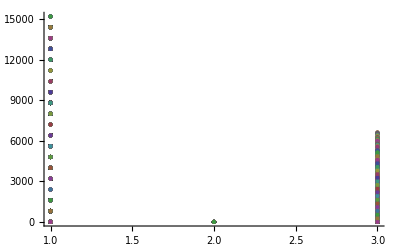

```mathematica
ListPlot[all]
```

```mathematica
g=Sort[Map[#[[1]][[2]]&,Tally[all, #1[[2]]== #2[[2]]&]]]
```

{-0.130091,-0.128592,-0.127665,-0.126918,-0.125992,-0.125255,-0.124492,-0.123622,-0.123582,-0.122082,-0.121948,-0.121155,-0.120449,-0.119522,-0.118649,-0.117112,-0.116976,-0.115476,-0.115442,-0.11455,-0.114391,-0.11436,-0.112718,-0.112611,-0.11214,-0.111549,-0.111218,-0.110659,-0.110506,-0.110291,-0.109799,-0.109643,-0.108718,-0.107894,-0.107881,-0.107847,-0.107008,-0.106813,-0.106766,-0.106248,-0.105942,-0.105335,-0.105016,-0.10486,-0.104001,-0.103842,-0.103836,-0.103111,-0.102909,-0.102093,-0.102049,-0.101276,-0.101011,-0.100499,-0.100299,-0.10014,-0.0992181,-0.0990592,-0.0988741,-0.0988657,-0.0981997,-0.0973097,-0.0971245,-0.0962943,-0.0962477,-0.0960432,-0.0951725,-0.0944981,-0.0943422,-0.0940912,-0.0938932,-0.0936347,-0.0934168,-0.0932317,-0.0925927,-0.0923417,-0.0915114,-0.0913262,-0.0912796,-0.0902613,-0.0902608,-0.0896349,-0.0895301,-0.0893742,-0.0889633,-0.0886998,-0.0885118,-0.0884488,-0.0879743,-0.0876246,-0.0874305,-0.0868638,-0.0866768,-0.0865597,-0.0865434,-0.085525,-0.0854785,-0.0846189,-0.0845773,-0.0845214,-0.0837318,-0.0837289,-0.0835729,-0.0833029,-0.0827135,-0.0826669,-0.0822348,-0.0818234,-0.0812034,-0.0810128,-0.0809173,-0.0807614,-0.0807421,-0.0799059,-0.0798361,-0.0797153,-0.0790119,-0.078861,-0.0779306,-0.0779306,-0.0776158,-0.0775634,-0.0769123,-0.0763414,-0.0760251,-0.075464,-0.0752734,-0.075119,-0.0750512,-0.0749602,-0.0742419,-0.0740549,-0.0737536,-0.0732107,-0.0729444,-0.0721294,-0.0719554,-0.0719442,-0.0718995,-0.0716542,-0.0706579,-0.070602,-0.0703798,-0.0699922,-0.0696129,-0.0693178,-0.0693117,-0.0685025,-0.0683154,-0.0682803,-0.0682426,-0.0680932,-0.0674124,-0.067284,-0.0671614,-0.0669828,-0.066216,-0.0659938,-0.0659378,-0.0649415,-0.0647159,-0.0646962,-0.0646403,-0.0643498,-0.0636513,-0.0634184,-0.0628421,-0.0625409,-0.0624443,-0.0623538,-0.0615445,-0.0613224,-0.0613189,-0.0611317,-0.0602543,-0.0600445,-0.0590323,-0.0589799,-0.0589764,-0.057945,-0.0577579,-0.0577348,-0.0568804,-0.056707,-0.0566898,-0.0566475,-0.0566431,-0.0556585,-0.0556026,-0.0555829,-0.0553923,-0.054361,-0.0543609,-0.054305,-0.0538488,-0.053316,-0.0532929,-0.0522056,-0.0520743,-0.0520185,-0.0520184,-0.0509871,-0.0507965,-0.049919,-0.049919,-0.0497319,-0.0496315,-0.048697,-0.0486446,-0.0486214,-0.0480095,-0.0476324,-0.0473995,-0.0465451,-0.0463545,-0.0463349,-0.0453852,-0.0452476,-0.045147,-0.045057,-0.0448348,-0.0440256,-0.042961,-0.0429576,-0.0427354,-0.0424572,-0.0417391,-0.0416831,-0.0414378,-0.0409296,-0.0403929,-0.0395837,-0.0393966,-0.0393077,-0.0390954,-0.0382862,-0.0380714,-0.038064,-0.0376949,-0.0372971,-0.0369959,-0.0366834,-0.0364495,-0.0359996,-0.0357774,-0.0357215,-0.0338252,-0.0337553,-0.033622,-0.0334776,-0.033435,-0.0326257,-0.0323245,-0.0322322,-0.0318557,-0.0313355,-0.0308971,-0.0306194,-0.030038,-0.0296079,-0.0292313,-0.0289975,-0.0288159,-0.027986,-0.0266798,-0.0266641,-0.0264735,-0.0263732,-0.0263033,-0.0250579,-0.0247801,-0.0247758,-0.024374,-0.0234451,-0.0230765,-0.0224336,-0.0221558,-0.0219176,-0.0205585,-0.0205339,-0.0202957,-0.0197026,-0.0192277,-0.0189366,-0.0177003,-0.0176713,-0.0176058,-0.0174161,-0.0163122,-0.0160784,-0.0160783,-0.0149815,-0.0147433,-0.0134541,-0.013454,-0.0133842,-0.0132201,-0.011861,-0.0118321,-0.0105958,-0.010526,-0.0105259,-0.0092367,-0.00899845,-0.0089739,-0.00890399,-0.00766773,-0.0076148,-0.00737654,-0.00630863,-0.00627967,-0.00604582,-0.00475653,-0.00475222,-0.00468672,-0.0034215,-0.00315918,-0.0020624,-0.00182846,-0.00182415,-0.0015464,-0.000534858,-0.00030101,0.0000755016,0.000795861,0.00108704,0.00232331,0.00239321,0.00241776,0.00269982,0.00394521,0.00401512,0.00429287,0.00525138,0.00562789,0.00663944,0.00687329,0.00691719,0.00715104,0.00816258,0.00853909,0.00865011,0.00949761,0.00977536,0.00984526,0.0110907,0.0113973,0.0114672,0.0127034,0.013715,0.0140915,0.0143253,0.0153369,0.0156146,0.0158529,0.0169497,0.0184772,0.0185427,0.0200991,0.0202526,0.021167,0.0214053,0.0227889,0.0230272,0.0240635,0.0243165,0.0256515,0.0271746,0.0272445,0.0296866,0.0298689,0.0301027,0.0301886,0.0314908,0.0318491,0.032727,0.0339995,0.0343489,0.0353482,0.0385663,0.0392523,0.0396227,0.0417852,0.0452843,0.045602,0.0474141,0.0491884,0.051225,0.0512251,0.0533877,0.055036,0.0568481,0.0568868,0.0571985,0.0590107,0.0606976,0.0607908,0.0625098,0.0628217,0.0628274,0.0646017,0.0663208,0.0664139,0.0684506,0.0684833,0.0702249,0.0706131,0.0722615,0.0723874,0.0727635,0.0741122,0.074424,0.0758865,0.0779231,0.0780163,0.0783867,0.0800472,0.0805492,0.0818272,0.0821976,0.0835463,0.0840483,0.0843601,0.0857088,0.0874504,0.0878592,0.0879524,0.0896129,0.0899832,0.0917633,0.093112,0.0934823,0.0938,0.0956449,0.0959625,0.0973864,0.0994616,0.099549,0.101586,0.103048,0.103366,0.105085,0.105397,0.107247,0.108896,0.108989,0.111058,0.111151,0.1128,0.114651,0.114962,0.116681,0.118461,0.120585,0.124085,0.126247,0.156768,0.171672,0.189076,0.194792,0.19751,0.203227,0.206471,0.211719,0.214914,0.217575,0.22063,0.229065,0.229818,0.232309,0.235534,0.237557,0.243414,0.243969,0.247213,0.252462,0.252938,0.258318,0.261373,0.264617,0.267089,0.269865,0.270333,0.275582,0.275721,0.278768,0.281438,0.284016,0.28726,0.289872,0.293116,0.298365}

```mathematica
g=Sort[{0.3135359480574428,0.3433441277875019,0.37815148988067165,0.38958416653075645,0.4064536236484377,0.41294123667099825,0.423438518908676,0.43515080744693124,0.3950205687020296,0.4298279307951994,0.44126060744528417,0.4581300645629654,0.46461767758552597,0.47511495982320373,0.48682724836145896,0.4596361105252585,0.4710687871753433,0.4879382442930245,0.4944258573155851,0.5049231395532628,0.5166354280915181,0.5058761492685131,0.5227456063861944,0.5292332194087549,0.5397305016464327,0.5514427901846879,0.5341782830362791,0.5406658960588396,0.5511631782965174,0.5628754668347726,0.5575353531765209,0.5680326354141987,0.5797449239524539,0.5745202484367592,0.5862325369750144,0.5967298192126922,0.025950322273487147,0.06075768436665685,0.0721903610167417,0.08905981813442287,0.0955474311569835,0.10604471339466126,0.1177570019329165,0.09056586409671596,0.10199854074680081,0.11886799786448199,0.1253556108870426,0.13585289312472038,0.1475651816629756,0.13680590283997063,0.1536753599576518,0.16016297298021237,0.17066025521789008,0.18237254375614537,0.16510803660773665,0.17159564963029716,0.18209293186797493,0.19380522040623016,0.1884651067479784,0.1989623889856561,0.2106746775239114,0.20545000200821673,0.21716229054647196,0.22765957278414972,0.14224230501124369,0.15367498166132854,0.1705444387790097,0.17703205180157033,0.1875293340392481,0.19924162257750333,0.18848234375449835,0.20535180087217952,0.2118394138947401,0.2223366961324178,0.2340489846706731,0.21678447752226437,0.22327209054482489,0.23376937278250265,0.24548166132075788,0.24014154766250612,0.2506388299001838,0.2623511184384391,0.25712644292274445,0.2688387314609997,0.27933601369867744,0.21829052348455746,0.23515998060223864,0.2416475936247992,0.2521448758624769,0.2638571644007322,0.2465926572523235,0.253080270274884,0.26357755251256176,0.275289841050817,0.26994972739256523,0.28044700963024294,0.2921592981684982,0.28693462265280356,0.2986469111910588,0.30914419342873656,0.2814000193454933,0.2878876323680538,0.2983849146057316,0.3100972031439868,0.30475708948573504,0.31525437172341275,0.32696666026166804,0.3217419847459734,0.3334542732842286,0.34395155552190637,0.3161897661358198,0.3266870483734975,0.3383993369117528,0.3331746613960581,0.34488694993431335,0.3553842321719911,0.3500441185137394,0.36175640705199463,0.3722536892896724,0.3787413023122329,-0.22682794141729878,-0.21539526476721393,-0.19852580764953276,-0.19203819462697214,-0.18154091238929437,-0.16982862385103914,-0.18058790267404412,-0.16371844555636295,-0.15723083253380238,-0.14673355029612467,-0.13502126175786938,-0.1522857689062781,-0.14579815588371758,-0.13530087364603982,-0.12358858510778459,-0.12892869876603635,-0.11843141652835865,-0.10671912799010336,-0.11194380350579802,-0.10023151496754279,-0.08973423272986503,-0.150779722943985,-0.13391026582630383,-0.12742265280374326,-0.11692537056606556,-0.10521308202781027,-0.12247758917621898,-0.11598997615365847,-0.1054926939159807,-0.09378040537772547,-0.09912051903597724,-0.08862323679829953,-0.07691094826004424,-0.08213562377573891,-0.07042333523748368,-0.05992605299980591,-0.08767022708304922,-0.08118261406048871,-0.07068533182281095,-0.058973043284555715,-0.06431315694280748,-0.053815874705129774,-0.042103586166874485,-0.04732826168256915,-0.03561597314431392,-0.025118690906636154,-0.05288048029272269,-0.04238319805504498,-0.03067090951678969,-0.035895585032484356,-0.024183296494229123,-0.01368601425655136,-0.019026127914803126,-0.007313839376547893,0.0031834428611298704,0.009671055883690438,-0.09910328202945728,-0.08223382491177611,-0.07574621188921554,-0.06524892965153783,-0.053536641113282546,-0.07080114826169126,-0.06431353523913075,-0.053816253001452985,-0.04210396446319775,-0.04744407812144952,-0.03694679588377181,-0.02523450734551652,-0.030459182861211187,-0.018746894322955954,-0.00824961208527819,-0.0359937861685215,-0.02950617314596099,-0.019008890908283227,-0.007296602370027994,-0.01263671602827976,-0.002139433790602052,0.009572854747653237,0.004348179231958571,0.016060467770213804,0.026557750007891567,-0.0012040393781949654,0.009293242859482742,0.02100553139773803,0.015780855882043365,0.0274931444202986,0.03799042665797636,0.032650312999724596,0.04436260153797983,0.05485988377565759,0.06134749679821816,-0.006185606438462388,0.00030200658409812453,0.010799288821775888,0.02251157736003112,0.017171463701779355,0.027668745939457062,0.03938103447771235,0.034156358962017686,0.04586864750027292,0.05636592973795068,0.02860414035186415,0.03910142258954186,0.050813711127797145,0.04558903561210248,0.05730132415035771,0.06779860638803548,0.06245849272978371,0.07417078126803894,0.0846680635057167,0.09115567652827727,0.06341150244503396,0.07390878468271167,0.08562107322096696,0.0803963977052723,0.09210868624352753,0.10260596848120529,0.09726585482295358,0.10897814336120881,0.11947542559888658,0.1259630386214471,0.10869853147303832,0.12041082001129355,0.13090810224897131,0.13739571527153183,0.1542651723892131,-0.46817352845799987,-0.4513040713403186,-0.44481645831775807,-0.4343191760800803,-0.42260688754182507,-0.43987139469023384,-0.4333837816676732,-0.42288649942999545,-0.4111742108917402,-0.41651432454999204,-0.4060170423123143,-0.39430475377405905,-0.39952942928975366,-0.3878171407514984,-0.37731985851382066,-0.4050640325970639,-0.3985764195745034,-0.38807913733682564,-0.3763668487985704,-0.38170696245682223,-0.37120968021914447,-0.35949739168088923,-0.36472206719658395,-0.3530097786583287,-0.34251249642065096,-0.3702742858067374,-0.3597770035690596,-0.3480647150308044,-0.3532893905464991,-0.34157710200824387,-0.3310798197705661,-0.33641993342881793,-0.3247076448905627,-0.31421036265288493,-0.3077227496303243,-0.3752558528670048,-0.3687682398444443,-0.3582709576067665,-0.3465586690685113,-0.3518987827267631,-0.34140150048908535,-0.3296892119508301,-0.33491388746652484,-0.3232015989282696,-0.31270431669059184,-0.34046610607667827,-0.3299688238390005,-0.31825653530074527,-0.32348121081644,-0.31176892227818476,-0.301271640040507,-0.3066117536987588,-0.2948994651605036,-0.2844021829228258,-0.2779145699002652,-0.3056587439835085,-0.29516146174583074,-0.2834491732075755,-0.28867384872327023,-0.276961560185015,-0.26646427794733724,-0.27180439160558906,-0.2600921030673338,-0.24959482082965606,-0.24310720780709544,-0.26037171495550426,-0.24865942641724903,-0.23816214417957127,-0.23167453115701064,-0.2148050740393294,-0.3235794119524771,-0.31709179892991657,-0.3065945166922388,-0.29488222815398357,-0.3002223418122354,-0.28972505957455763,-0.2780127710363024,-0.2832374465519971,-0.2715251580137419,-0.2610278757760641,-0.28878966516215054,-0.2782923829244728,-0.26658009438621755,-0.27180476990191227,-0.26009248136365704,-0.24959519912597927,-0.2549353127842311,-0.24322302424597586,-0.2327257420082981,-0.22623812898573747,-0.2539823030689808,-0.24348502083130302,-0.2317727322930478,-0.2369974078087425,-0.22528511927048728,-0.21478783703280951,-0.22012795069106134,-0.2084156621528061,-0.19791837991512834,-0.19143076689256772,-0.20869527404097654,-0.1969829855027213,-0.18648570326504355,-0.17999809024248292,-0.1631286331248017,-0.22417412333892167,-0.2136768411012439,-0.20196455256298868,-0.2071892280786834,-0.19547693954042816,-0.1849796573027504,-0.19031977096100222,-0.178607482422747,-0.16811020018506923,-0.1616225871625086,-0.17888709431091743,-0.1671748057726622,-0.15667752353498443,-0.1501899105124238,-0.13332045339474258,-0.1440797322177476,-0.13236744367949238,-0.12187016144181462,-0.115382548419254,-0.09851309130157271,-0.08708041465148797,-0.6926496583810196,-0.686162045358459,-0.6756647631207813,-0.663952474582526,-0.6692925882407779,-0.6587953060031001,-0.6470830174648449,-0.6523076929805396,-0.6405954044422844,-0.6300981222046066,-0.657859911590693,-0.6473626293530153,-0.63565034081476,-0.6408750163304547,-0.6291627277921995,-0.6186654455545217,-0.6240055592127736,-0.6122932706745183,-0.6017959884368406,-0.5953083754142799,-0.6230525494975233,-0.6125552672598455,-0.6008429787215903,-0.606067654237285,-0.5943553656990298,-0.583858083461352,-0.5891981971196039,-0.5774859085813486,-0.5669886263436709,-0.5605010133211102,-0.577765520469519,-0.5660532319312638,-0.555555949693586,-0.5490683366710254,-0.5321988795533442,-0.5932443697674642,-0.5827470875297864,-0.5710347989915312,-0.5762594745072259,-0.5645471859689707,-0.5540499037312929,-0.5593900173895447,-0.5476777288512895,-0.5371804466136118,-0.5306928335910511,-0.5479573407394599,-0.5362450522012047,-0.5257477699635269,-0.5192601569409663,-0.5023906998232851,-0.5131499786462901,-0.5014376901080349,-0.4909404078703571,-0.48445279484779646,-0.4675833377301153,-0.45615066108003044,-0.5415679288529365,-0.5310706466152587,-0.5193583580770035,-0.5245830335926982,-0.512870745054443,-0.5023734628167652,-0.507713576475017,-0.4960012879367618,-0.48550400569908403,-0.4790163926765234,-0.4962808998249322,-0.48456861128667694,-0.4740713290489992,-0.46758371602643856,-0.4507142589087574,-0.46147353773176236,-0.44976124919350713,-0.43926396695582937,-0.43277635393326874,-0.41590689681558757,-0.4044742201655027,-0.43166535800170325,-0.419953069463448,-0.40945578722577025,-0.40296817420320963,-0.38609871708552845,-0.3746660404354436,-0.3398586783422738,-0.910638175281479,-0.9001408930438012,-0.8884286045055458,-0.8936532800212406,-0.8819409914829853,-0.8714437092453076,-0.8767838229035594,-0.8650715343653042,-0.8545742521276264,-0.8480866391050659,-0.8653511462534745,-0.8536388577152193,-0.8431415754775415,-0.836653962454981,-0.8197845053372999,-0.8305437841603048,-0.8188314956220496,-0.8083342133843718,-0.8018466003618113,-0.7849771432441301,-0.7735444665940453,-0.8007356044302457,-0.7890233158919905,-0.7785260336543127,-0.7720384206317522,-0.755168963514071,-0.7437362868639862,-0.7089289247708164,-0.749059163515718,-0.7373468749774628,-0.726849592739785,-0.7203619797172245,-0.7034925225995433,-0.6920598459494585,-0.6572524838562886,-0.6274443041262295}]
```

{-0.910638,-0.900141,-0.893653,-0.888429,-0.881941,-0.876784,-0.871444,-0.865351,-0.865072,-0.854574,-0.853639,-0.848087,-0.843142,-0.836654,-0.830544,-0.819785,-0.818831,-0.808334,-0.801847,-0.800736,-0.789023,-0.784977,-0.778526,-0.773544,-0.772038,-0.755169,-0.749059,-0.743736,-0.737347,-0.72685,-0.720362,-0.708929,-0.703493,-0.69265,-0.69206,-0.686162,-0.675665,-0.669293,-0.663952,-0.658795,-0.65786,-0.657252,-0.652308,-0.647363,-0.647083,-0.640875,-0.640595,-0.63565,-0.630098,-0.629163,-0.627444,-0.624006,-0.623053,-0.618665,-0.612555,-0.612293,-0.606068,-0.601796,-0.600843,-0.595308,-0.594355,-0.593244,-0.589198,-0.583858,-0.582747,-0.577766,-0.577486,-0.576259,-0.571035,-0.566989,-0.566053,-0.564547,-0.560501,-0.55939,-0.555556,-0.55405,-0.549068,-0.547957,-0.547678,-0.541568,-0.53718,-0.536245,-0.532199,-0.531071,-0.530693,-0.525748,-0.524583,-0.519358,-0.51926,-0.51315,-0.512871,-0.507714,-0.502391,-0.502373,-0.501438,-0.496281,-0.496001,-0.49094,-0.485504,-0.484569,-0.484453,-0.479016,-0.474071,-0.468174,-0.467584,-0.467583,-0.461474,-0.456151,-0.451304,-0.450714,-0.449761,-0.444816,-0.439871,-0.439264,-0.434319,-0.433384,-0.432776,-0.431665,-0.422886,-0.422607,-0.419953,-0.416514,-0.415907,-0.411174,-0.409456,-0.406017,-0.405064,-0.404474,-0.402968,-0.399529,-0.398576,-0.394305,-0.388079,-0.387817,-0.386099,-0.381707,-0.37732,-0.376367,-0.375256,-0.374666,-0.37121,-0.370274,-0.368768,-0.364722,-0.359777,-0.359497,-0.358271,-0.353289,-0.35301,-0.351899,-0.348065,-0.346559,-0.342512,-0.341577,-0.341402,-0.340466,-0.339859,-0.33642,-0.334914,-0.33108,-0.329969,-0.329689,-0.324708,-0.323579,-0.323481,-0.323202,-0.318257,-0.317092,-0.31421,-0.312704,-0.311769,-0.307723,-0.306612,-0.306595,-0.305659,-0.301272,-0.300222,-0.295161,-0.294899,-0.294882,-0.289725,-0.28879,-0.288674,-0.284402,-0.283449,-0.283237,-0.278292,-0.278013,-0.277915,-0.276962,-0.271805,-0.271804,-0.271525,-0.26658,-0.266464,-0.261028,-0.260372,-0.260092,-0.260092,-0.254935,-0.253982,-0.249595,-0.249595,-0.248659,-0.243485,-0.243223,-0.243107,-0.238162,-0.236997,-0.232726,-0.231773,-0.231675,-0.226828,-0.226238,-0.225285,-0.224174,-0.220128,-0.215395,-0.214805,-0.214788,-0.213677,-0.208695,-0.208416,-0.207189,-0.201965,-0.198526,-0.197918,-0.196983,-0.195477,-0.192038,-0.191431,-0.19032,-0.186486,-0.18498,-0.181541,-0.180588,-0.179998,-0.178887,-0.178607,-0.169829,-0.16811,-0.167175,-0.163718,-0.163129,-0.161623,-0.157231,-0.156678,-0.152286,-0.15078,-0.15019,-0.146734,-0.145798,-0.14408,-0.135301,-0.135021,-0.13391,-0.13332,-0.132367,-0.128929,-0.127423,-0.123589,-0.122478,-0.12187,-0.118431,-0.116925,-0.11599,-0.115383,-0.111944,-0.106719,-0.105493,-0.105213,-0.100232,-0.0991205,-0.0991033,-0.0985131,-0.0937804,-0.0897342,-0.0886232,-0.0876702,-0.0870804,-0.0822338,-0.0821356,-0.0811826,-0.0769109,-0.0757462,-0.0708011,-0.0706853,-0.0704233,-0.0652489,-0.0643135,-0.0643132,-0.0599261,-0.058973,-0.0538163,-0.0538159,-0.0535366,-0.0528805,-0.0474441,-0.0473283,-0.0423832,-0.042104,-0.0421036,-0.0369468,-0.0359938,-0.0358956,-0.035616,-0.0306709,-0.0304592,-0.0295062,-0.0252345,-0.0251187,-0.0241833,-0.0190261,-0.0190089,-0.0187469,-0.013686,-0.0126367,-0.00824961,-0.00731384,-0.0072966,-0.00618561,-0.00213943,-0.00120404,0.000302007,0.00318344,0.00434818,0.00929324,0.00957285,0.00967106,0.0107993,0.0157809,0.0160605,0.0171715,0.0210055,0.0225116,0.0259503,0.0265578,0.0274931,0.0276687,0.0286041,0.0326503,0.0341564,0.0379904,0.0391014,0.039381,0.0443626,0.045589,0.0458686,0.0508137,0.0548599,0.0563659,0.0573013,0.0607577,0.0613475,0.0624585,0.0634115,0.0677986,0.0721904,0.0739088,0.0741708,0.0803964,0.0846681,0.0856211,0.0890598,0.0905659,0.0911557,0.0921087,0.0955474,0.0972659,0.101999,0.102606,0.106045,0.108699,0.108978,0.117757,0.118868,0.119475,0.120411,0.125356,0.125963,0.130908,0.135853,0.136806,0.137396,0.142242,0.147565,0.153675,0.153675,0.154265,0.160163,0.165108,0.170544,0.17066,0.171596,0.177032,0.182093,0.182373,0.187529,0.188465,0.188482,0.193805,0.198962,0.199242,0.205352,0.20545,0.210675,0.211839,0.216784,0.217162,0.218291,0.222337,0.223272,0.22766,0.233769,0.234049,0.23516,0.240142,0.241648,0.245482,0.246593,0.250639,0.252145,0.25308,0.257126,0.262351,0.263578,0.263857,0.268839,0.26995,0.27529,0.279336,0.280447,0.2814,0.286935,0.287888,0.292159,0.298385,0.298647,0.304757,0.309144,0.310097,0.313536,0.315254,0.31619,0.321742,0.326687,0.326967,0.333175,0.333454,0.338399,0.343344,0.343952,0.344887,0.350044,0.355384,0.361756,0.372254,0.378151,0.378741,0.389584,0.395021,0.406454,0.412941,0.423439,0.429828,0.435151,0.441261,0.45813,0.459636,0.464618,0.471069,0.475115,0.486827,0.487938,0.494426,0.504923,0.505876,0.516635,0.522746,0.529233,0.534178,0.539731,0.540666,0.551163,0.551443,0.557535,0.562875,0.568033,0.57452,0.579745,0.586233,0.59673}

```mathematica
Length[g]
```

492

```mathematica
Animate[
ListPlot[
Map[{#[[1]], #[[3]]}&, Select[all, #[[2]]==gg&]],
PlotStyle->Directive[Opacity[1], ColorData["DarkRainbow"][gg]],
PlotLabel->"Ln Voted values for magic value " <> ToString[gg],
PlotRange->{All,{0,10000}},
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
AxesStyle->{FontFamily->"Calibri", FontSize->Smaller},
PlotRangePadding->None
],
{gg, Sort[g,Greater]},
AnimationRate->5
]
```

```mathematica
Export["c:\\Users\\Willy\\Documents\\VotedValues-1000-calibrated.avi", Table[
ListLinePlot[
Map[{#[[1]], #[[3]]}&, Select[all, #[[2]]==gg&]],
PlotStyle->Directive[Opacity[1], ColorData["DarkRainbow"][gg]],
PlotLabel->"Ln Voted values for calibrated magic value " <> ToString[gg],
PlotRange->{{0,16000},{0,1000}},
GridLines->None,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
AxesStyle->{FontFamily->"Calibri", FontSize->Smaller},
ImageSize->800,
PlotMarkers->Automatic
],
{gg, Sort[g,Greater]}
], "AVI"]
```

c:\Users\Willy\Documents\VotedValues-1000-calibrated.avi

```mathematica
Flatten[
Table[
Map[{#[[1]], #[[2]]}&, Select[all, #[[2]]==gg&]],
{gg, g}
], 1]
```

{{1.,0.313536},{801.,0.313536},{1601.,0.313536},{2401.,0.313536},{3201.,0.313536},{4001.,0.313536},{4801.,0.313536},{5601.,0.313536},{6401.,0.313536},{7201.,0.313536},{8001.,0.313536},{8801.,0.313536},{9601.,0.313536},{10401.,0.313536},{11201.,0.313536},{12001.,0.313536},«9809»,{4001.,-0.627444},{4801.,-0.627444},{5601.,-0.627444},{6401.,-0.627444},{7201.,-0.627444},{8001.,-0.627444},{8801.,-0.627444},{9601.,-0.627444},{10401.,-0.627444},{11201.,-0.627444},{12001.,-0.627444},{12801.,-0.627444},{13601.,-0.627444},{14401.,-0.627444},{15201.,-0.627444}}

```mathematica
Table[
ListLinePlot[
Map[{#[[1]], #[[3]]}&, Select[all, #[[2]]==gg&]],
PlotStyle->Directive[Opacity[1], ColorData["DarkRainbow"][gg]],
PlotLabel->"Ln Voted values for magic value " <> ToString[gg],
PlotRange->{{0,16000},{0,10000}},
PlotRangeClipping->False,
DataRange->{All,{0,10000}},
GridLines->None,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
AxesStyle->{FontFamily->"Calibri", FontSize->Smaller},
PlotRangePadding->None,
ImageSize->800,
PlotMarkers->Automatic
],
{gg, Take[Sort[g,Greater],3]}
]
```

```mathematica
Export["c:\\Users\\Willy\\Documents\\VotedValues-calibrated.avi", Table[
ListLinePlot[
Map[{#[[1]], #[[3]]}&, Select[all, #[[2]]==gg&]],
PlotStyle->Directive[Opacity[1], ColorData["DarkRainbow"][gg]],
PlotLabel->"Ln Voted values for calibrated magic value " <> ToString[gg],
PlotRange->{{0,16000},{0,10000}},
GridLines->None,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
AxesStyle->{FontFamily->"Calibri", FontSize->Smaller},
ImageSize->800,
PlotMarkers->Automatic
],
{gg, Sort[g,Greater]}
], "AVI"]
```

c:\Users\Willy\Documents\VotedValues-calibrated.avi